# Temporal Evolution of Sound

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
```

## Boxes

```mathematica
MakeBoxes[sStar,StandardForm]:=SubscriptBox["s","*"];
MakeExpression[SubscriptBox["s","*"],StandardForm]:=MakeExpression["sStar",StandardForm];
MakeBoxes[tStar,StandardForm]:=SubscriptBox["t","*"];
MakeExpression[SubscriptBox["t","*"],StandardForm]:=MakeExpression["tStar",StandardForm];
MakeBoxes[t0,StandardForm]:=SubscriptBox["t","0"];
MakeExpression[SubscriptBox["t","0"],StandardForm]:=MakeExpression["t0",StandardForm];
MakeBoxes[etaStar,StandardForm]:=SubscriptBox["η","*"];
MakeExpression[SubscriptBox["η","*"],StandardForm]:=MakeExpression["etaStar",StandardForm];
MakeBoxes[eta0,StandardForm]:=SubscriptBox["η","0"];
MakeExpression[SubscriptBox["η","0"],StandardForm]:=MakeExpression["eta0",StandardForm];
MakeBoxes[zStar,StandardForm]:=SubscriptBox["z","*"];
MakeExpression[SubscriptBox["z","*"],StandardForm]:=MakeExpression["zStar",StandardForm];
MakeBoxes[rStar,StandardForm]:=SubscriptBox["r","*"];
MakeExpression[SubscriptBox["r","*"],StandardForm]:=MakeExpression["rStar",StandardForm];
MakeBoxes[kD,StandardForm]:=SubscriptBox["k","D"];
MakeExpression[SubscriptBox["k","D"],StandardForm]:=MakeExpression["kD",StandardForm];
MakeBoxes[Hp,StandardForm]:=SubscriptBox["H","p"];
MakeExpression[SubscriptBox["H","p"],StandardForm]:=MakeExpression["Hp",StandardForm];
MakeBoxes[zPrime,StandardForm]:=SuperscriptBox["z","'"];
MakeExpression[SuperscriptBox["z","'"],StandardForm]:=MakeExpression["zPrime",StandardForm];
MakeBoxes[tPrime,StandardForm]:=SuperscriptBox["t","'"];
MakeExpression[SuperscriptBox["t","'"],StandardForm]:=MakeExpression["tPrime",StandardForm];
MakeBoxes[etaPrime,StandardForm]:=SuperscriptBox["η","'"];
MakeExpression[SuperscriptBox["η","'"],StandardForm]:=MakeExpression["etaPrime",StandardForm];
MakeBoxes[aEta,StandardForm]:=SubscriptBox["a","η"];
MakeExpression[SubscriptBox["a","η"],StandardForm]:=MakeExpression["aEta",StandardForm];
MakeBoxes[etaT,StandardForm]:=SubscriptBox["η","t"];
MakeExpression[SubscriptBox["η","t"],StandardForm]:=MakeExpression["etaT",StandardForm];
MakeBoxes[etaZ,StandardForm]:=SubscriptBox["η","z"];
MakeExpression[SubscriptBox["η","z"],StandardForm]:=MakeExpression["etaZ",StandardForm];
MakeBoxes[tZ,StandardForm]:=SubscriptBox["t","z"];
MakeExpression[SubscriptBox["t","z"],StandardForm]:=MakeExpression["tZ",StandardForm];
MakeBoxes[tEta,StandardForm]:=SubscriptBox["t","η"];
MakeExpression[SubscriptBox["t","η"],StandardForm]:=MakeExpression["tEta",StandardForm];
MakeBoxes[zEta,StandardForm]:=SubscriptBox["z","η"];
MakeExpression[SubscriptBox["z","η"],StandardForm]:=MakeExpression["zEta",StandardForm];
MakeBoxes[freeElectronFraction,StandardForm]:=SubscriptBox["X","e"];
MakeExpression[SubscriptBox["X","e"],StandardForm]:=MakeExpression["freeElectronFraction",StandardForm];
MakeBoxes[scatterRate,StandardForm]:=OverscriptBox["τ", "."];
MakeExpression[OverscriptBox["τ", "."],StandardForm]:=MakeExpression["scatterRate",StandardForm];
MakeBoxes[electronDensity,StandardForm]:=SubscriptBox["n","e"];
MakeExpression[SubscriptBox["n","e"],StandardForm]:=MakeExpression["electronDensity",StandardForm];
MakeBoxes[interpolatedOpticalDepth,StandardForm]:=SubscriptBox["τ","i"];
MakeExpression[SubscriptBox["τ","i"],StandardForm]:=MakeExpression["interpolatedOpticalDepth",StandardForm];
MakeExpression[SubscriptBox["g","v"],StandardForm]:=MakeExpression["gv",StandardForm];
MakeBoxes[gv,StandardForm]:=SubscriptBox["g","v"];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01m ;
kg=1;
g=0.001kg;
J=1 kg m^2 s^-2;
K=1;
km=1000 m;
pc=3.08567758×10^13 km;
kpc=1000 pc;
Mpc = 1000000 pc;
```

## Clear Variables

```mathematica
ClearAll[z]; 
ClearAll[t];
ClearAll[η];
ClearAll[Subscript[t, η]];
ClearAll[Subscript[a, η]];
ClearAll[Subscript[t, z]];
ClearAll[SubStar[η]];
```

## Constants

```mathematica
c=2.99792458×10^5 km s^-1;
h=0.674;
Subscript[H, 0]=h 100 km s^-1 Mpc^-1;
G=6.67408×10^-11 m^3 kg^-1 s^-2;
ℏ=6.62607004×10^-34 J s;
Subscript[T, 0]=2.7255 K;
A=4.38693×10^-14 km s^-2;
Subscript[t, 0]=8.57697×10^17 s;
Subscript[k, B]=1.380649×10^-23 J K^-1;
Subscript[a, B]=(8 π^5 Subscript[k, B]^4)/(15 ℏ^3 c^3)J m^-3 K^-4;
Subscript[m, H]=1.6735575×10^-27 kg;
Subscript[m, HE]=6.6464764×10^-27 kg;
Subscript[Abundance, H]=0.75;
Subscript[Abundance, HE]=0.25;
Subscript[Ω, B]=0.0221 h^-2;
Subscript[ρ, C]=(3 Subscript[H, 0]^2)/(8π*G)kg m^-3;
Subscript[ρ, B]=Subscript[Ω, B] Subscript[ρ, C] kg m^-3;
Subscript[ρ, γ]=(Subscript[a, B] Subscript[T, 0]^4)/c^2 kg m^-3;
Subscript[σ, T]=6.6524×10^-29 m^2;
```

### Present Day Conformal Time

```mathematica
Subscript[η, 0]=Subscript[η, t][Subscript[t, 0]];
```

## Data

### Free Electron Fraction

```mathematica
FreeElectronFractionData={{3000,1.0829044},{2999.7,1.0828636},{2999.3999,1.0828634},{2999.0999,1.0828633},{2998.7999,1.0828632},{2998.4999,1.082863},{2998.1998,1.0828629},{2997.8998,1.0828627},{2997.5998,1.0828626},{2997.2997,1.0828625},{2996.9997,1.0828623},{2996.6997,1.0828622},{2996.3996,1.082862},{2996.0996,1.0828619},{2995.7996,1.0828618},{2995.4996,1.0828616},{2995.1995,1.0828615},{2994.8995,1.0828613},{2994.5995,1.0828612},{2994.2994,1.082861},{2993.9994,1.0828609},{2993.6994,1.0828607},{2993.3993,1.0828606},{2993.0993,1.0828604},{2992.7993,1.0828603},{2992.4993,1.0828602},{2992.1992,1.08286},{2991.8992,1.0828599},{2991.5992,1.0828597},{2991.2991,1.0828596},{2990.9991,1.0828594},{2990.6991,1.0828593},{2990.399,1.0828591},{2990.099,1.0828589},{2989.799,1.0828588},{2989.499,1.0828586},{2989.1989,1.0828585},{2988.8989,1.0828583},{2988.5989,1.0828582},{2988.2988,1.082858},{2987.9988,1.0828579},{2987.6988,1.0828577},{2987.3987,1.0828576},{2987.0987,1.0828574},{2986.7987,1.0828572},{2986.4987,1.0828571},{2986.1986,1.0828569},{2985.8986,1.0828568},{2985.5986,1.0828566},{2985.2985,1.0828564},{2984.9985,1.0828563},{2984.6985,1.0828561},{2984.3984,1.0828559},{2984.0984,1.0828558},{2983.7984,1.0828556},{2983.4984,1.0828555},{2983.1983,1.0828553},{2982.8983,1.0828551},{2982.5983,1.082855},{2982.2982,1.0828548},{2981.9982,1.0828546},{2981.6982,1.0828545},{2981.3981,1.0828543},{2981.0981,1.0828541},{2980.7981,1.0828539},{2980.4981,1.0828538},{2980.198,1.0828536},{2979.898,1.0828534},{2979.598,1.0828533},{2979.2979,1.0828531},{2978.9979,1.0828529},{2978.6979,1.0828527},{2978.3978,1.0828526},{2978.0978,1.0828524},{2977.7978,1.0828522},{2977.4978,1.082852},{2977.1977,1.0828519},{2976.8977,1.0828517},{2976.5977,1.0828515},{2976.2976,1.0828513},{2975.9976,1.0828511},{2975.6976,1.082851},{2975.3975,1.0828508},{2975.0975,1.0828506},{2974.7975,1.0828504},{2974.4975,1.0828502},{2974.1974,1.08285},{2973.8974,1.0828499},{2973.5974,1.0828497},{2973.2973,1.0828495},{2972.9973,1.0828493},{2972.6973,1.0828491},{2972.3972,1.0828489},{2972.0972,1.0828487},{2971.7972,1.0828485},{2971.4972,1.0828484},{2971.1971,1.0828482},{2970.8971,1.082848},{2970.5971,1.0828478},{2970.297,1.0828476},{2969.997,1.0828474},{2969.697,1.0828472},{2969.3969,1.082847},{2969.0969,1.0828468},{2968.7969,1.0828466},{2968.4969,1.0828464},{2968.1968,1.0828462},{2967.8968,1.082846},{2967.5968,1.0828458},{2967.2967,1.0828456},{2966.9967,1.0828454},{2966.6967,1.0828452},{2966.3967,1.082845},{2966.0966,1.0828448},{2965.7966,1.0828446},{2965.4966,1.0828444},{2965.1965,1.0828442},{2964.8965,1.082844},{2964.5965,1.0828438},{2964.2964,1.0828436},{2963.9964,1.0828434},{2963.6964,1.0828432},{2963.3964,1.082843},{2963.0963,1.0828427},{2962.7963,1.0828425},{2962.4963,1.0828423},{2962.1962,1.0828421},{2961.8962,1.0828419},{2961.5962,1.0828417},{2961.2961,1.0828415},{2960.9961,1.0828412},{2960.6961,1.082841},{2960.3961,1.0828408},{2960.096,1.0828406},{2959.796,1.0828404},{2959.496,1.0828402},{2959.1959,1.0828399},{2958.8959,1.0828397},{2958.5959,1.0828395},{2958.2958,1.0828393},{2957.9958,1.082839},{2957.6958,1.0828388},{2957.3958,1.0828386},{2957.0957,1.0828384},{2956.7957,1.0828381},{2956.4957,1.0828379},{2956.1956,1.0828377},{2955.8956,1.0828375},{2955.5956,1.0828372},{2955.2955,1.082837},{2954.9955,1.0828368},{2954.6955,1.0828365},{2954.3955,1.0828363},{2954.0954,1.0828361},{2953.7954,1.0828358},{2953.4954,1.0828356},{2953.1953,1.0828354},{2952.8953,1.0828351},{2952.5953,1.0828349},{2952.2952,1.0828346},{2951.9952,1.0828344},{2951.6952,1.0828342},{2951.3952,1.0828339},{2951.0951,1.0828337},{2950.7951,1.0828334},{2950.4951,1.0828332},{2950.195,1.0828329},{2949.895,1.0828327},{2949.595,1.0828324},{2949.2949,1.0828322},{2948.9949,1.0828319},{2948.6949,1.0828317},{2948.3949,1.0828314},{2948.0948,1.0828312},{2947.7948,1.0828309},{2947.4948,1.0828307},{2947.1947,1.0828304},{2946.8947,1.0828302},{2946.5947,1.0828299},{2946.2946,1.0828296},{2945.9946,1.0828294},{2945.6946,1.0828291},{2945.3946,1.0828289},{2945.0945,1.0828286},{2944.7945,1.0828283},{2944.4945,1.0828281},{2944.1944,1.0828278},{2943.8944,1.0828276},{2943.5944,1.0828273},{2943.2943,1.082827},{2942.9943,1.0828267},{2942.6943,1.0828265},{2942.3943,1.0828262},{2942.0942,1.0828259},{2941.7942,1.0828257},{2941.4942,1.0828254},{2941.1941,1.0828251},{2940.8941,1.0828248},{2940.5941,1.0828246},{2940.294,1.0828243},{2939.994,1.082824},{2939.694,1.0828237},{2939.394,1.0828234},{2939.0939,1.0828232},{2938.7939,1.0828229},{2938.4939,1.0828226},{2938.1938,1.0828223},{2937.8938,1.082822},{2937.5938,1.0828217},{2937.2938,1.0828215},{2936.9937,1.0828212},{2936.6937,1.0828209},{2936.3937,1.0828206},{2936.0936,1.0828203},{2935.7936,1.08282},{2935.4936,1.0828197},{2935.1935,1.0828194},{2934.8935,1.0828191},{2934.5935,1.0828188},{2934.2935,1.0828185},{2933.9934,1.0828182},{2933.6934,1.0828179},{2933.3934,1.0828176},{2933.0933,1.0828173},{2932.7933,1.082817},{2932.4933,1.0828167},{2932.1932,1.0828164},{2931.8932,1.0828161},{2931.5932,1.0828158},{2931.2932,1.0828155},{2930.9931,1.0828151},{2930.6931,1.0828148},{2930.3931,1.0828145},{2930.093,1.0828142},{2929.793,1.0828139},{2929.493,1.0828136},{2929.1929,1.0828133},{2928.8929,1.0828129},{2928.5929,1.0828126},{2928.2929,1.0828123},{2927.9928,1.082812},{2927.6928,1.0828116},{2927.3928,1.0828113},{2927.0927,1.082811},{2926.7927,1.0828107},{2926.4927,1.0828103},{2926.1926,1.08281},{2925.8926,1.0828097},{2925.5926,1.0828093},{2925.2926,1.082809},{2924.9925,1.0828087},{2924.6925,1.0828083},{2924.3925,1.082808},{2924.0924,1.0828077},{2923.7924,1.0828073},{2923.4924,1.082807},{2923.1923,1.0828066},{2922.8923,1.0828063},{2922.5923,1.0828059},{2922.2923,1.0828056},{2921.9922,1.0828053},{2921.6922,1.0828049},{2921.3922,1.0828046},{2921.0921,1.0828042},{2920.7921,1.0828038},{2920.4921,1.0828035},{2920.192,1.0828031},{2919.892,1.0828028},{2919.592,1.0828024},{2919.292,1.0828021},{2918.9919,1.0828017},{2918.6919,1.0828013},{2918.3919,1.082801},{2918.0918,1.0828006},{2917.7918,1.0828002},{2917.4918,1.0827999},{2917.1917,1.0827995},{2916.8917,1.0827991},{2916.5917,1.0827988},{2916.2917,1.0827984},{2915.9916,1.082798},{2915.6916,1.0827976},{2915.3916,1.0827973},{2915.0915,1.0827969},{2914.7915,1.0827965},{2914.4915,1.0827961},{2914.1914,1.0827957},{2913.8914,1.0827954},{2913.5914,1.082795},{2913.2914,1.0827946},{2912.9913,1.0827942},{2912.6913,1.0827938},{2912.3913,1.0827934},{2912.0912,1.082793},{2911.7912,1.0827926},{2911.4912,1.0827922},{2911.1911,1.0827918},{2910.8911,1.0827914},{2910.5911,1.082791},{2910.2911,1.0827906},{2909.991,1.0827902},{2909.691,1.0827898},{2909.391,1.0827894},{2909.0909,1.082789},{2908.7909,1.0827886},{2908.4909,1.0827882},{2908.1908,1.0827878},{2907.8908,1.0827873},{2907.5908,1.0827869},{2907.2908,1.0827865},{2906.9907,1.0827861},{2906.6907,1.0827857},{2906.3907,1.0827853},{2906.0906,1.0827848},{2905.7906,1.0827844},{2905.4906,1.082784},{2905.1906,1.0827835},{2904.8905,1.0827831},{2904.5905,1.0827827},{2904.2905,1.0827822},{2903.9904,1.0827818},{2903.6904,1.0827814},{2903.3904,1.0827809},{2903.0903,1.0827805},{2902.7903,1.0827801},{2902.4903,1.0827796},{2902.1903,1.0827792},{2901.8902,1.0827787},{2901.5902,1.0827783},{2901.2902,1.0827778},{2900.9901,1.0827774},{2900.6901,1.0827769},{2900.3901,1.0827765},{2900.09,1.082776},{2899.79,1.0827755},{2899.49,1.0827751},{2899.19,1.0827746},{2898.8899,1.0827742},{2898.5899,1.0827737},{2898.2899,1.0827732},{2897.9898,1.0827728},{2897.6898,1.0827723},{2897.3898,1.0827718},{2897.0897,1.0827713},{2896.7897,1.0827709},{2896.4897,1.0827704},{2896.1897,1.0827699},{2895.8896,1.0827694},{2895.5896,1.0827689},{2895.2896,1.0827684},{2894.9895,1.082768},{2894.6895,1.0827675},{2894.3895,1.082767},{2894.0894,1.0827665},{2893.7894,1.082766},{2893.4894,1.0827655},{2893.1894,1.082765},{2892.8893,1.0827645},{2892.5893,1.082764},{2892.2893,1.0827635},{2891.9892,1.082763},{2891.6892,1.0827625},{2891.3892,1.082762},{2891.0891,1.0827614},{2890.7891,1.0827609},{2890.4891,1.0827604},{2890.1891,1.0827599},{2889.889,1.0827594},{2889.589,1.0827589},{2889.289,1.0827583},{2888.9889,1.0827578},{2888.6889,1.0827573},{2888.3889,1.0827568},{2888.0888,1.0827562},{2887.7888,1.0827557},{2887.4888,1.0827551},{2887.1888,1.0827546},{2886.8887,1.0827541},{2886.5887,1.0827535},{2886.2887,1.082753},{2885.9886,1.0827524},{2885.6886,1.0827519},{2885.3886,1.0827513},{2885.0885,1.0827508},{2884.7885,1.0827502},{2884.4885,1.0827497},{2884.1885,1.0827491},{2883.8884,1.0827486},{2883.5884,1.082748},{2883.2884,1.0827474},{2882.9883,1.0827469},{2882.6883,1.0827463},{2882.3883,1.0827457},{2882.0882,1.0827451},{2881.7882,1.0827446},{2881.4882,1.082744},{2881.1882,1.0827434},{2880.8881,1.0827428},{2880.5881,1.0827422},{2880.2881,1.0827417},{2879.988,1.0827411},{2879.688,1.0827405},{2879.388,1.0827399},{2879.0879,1.0827393},{2878.7879,1.0827387},{2878.4879,1.0827381},{2878.1879,1.0827375},{2877.8878,1.0827369},{2877.5878,1.0827363},{2877.2878,1.0827357},{2876.9877,1.082735},{2876.6877,1.0827344},{2876.3877,1.0827338},{2876.0877,1.0827332},{2875.7876,1.0827326},{2875.4876,1.0827319},{2875.1876,1.0827313},{2874.8875,1.0827307},{2874.5875,1.0827301},{2874.2875,1.0827294},{2873.9874,1.0827288},{2873.6874,1.0827281},{2873.3874,1.0827275},{2873.0874,1.0827269},{2872.7873,1.0827262},{2872.4873,1.0827256},{2872.1873,1.0827249},{2871.8872,1.0827243},{2871.5872,1.0827236},{2871.2872,1.0827229},{2870.9871,1.0827223},{2870.6871,1.0827216},{2870.3871,1.082721},{2870.0871,1.0827203},{2869.787,1.0827196},{2869.487,1.0827189},{2869.187,1.0827183},{2868.8869,1.0827176},{2868.5869,1.0827169},{2868.2869,1.0827162},{2867.9868,1.0827155},{2867.6868,1.0827148},{2867.3868,1.0827141},{2867.0868,1.0827135},{2866.7867,1.0827128},{2866.4867,1.0827121},{2866.1867,1.0827114},{2865.8866,1.0827106},{2865.5866,1.0827099},{2865.2866,1.0827092},{2864.9865,1.0827085},{2864.6865,1.0827078},{2864.3865,1.0827071},{2864.0865,1.0827064},{2863.7864,1.0827056},{2863.4864,1.0827049},{2863.1864,1.0827042},{2862.8863,1.0827034},{2862.5863,1.0827027},{2862.2863,1.082702},{2861.9862,1.0827012},{2861.6862,1.0827005},{2861.3862,1.0826997},{2861.0862,1.082699},{2860.7861,1.0826982},{2860.4861,1.0826975},{2860.1861,1.0826967},{2859.886,1.0826959},{2859.586,1.0826952},{2859.286,1.0826944},{2858.9859,1.0826936},{2858.6859,1.0826929},{2858.3859,1.0826921},{2858.0859,1.0826913},{2857.7858,1.0826905},{2857.4858,1.0826897},{2857.1858,1.0826889},{2856.8857,1.0826881},{2856.5857,1.0826874},{2856.2857,1.0826866},{2855.9856,1.0826858},{2855.6856,1.0826849},{2855.3856,1.0826841},{2855.0856,1.0826833},{2854.7855,1.0826825},{2854.4855,1.0826817},{2854.1855,1.0826809},{2853.8854,1.08268},{2853.5854,1.0826792},{2853.2854,1.0826784},{2852.9853,1.0826776},{2852.6853,1.0826767},{2852.3853,1.0826759},{2852.0853,1.082675},{2851.7852,1.0826742},{2851.4852,1.0826733},{2851.1852,1.0826725},{2850.8851,1.0826716},{2850.5851,1.0826708},{2850.2851,1.0826699},{2849.985,1.082669},{2849.685,1.0826682},{2849.385,1.0826673},{2849.085,1.0826664},{2848.7849,1.0826655},{2848.4849,1.0826647},{2848.1849,1.0826638},{2847.8848,1.0826629},{2847.5848,1.082662},{2847.2848,1.0826611},{2846.9847,1.0826602},{2846.6847,1.0826593},{2846.3847,1.0826584},{2846.0847,1.0826575},{2845.7846,1.0826565},{2845.4846,1.0826556},{2845.1846,1.0826547},{2844.8845,1.0826538},{2844.5845,1.0826529},{2844.2845,1.0826519},{2843.9845,1.082651},{2843.6844,1.08265},{2843.3844,1.0826491},{2843.0844,1.0826481},{2842.7843,1.0826472},{2842.4843,1.0826462},{2842.1843,1.0826453},{2841.8842,1.0826443},{2841.5842,1.0826434},{2841.2842,1.0826424},{2840.9842,1.0826414},{2840.6841,1.0826404},{2840.3841,1.0826395},{2840.0841,1.0826385},{2839.784,1.0826375},{2839.484,1.0826365},{2839.184,1.0826355},{2838.8839,1.0826345},{2838.5839,1.0826335},{2838.2839,1.0826325},{2837.9839,1.0826315},{2837.6838,1.0826304},{2837.3838,1.0826294},{2837.0838,1.0826284},{2836.7837,1.0826274},{2836.4837,1.0826263},{2836.1837,1.0826253},{2835.8836,1.0826243},{2835.5836,1.0826232},{2835.2836,1.0826222},{2834.9836,1.0826211},{2834.6835,1.08262},{2834.3835,1.082619},{2834.0835,1.0826179},{2833.7834,1.0826169},{2833.4834,1.0826158},{2833.1834,1.0826147},{2832.8833,1.0826136},{2832.5833,1.0826125},{2832.2833,1.0826114},{2831.9833,1.0826103},{2831.6832,1.0826092},{2831.3832,1.0826081},{2831.0832,1.082607},{2830.7831,1.0826059},{2830.4831,1.0826048},{2830.1831,1.0826037},{2829.883,1.0826026},{2829.583,1.0826014},{2829.283,1.0826003},{2828.983,1.0825991},{2828.6829,1.082598},{2828.3829,1.0825969},{2828.0829,1.0825957},{2827.7828,1.0825945},{2827.4828,1.0825934},{2827.1828,1.0825922},{2826.8827,1.082591},{2826.5827,1.0825899},{2826.2827,1.0825887},{2825.9827,1.0825875},{2825.6826,1.0825863},{2825.3826,1.0825851},{2825.0826,1.0825839},{2824.7825,1.0825827},{2824.4825,1.0825815},{2824.1825,1.0825803},{2823.8824,1.0825791},{2823.5824,1.0825778},{2823.2824,1.0825766},{2822.9824,1.0825754},{2822.6823,1.0825741},{2822.3823,1.0825729},{2822.0823,1.0825717},{2821.7822,1.0825704},{2821.4822,1.0825691},{2821.1822,1.0825679},{2820.8821,1.0825666},{2820.5821,1.0825653},{2820.2821,1.0825641},{2819.9821,1.0825628},{2819.682,1.0825615},{2819.382,1.0825602},{2819.082,1.0825589},{2818.7819,1.0825576},{2818.4819,1.0825563},{2818.1819,1.082555},{2817.8818,1.0825537},{2817.5818,1.0825523},{2817.2818,1.082551},{2816.9818,1.0825497},{2816.6817,1.0825483},{2816.3817,1.082547},{2816.0817,1.0825456},{2815.7816,1.0825443},{2815.4816,1.0825429},{2815.1816,1.0825416},{2814.8815,1.0825402},{2814.5815,1.0825388},{2814.2815,1.0825374},{2813.9815,1.082536},{2813.6814,1.0825346},{2813.3814,1.0825332},{2813.0814,1.0825318},{2812.7813,1.0825304},{2812.4813,1.082529},{2812.1813,1.0825276},{2811.8813,1.0825262},{2811.5812,1.0825247},{2811.2812,1.0825233},{2810.9812,1.0825218},{2810.6811,1.0825204},{2810.3811,1.0825189},{2810.0811,1.0825175},{2809.781,1.082516},{2809.481,1.0825145},{2809.181,1.0825131},{2808.881,1.0825116},{2808.5809,1.0825101},{2808.2809,1.0825086},{2807.9809,1.0825071},{2807.6808,1.0825056},{2807.3808,1.0825041},{2807.0808,1.0825025},{2806.7807,1.082501},{2806.4807,1.0824995},{2806.1807,1.0824979},{2805.8807,1.0824964},{2805.5806,1.0824948},{2805.2806,1.0824933},{2804.9806,1.0824917},{2804.6805,1.0824901},{2804.3805,1.0824886},{2804.0805,1.082487},{2803.7804,1.0824854},{2803.4804,1.0824838},{2803.1804,1.0824822},{2802.8804,1.0824806},{2802.5803,1.082479},{2802.2803,1.0824774},{2801.9803,1.0824757},{2801.6802,1.0824741},{2801.3802,1.0824724},{2801.0802,1.0824708},{2800.7801,1.0824691},{2800.4801,1.0824675},{2800.1801,1.0824658},{2799.8801,1.0824641},{2799.58,1.0824625},{2799.28,1.0824608},{2798.98,1.0824591},{2798.6799,1.0824574},{2798.3799,1.0824557},{2798.0799,1.082454},{2797.7798,1.0824522},{2797.4798,1.0824505},{2797.1798,1.0824488},{2796.8798,1.082447},{2796.5797,1.0824453},{2796.2797,1.0824435},{2795.9797,1.0824418},{2795.6796,1.08244},{2795.3796,1.0824382},{2795.0796,1.0824364},{2794.7795,1.0824346},{2794.4795,1.0824328},{2794.1795,1.082431},{2793.8795,1.0824292},{2793.5794,1.0824274},{2793.2794,1.0824256},{2792.9794,1.0824237},{2792.6793,1.0824219},{2792.3793,1.08242},{2792.0793,1.0824182},{2791.7792,1.0824163},{2791.4792,1.0824144},{2791.1792,1.0824126},{2790.8792,1.0824107},{2790.5791,1.0824088},{2790.2791,1.0824069},{2789.9791,1.082405},{2789.679,1.082403},{2789.379,1.0824011},{2789.079,1.0823992},{2788.7789,1.0823972},{2788.4789,1.0823953},{2788.1789,1.0823933},{2787.8789,1.0823914},{2787.5788,1.0823894},{2787.2788,1.0823874},{2786.9788,1.0823854},{2786.6787,1.0823834},{2786.3787,1.0823814},{2786.0787,1.0823794},{2785.7786,1.0823774},{2785.4786,1.0823754},{2785.1786,1.0823733},{2784.8786,1.0823713},{2784.5785,1.0823692},{2784.2785,1.0823672},{2783.9785,1.0823651},{2783.6784,1.082363},{2783.3784,1.0823609},{2783.0784,1.0823588},{2782.7784,1.0823567},{2782.4783,1.0823546},{2782.1783,1.0823525},{2781.8783,1.0823504},{2781.5782,1.0823482},{2781.2782,1.0823461},{2780.9782,1.0823439},{2780.6781,1.0823418},{2780.3781,1.0823396},{2780.0781,1.0823374},{2779.7781,1.0823352},{2779.478,1.082333},{2779.178,1.0823308},{2778.878,1.0823286},{2778.5779,1.0823264},{2778.2779,1.0823241},{2777.9779,1.0823219},{2777.6778,1.0823196},{2777.3778,1.0823174},{2777.0778,1.0823151},{2776.7778,1.0823128},{2776.4777,1.0823105},{2776.1777,1.0823082},{2775.8777,1.0823059},{2775.5776,1.0823036},{2775.2776,1.0823013},{2774.9776,1.0822989},{2774.6775,1.0822966},{2774.3775,1.0822942},{2774.0775,1.0822919},{2773.7775,1.0822895},{2773.4774,1.0822871},{2773.1774,1.0822847},{2772.8774,1.0822823},{2772.5773,1.0822799},{2772.2773,1.0822775},{2771.9773,1.082275},{2771.6772,1.0822726},{2771.3772,1.0822701},{2771.0772,1.0822677},{2770.7772,1.0822652},{2770.4771,1.0822627},{2770.1771,1.0822602},{2769.8771,1.0822577},{2769.577,1.0822552},{2769.277,1.0822527},{2768.977,1.0822501},{2768.6769,1.0822476},{2768.3769,1.082245},{2768.0769,1.0822425},{2767.7769,1.0822399},{2767.4768,1.0822373},{2767.1768,1.0822347},{2766.8768,1.0822321},{2766.5767,1.0822295},{2766.2767,1.0822269},{2765.9767,1.0822242},{2765.6766,1.0822216},{2765.3766,1.0822189},{2765.0766,1.0822162},{2764.7766,1.0822136},{2764.4765,1.0822109},{2764.1765,1.0822082},{2763.8765,1.0822054},{2763.5764,1.0822027},{2763.2764,1.0822},{2762.9764,1.0821972},{2762.6763,1.0821945},{2762.3763,1.0821917},{2762.0763,1.0821889},{2761.7763,1.0821861},{2761.4762,1.0821833},{2761.1762,1.0821805},{2760.8762,1.0821777},{2760.5761,1.0821748},{2760.2761,1.082172},{2759.9761,1.0821691},{2759.676,1.0821662},{2759.376,1.0821634},{2759.076,1.0821605},{2758.776,1.0821575},{2758.4759,1.0821546},{2758.1759,1.0821517},{2757.8759,1.0821487},{2757.5758,1.0821458},{2757.2758,1.0821428},{2756.9758,1.0821398},{2756.6757,1.0821368},{2756.3757,1.0821338},{2756.0757,1.0821308},{2755.7757,1.0821278},{2755.4756,1.0821247},{2755.1756,1.0821217},{2754.8756,1.0821186},{2754.5755,1.0821155},{2754.2755,1.0821124},{2753.9755,1.0821093},{2753.6754,1.0821062},{2753.3754,1.0821031},{2753.0754,1.0820999},{2752.7754,1.0820968},{2752.4753,1.0820936},{2752.1753,1.0820904},{2751.8753,1.0820872},{2751.5752,1.082084},{2751.2752,1.0820808},{2750.9752,1.0820776},{2750.6752,1.0820743},{2750.3751,1.0820711},{2750.0751,1.0820678},{2749.7751,1.0820645},{2749.475,1.0820612},{2749.175,1.0820579},{2748.875,1.0820546},{2748.5749,1.0820512},{2748.2749,1.0820479},{2747.9749,1.0820445},{2747.6749,1.0820411},{2747.3748,1.0820377},{2747.0748,1.0820343},{2746.7748,1.0820309},{2746.4747,1.0820274},{2746.1747,1.082024},{2745.8747,1.0820205},{2745.5746,1.082017},{2745.2746,1.0820135},{2744.9746,1.08201},{2744.6746,1.0820065},{2744.3745,1.082003},{2744.0745,1.0819994},{2743.7745,1.0819958},{2743.4744,1.0819922},{2743.1744,1.0819886},{2742.8744,1.081985},{2742.5743,1.0819814},{2742.2743,1.0819778},{2741.9743,1.0819741},{2741.6743,1.0819704},{2741.3742,1.0819667},{2741.0742,1.081963},{2740.7742,1.0819593},{2740.4741,1.0819556},{2740.1741,1.0819518},{2739.8741,1.0819481},{2739.574,1.0819443},{2739.274,1.0819405},{2738.974,1.0819367},{2738.674,1.0819329},{2738.3739,1.081929},{2738.0739,1.0819252},{2737.7739,1.0819213},{2737.4738,1.0819174},{2737.1738,1.0819135},{2736.8738,1.0819096},{2736.5737,1.0819056},{2736.2737,1.0819017},{2735.9737,1.0818977},{2735.6737,1.0818937},{2735.3736,1.0818897},{2735.0736,1.0818857},{2734.7736,1.0818817},{2734.4735,1.0818776},{2734.1735,1.0818736},{2733.8735,1.0818695},{2733.5734,1.0818654},{2733.2734,1.0818613},{2732.9734,1.0818571},{2732.6734,1.081853},{2732.3733,1.0818488},{2732.0733,1.0818446},{2731.7733,1.0818404},{2731.4732,1.0818362},{2731.1732,1.0818319},{2730.8732,1.0818277},{2730.5731,1.0818234},{2730.2731,1.0818191},{2729.9731,1.0818148},{2729.6731,1.0818105},{2729.373,1.0818061},{2729.073,1.0818018},{2728.773,1.0817974},{2728.4729,1.081793},{2728.1729,1.0817886},{2727.8729,1.0817841},{2727.5728,1.0817797},{2727.2728,1.0817752},{2726.9728,1.0817707},{2726.6728,1.0817662},{2726.3727,1.0817617},{2726.0727,1.0817571},{2725.7727,1.0817526},{2725.4726,1.081748},{2725.1726,1.0817434},{2724.8726,1.0817388},{2724.5725,1.0817341},{2724.2725,1.0817295},{2723.9725,1.0817248},{2723.6725,1.0817201},{2723.3724,1.0817154},{2723.0724,1.0817106},{2722.7724,1.0817059},{2722.4723,1.0817011},{2722.1723,1.0816963},{2721.8723,1.0816915},{2721.5723,1.0816867},{2721.2722,1.0816818},{2720.9722,1.0816769},{2720.6722,1.081672},{2720.3721,1.0816671},{2720.0721,1.0816622},{2719.7721,1.0816572},{2719.472,1.0816523},{2719.172,1.0816473},{2718.872,1.0816422},{2718.572,1.0816372},{2718.2719,1.0816321},{2717.9719,1.0816271},{2717.6719,1.081622},{2717.3718,1.0816168},{2717.0718,1.0816117},{2716.7718,1.0816065},{2716.4717,1.0816013},{2716.1717,1.0815961},{2715.8717,1.0815909},{2715.5717,1.0815857},{2715.2716,1.0815804},{2714.9716,1.0815751},{2714.6716,1.0815698},{2714.3715,1.0815644},{2714.0715,1.0815591},{2713.7715,1.0815537},{2713.4714,1.0815483},{2713.1714,1.0815429},{2712.8714,1.0815374},{2712.5714,1.081532},{2712.2713,1.0815265},{2711.9713,1.0815209},{2711.6713,1.0815154},{2711.3712,1.0815098},{2711.0712,1.0815043},{2710.7712,1.0814987},{2710.4711,1.081493},{2710.1711,1.0814874},{2709.8711,1.0814817},{2709.5711,1.081476},{2709.271,1.0814703},{2708.971,1.0814645},{2708.671,1.0814587},{2708.3709,1.0814529},{2708.0709,1.0814471},{2707.7709,1.0814413},{2707.4708,1.0814354},{2707.1708,1.0814295},{2706.8708,1.0814236},{2706.5708,1.0814177},{2706.2707,1.0814117},{2705.9707,1.0814057},{2705.6707,1.0813997},{2705.3706,1.0813937},{2705.0706,1.0813876},{2704.7706,1.0813815},{2704.4705,1.0813754},{2704.1705,1.0813692},{2703.8705,1.0813631},{2703.5705,1.0813569},{2703.2704,1.0813507},{2702.9704,1.0813444},{2702.6704,1.0813382},{2702.3703,1.0813319},{2702.0703,1.0813256},{2701.7703,1.0813192},{2701.4702,1.0813128},{2701.1702,1.0813064},{2700.8702,1.0813},{2700.5702,1.0812936},{2700.2701,1.0812871},{2699.9701,1.0812806},{2699.6701,1.081274},{2699.37,1.0812675},{2699.07,1.0812609},{2698.77,1.0812543},{2698.4699,1.0812476},{2698.1699,1.081241},{2697.8699,1.0812343},{2697.5699,1.0812276},{2697.2698,1.0812208},{2696.9698,1.081214},{2696.6698,1.0812072},{2696.3697,1.0812004},{2696.0697,1.0811935},{2695.7697,1.0811866},{2695.4696,1.0811797},{2695.1696,1.0811728},{2694.8696,1.0811658},{2694.5696,1.0811588},{2694.2695,1.0811518},{2693.9695,1.0811447},{2693.6695,1.0811376},{2693.3694,1.0811305},{2693.0694,1.0811233},{2692.7694,1.0811161},{2692.4693,1.0811089},{2692.1693,1.0811017},{2691.8693,1.0810944},{2691.5693,1.0810871},{2691.2692,1.0810798},{2690.9692,1.0810724},{2690.6692,1.081065},{2690.3691,1.0810576},{2690.0691,1.0810502},{2689.7691,1.0810427},{2689.4691,1.0810352},{2689.169,1.0810276},{2688.869,1.08102},{2688.569,1.0810124},{2688.2689,1.0810048},{2687.9689,1.0809971},{2687.6689,1.0809894},{2687.3688,1.0809817},{2687.0688,1.0809739},{2686.7688,1.0809661},{2686.4688,1.0809583},{2686.1687,1.0809504},{2685.8687,1.0809425},{2685.5687,1.0809346},{2685.2686,1.0809267},{2684.9686,1.0809187},{2684.6686,1.0809106},{2684.3685,1.0809026},{2684.0685,1.0808945},{2683.7685,1.0808864},{2683.4685,1.0808782},{2683.1684,1.08087},{2682.8684,1.0808618},{2682.5684,1.0808535},{2682.2683,1.0808452},{2681.9683,1.0808369},{2681.6683,1.0808285},{2681.3682,1.0808201},{2681.0682,1.0808117},{2680.7682,1.0808032},{2680.4682,1.0807947},{2680.1681,1.0807862},{2679.8681,1.0807776},{2679.5681,1.080769},{2679.268,1.0807604},{2678.968,1.0807517},{2678.668,1.080743},{2678.3679,1.0807342},{2678.0679,1.0807254},{2677.7679,1.0807166},{2677.4679,1.0807078},{2677.1678,1.0806989},{2676.8678,1.0806899},{2676.5678,1.080681},{2676.2677,1.080672},{2675.9677,1.0806629},{2675.6677,1.0806538},{2675.3676,1.0806447},{2675.0676,1.0806356},{2674.7676,1.0806264},{2674.4676,1.0806171},{2674.1675,1.0806079},{2673.8675,1.0805986},{2673.5675,1.0805892},{2673.2674,1.0805798},{2672.9674,1.0805704},{2672.6674,1.080561},{2672.3673,1.0805515},{2672.0673,1.0805419},{2671.7673,1.0805323},{2671.4673,1.0805227},{2671.1672,1.0805131},{2670.8672,1.0805034},{2670.5672,1.0804936},{2670.2671,1.0804839},{2669.9671,1.080474},{2669.6671,1.0804642},{2669.367,1.0804543},{2669.067,1.0804443},{2668.767,1.0804344},{2668.467,1.0804243},{2668.1669,1.0804143},{2667.8669,1.0804042},{2667.5669,1.080394},{2667.2668,1.0803839},{2666.9668,1.0803736},{2666.6668,1.0803634},{2666.3667,1.080353},{2666.0667,1.0803427},{2665.7667,1.0803323},{2665.4667,1.0803219},{2665.1666,1.0803114},{2664.8666,1.0803008},{2664.5666,1.0802903},{2664.2665,1.0802797},{2663.9665,1.080269},{2663.6665,1.0802583},{2663.3664,1.0802476},{2663.0664,1.0802368},{2662.7664,1.080226},{2662.4664,1.0802151},{2662.1663,1.0802042},{2661.8663,1.0801932},{2661.5663,1.0801822},{2661.2662,1.0801711},{2660.9662,1.08016},{2660.6662,1.0801489},{2660.3661,1.0801377},{2660.0661,1.0801265},{2659.7661,1.0801152},{2659.4661,1.0801039},{2659.166,1.0800925},{2658.866,1.0800811},{2658.566,1.0800696},{2658.2659,1.0800581},{2657.9659,1.0800465},{2657.6659,1.0800349},{2657.3659,1.0800232},{2657.0658,1.0800115},{2656.7658,1.0799998},{2656.4658,1.079988},{2656.1657,1.0799761},{2655.8657,1.0799642},{2655.5657,1.0799523},{2655.2656,1.0799403},{2654.9656,1.0799283},{2654.6656,1.0799162},{2654.3656,1.079904},{2654.0655,1.0798918},{2653.7655,1.0798796},{2653.4655,1.0798673},{2653.1654,1.079855},{2652.8654,1.0798426},{2652.5654,1.0798301},{2652.2653,1.0798176},{2651.9653,1.0798051},{2651.6653,1.0797925},{2651.3653,1.0797799},{2651.0652,1.0797672},{2650.7652,1.0797544},{2650.4652,1.0797416},{2650.1651,1.0797288},{2649.8651,1.0797159},{2649.5651,1.0797029},{2649.265,1.0796899},{2648.965,1.0796768},{2648.665,1.0796637},{2648.365,1.0796506},{2648.0649,1.0796373},{2647.7649,1.0796241},{2647.4649,1.0796107},{2647.1648,1.0795973},{2646.8648,1.0795839},{2646.5648,1.0795704},{2646.2647,1.0795569},{2645.9647,1.0795433},{2645.6647,1.0795296},{2645.3647,1.0795159},{2645.0646,1.0795021},{2644.7646,1.0794883},{2644.4646,1.0794744},{2644.1645,1.0794605},{2643.8645,1.0794465},{2643.5645,1.0794324},{2643.2644,1.0794183},{2642.9644,1.0794042},{2642.6644,1.0793899},{2642.3644,1.0793757},{2642.0643,1.0793613},{2641.7643,1.0793469},{2641.4643,1.0793325},{2641.1642,1.079318},{2640.8642,1.0793034},{2640.5642,1.0792888},{2640.2641,1.0792741},{2639.9641,1.0792593},{2639.6641,1.0792445},{2639.3641,1.0792297},{2639.064,1.0792147},{2638.764,1.0791998},{2638.464,1.0791847},{2638.1639,1.0791696},{2637.8639,1.0791544},{2637.5639,1.0791392},{2637.2638,1.0791239},{2636.9638,1.0791086},{2636.6638,1.0790932},{2636.3638,1.0790777},{2636.0637,1.0790621},{2635.7637,1.0790465},{2635.4637,1.0790309},{2635.1636,1.0790152},{2634.8636,1.0789994},{2634.5636,1.0789835},{2634.2635,1.0789676},{2633.9635,1.0789516},{2633.6635,1.0789356},{2633.3635,1.0789195},{2633.0634,1.0789033},{2632.7634,1.0788871},{2632.4634,1.0788708},{2632.1633,1.0788544},{2631.8633,1.078838},{2631.5633,1.0788215},{2631.2632,1.0788049},{2630.9632,1.0787883},{2630.6632,1.0787716},{2630.3632,1.0787548},{2630.0631,1.078738},{2629.7631,1.0787211},{2629.4631,1.0787041},{2629.163,1.0786871},{2628.863,1.07867},{2628.563,1.0786528},{2628.263,1.0786356},{2627.9629,1.0786183},{2627.6629,1.0786009},{2627.3629,1.0785834},{2627.0628,1.0785659},{2626.7628,1.0785483},{2626.4628,1.0785307},{2626.1627,1.078513},{2625.8627,1.0784952},{2625.5627,1.0784773},{2625.2627,1.0784594},{2624.9626,1.0784414},{2624.6626,1.0784233},{2624.3626,1.0784051},{2624.0625,1.0783869},{2623.7625,1.0783686},{2623.4625,1.0783502},{2623.1624,1.0783318},{2622.8624,1.0783133},{2622.5624,1.0782947},{2622.2624,1.078276},{2621.9623,1.0782573},{2621.6623,1.0782385},{2621.3623,1.0782196},{2621.0622,1.0782007},{2620.7622,1.0781816},{2620.4622,1.0781625},{2620.1621,1.0781433},{2619.8621,1.0781241},{2619.5621,1.0781047},{2619.2621,1.0780853},{2618.962,1.0780659},{2618.662,1.0780463},{2618.362,1.0780266},{2618.0619,1.0780069},{2617.7619,1.0779871},{2617.4619,1.0779673},{2617.1618,1.0779473},{2616.8618,1.0779273},{2616.5618,1.0779072},{2616.2618,1.077887},{2615.9617,1.0778667},{2615.6617,1.0778464},{2615.3617,1.077826},{2615.0616,1.0778054},{2614.7616,1.0777849},{2614.4616,1.0777642},{2614.1615,1.0777435},{2613.8615,1.0777226},{2613.5615,1.0777017},{2613.2615,1.0776807},{2612.9614,1.0776597},{2612.6614,1.0776385},{2612.3614,1.0776173},{2612.0613,1.0775959},{2611.7613,1.0775745},{2611.4613,1.077553},{2611.1612,1.0775315},{2610.8612,1.0775098},{2610.5612,1.0774881},{2610.2612,1.0774663},{2609.9611,1.0774444},{2609.6611,1.0774224},{2609.3611,1.0774003},{2609.061,1.0773781},{2608.761,1.0773559},{2608.461,1.0773335},{2608.1609,1.0773111},{2607.8609,1.0772886},{2607.5609,1.077266},{2607.2609,1.0772433},{2606.9608,1.0772206},{2606.6608,1.0771977},{2606.3608,1.0771748},{2606.0607,1.0771517},{2605.7607,1.0771286},{2605.4607,1.0771054},{2605.1606,1.0770821},{2604.8606,1.0770587},{2604.5606,1.0770352},{2604.2606,1.0770116},{2603.9605,1.076988},{2603.6605,1.0769642},{2603.3605,1.0769404},{2603.0604,1.0769164},{2602.7604,1.0768924},{2602.4604,1.0768683},{2602.1603,1.0768441},{2601.8603,1.0768198},{2601.5603,1.0767954},{2601.2603,1.0767709},{2600.9602,1.0767463},{2600.6602,1.0767216},{2600.3602,1.0766968},{2600.0601,1.076672},{2599.7601,1.076647},{2599.4601,1.0766219},{2599.16,1.0765968},{2598.86,1.0765715},{2598.56,1.0765462},{2598.26,1.0765208},{2597.9599,1.0764952},{2597.6599,1.0764696},{2597.3599,1.0764439},{2597.0598,1.076418},{2596.7598,1.0763921},{2596.4598,1.0763661},{2596.1598,1.07634},{2595.8597,1.0763137},{2595.5597,1.0762874},{2595.2597,1.076261},{2594.9596,1.0762345},{2594.6596,1.0762079},{2594.3596,1.0761811},{2594.0595,1.0761543},{2593.7595,1.0761274},{2593.4595,1.0761004},{2593.1595,1.0760732},{2592.8594,1.076046},{2592.5594,1.0760187},{2592.2594,1.0759913},{2591.9593,1.0759637},{2591.6593,1.0759361},{2591.3593,1.0759083},{2591.0592,1.0758805},{2590.7592,1.0758526},{2590.4592,1.0758245},{2590.1592,1.0757963},{2589.8591,1.0757681},{2589.5591,1.0757397},{2589.2591,1.0757112},{2588.959,1.0756827},{2588.659,1.075654},{2588.359,1.0756252},{2588.0589,1.0755963},{2587.7589,1.0755673},{2587.4589,1.0755382},{2587.1589,1.075509},{2586.8588,1.0754796},{2586.5588,1.0754502},{2586.2588,1.0754207},{2585.9587,1.075391},{2585.6587,1.0753612},{2585.3587,1.0753314},{2585.0586,1.0753014},{2584.7586,1.0752713},{2584.4586,1.0752411},{2584.1586,1.0752108},{2583.8585,1.0751803},{2583.5585,1.0751498},{2583.2585,1.0751192},{2582.9584,1.0750884},{2582.6584,1.0750575},{2582.3584,1.0750265},{2582.0583,1.0749954},{2581.7583,1.0749642},{2581.4583,1.0749329},{2581.1583,1.0749015},{2580.8582,1.0748699},{2580.5582,1.0748382},{2580.2582,1.0748064},{2579.9581,1.0747745},{2579.6581,1.0747425},{2579.3581,1.0747104},{2579.058,1.0746782},{2578.758,1.0746458},{2578.458,1.0746133},{2578.158,1.0745807},{2577.8579,1.074548},{2577.5579,1.0745152},{2577.2579,1.0744822},{2576.9578,1.0744491},{2576.6578,1.0744159},{2576.3578,1.0743826},{2576.0577,1.0743492},{2575.7577,1.0743157},{2575.4577,1.074282},{2575.1577,1.0742482},{2574.8576,1.0742143},{2574.5576,1.0741803},{2574.2576,1.0741461},{2573.9575,1.0741118},{2573.6575,1.0740774},{2573.3575,1.0740429},{2573.0574,1.0740083},{2572.7574,1.0739735},{2572.4574,1.0739386},{2572.1574,1.0739036},{2571.8573,1.0738685},{2571.5573,1.0738332},{2571.2573,1.0737978},{2570.9572,1.0737623},{2570.6572,1.0737267},{2570.3572,1.0736909},{2570.0571,1.073655},{2569.7571,1.073619},{2569.4571,1.0735829},{2569.1571,1.0735466},{2568.857,1.0735102},{2568.557,1.0734737},{2568.257,1.0734371},{2567.9569,1.0734003},{2567.6569,1.0733634},{2567.3569,1.0733264},{2567.0568,1.0732892},{2566.7568,1.0732519},{2566.4568,1.0732145},{2566.1568,1.073177},{2565.8567,1.0731393},{2565.5567,1.0731015},{2565.2567,1.0730635},{2564.9566,1.0730255},{2564.6566,1.0729873},{2564.3566,1.0729489},{2564.0566,1.0729105},{2563.7565,1.0728719},{2563.4565,1.0728331},{2563.1565,1.0727943},{2562.8564,1.0727553},{2562.5564,1.0727161},{2562.2564,1.0726769},{2561.9563,1.0726375},{2561.6563,1.0725979},{2561.3563,1.0725583},{2561.0563,1.0725185},{2560.7562,1.0724785},{2560.4562,1.0724385},{2560.1562,1.0723982},{2559.8561,1.0723579},{2559.5561,1.0723174},{2559.2561,1.0722768},{2558.956,1.072236},{2558.656,1.0721952},{2558.356,1.0721541},{2558.056,1.072113},{2557.7559,1.0720716},{2557.4559,1.0720302},{2557.1559,1.0719886},{2556.8558,1.0719469},{2556.5558,1.071905},{2556.2558,1.071863},{2555.9557,1.0718209},{2555.6557,1.0717786},{2555.3557,1.0717362},{2555.0557,1.0716936},{2554.7556,1.0716509},{2554.4556,1.0716081},{2554.1556,1.0715651},{2553.8555,1.0715219},{2553.5555,1.0714787},{2553.2555,1.0714353},{2552.9554,1.0713917},{2552.6554,1.071348},{2552.3554,1.0713042},{2552.0554,1.0712602},{2551.7553,1.071216},{2551.4553,1.0711718},{2551.1553,1.0711273},{2550.8552,1.0710828},{2550.5552,1.0710381},{2550.2552,1.0709932},{2549.9551,1.0709482},{2549.6551,1.0709031},{2549.3551,1.0708578},{2549.0551,1.0708123},{2548.755,1.0707667},{2548.455,1.070721},{2548.155,1.0706751},{2547.8549,1.0706291},{2547.5549,1.0705829},{2547.2549,1.0705366},{2546.9548,1.0704901},{2546.6548,1.0704435},{2546.3548,1.0703968},{2546.0548,1.0703498},{2545.7547,1.0703028},{2545.4547,1.0702556},{2545.1547,1.0702082},{2544.8546,1.0701607},{2544.5546,1.070113},{2544.2546,1.0700652},{2543.9545,1.0700172},{2543.6545,1.0699691},{2543.3545,1.0699209},{2543.0545,1.0698724},{2542.7544,1.0698239},{2542.4544,1.0697751},{2542.1544,1.0697263},{2541.8543,1.0696772},{2541.5543,1.0696281},{2541.2543,1.0695787},{2540.9542,1.0695293},{2540.6542,1.0694796},{2540.3542,1.0694298},{2540.0542,1.0693799},{2539.7541,1.0693298},{2539.4541,1.0692795},{2539.1541,1.0692291},{2538.854,1.0691786},{2538.554,1.0691279},{2538.254,1.069077},{2537.9539,1.069026},{2537.6539,1.0689748},{2537.3539,1.0689234},{2537.0539,1.068872},{2536.7538,1.0688203},{2536.4538,1.0687685},{2536.1538,1.0687165},{2535.8537,1.0686644},{2535.5537,1.0686122},{2535.2537,1.0685597},{2534.9537,1.0685071},{2534.6536,1.0684544},{2534.3536,1.0684015},{2534.0536,1.0683484},{2533.7535,1.0682952},{2533.4535,1.0682418},{2533.1535,1.0681883},{2532.8534,1.0681346},{2532.5534,1.0680808},{2532.2534,1.0680268},{2531.9534,1.0679726},{2531.6533,1.0679183},{2531.3533,1.0678638},{2531.0533,1.0678091},{2530.7532,1.0677543},{2530.4532,1.0676994},{2530.1532,1.0676442},{2529.8531,1.067589},{2529.5531,1.0675335},{2529.2531,1.0674779},{2528.9531,1.0674222},{2528.653,1.0673662},{2528.353,1.0673101},{2528.053,1.0672539},{2527.7529,1.0671975},{2527.4529,1.0671409},{2527.1529,1.0670842},{2526.8528,1.0670273},{2526.5528,1.0669702},{2526.2528,1.066913},{2525.9528,1.0668557},{2525.6527,1.0667981},{2525.3527,1.0667404},{2525.0527,1.0666826},{2524.7526,1.0666245},{2524.4526,1.0665663},{2524.1526,1.066508},{2523.8525,1.0664495},{2523.5525,1.0663908},{2523.2525,1.066332},{2522.9525,1.066273},{2522.6524,1.0662138},{2522.3524,1.0661545},{2522.0524,1.066095},{2521.7523,1.0660353},{2521.4523,1.0659755},{2521.1523,1.0659155},{2520.8522,1.0658554},{2520.5522,1.0657951},{2520.2522,1.0657346},{2519.9522,1.065674},{2519.6521,1.0656132},{2519.3521,1.0655522},{2519.0521,1.0654911},{2518.752,1.0654298},{2518.452,1.0653684},{2518.152,1.0653067},{2517.8519,1.065245},{2517.5519,1.065183},{2517.2519,1.0651209},{2516.9519,1.0650586},{2516.6518,1.0649962},{2516.3518,1.0649336},{2516.0518,1.0648708},{2515.7517,1.0648079},{2515.4517,1.0647448},{2515.1517,1.0646815},{2514.8516,1.0646181},{2514.5516,1.0645545},{2514.2516,1.0644907},{2513.9516,1.0644268},{2513.6515,1.0643627},{2513.3515,1.0642985},{2513.0515,1.0642341},{2512.7514,1.0641695},{2512.4514,1.0641047},{2512.1514,1.0640398},{2511.8513,1.0639748},{2511.5513,1.0639095},{2511.2513,1.0638441},{2510.9513,1.0637786},{2510.6512,1.0637128},{2510.3512,1.0636469},{2510.0512,1.0635809},{2509.7511,1.0635147},{2509.4511,1.0634483},{2509.1511,1.0633817},{2508.851,1.063315},{2508.551,1.0632481},{2508.251,1.0631811},{2507.951,1.0631139},{2507.6509,1.0630465},{2507.3509,1.0629789},{2507.0509,1.0629112},{2506.7508,1.0628434},{2506.4508,1.0627753},{2506.1508,1.0627072},{2505.8507,1.0626388},{2505.5507,1.0625703},{2505.2507,1.0625016},{2504.9507,1.0624327},{2504.6506,1.0623637},{2504.3506,1.0622945},{2504.0506,1.0622252},{2503.7505,1.0621557},{2503.4505,1.062086},{2503.1505,1.0620162},{2502.8505,1.0619462},{2502.5504,1.0618761},{2502.2504,1.0618058},{2501.9504,1.0617353},{2501.6503,1.0616646},{2501.3503,1.0615938},{2501.0503,1.0615229},{2500.7502,1.0614517},{2500.4502,1.0613805},{2500.1502,1.061309},{2499.8502,1.0612374},{2499.5501,1.0611656},{2499.2501,1.0610937},{2498.9501,1.0610216},{2498.65,1.0609493},{2498.35,1.0608769},{2498.05,1.0608043},{2497.7499,1.0607316},{2497.4499,1.0606587},{2497.1499,1.0605856},{2496.8499,1.0605124},{2496.5498,1.060439},{2496.2498,1.0603655},{2495.9498,1.0602918},{2495.6497,1.060218},{2495.3497,1.0601439},{2495.0497,1.0600698},{2494.7496,1.0599954},{2494.4496,1.059921},{2494.1496,1.0598463},{2493.8496,1.0597715},{2493.5495,1.0596965},{2493.2495,1.0596214},{2492.9495,1.0595461},{2492.6494,1.0594707},{2492.3494,1.0593951},{2492.0494,1.0593194},{2491.7493,1.0592435},{2491.4493,1.0591674},{2491.1493,1.0590912},{2490.8493,1.0590148},{2490.5492,1.0589383},{2490.2492,1.0588616},{2489.9492,1.0587848},{2489.6491,1.0587078},{2489.3491,1.0586307},{2489.0491,1.0585534},{2488.749,1.0584759},{2488.449,1.0583983},{2488.149,1.0583205},{2487.849,1.0582426},{2487.5489,1.0581646},{2487.2489,1.0580864},{2486.9489,1.058008},{2486.6488,1.0579295},{2486.3488,1.0578508},{2486.0488,1.057772},{2485.7487,1.057693},{2485.4487,1.0576139},{2485.1487,1.0575347},{2484.8487,1.0574553},{2484.5486,1.0573757},{2484.2486,1.057296},{2483.9486,1.0572161},{2483.6485,1.0571361},{2483.3485,1.057056},{2483.0485,1.0569757},{2482.7484,1.0568952},{2482.4484,1.0568146},{2482.1484,1.0567339},{2481.8484,1.056653},{2481.5483,1.056572},{2481.2483,1.0564908},{2480.9483,1.0564095},{2480.6482,1.056328},{2480.3482,1.0562464},{2480.0482,1.0561646},{2479.7481,1.0560827},{2479.4481,1.0560007},{2479.1481,1.0559185},{2478.8481,1.0558362},{2478.548,1.0557538},{2478.248,1.0556712},{2477.948,1.0555884},{2477.6479,1.0555055},{2477.3479,1.0554225},{2477.0479,1.0553394},{2476.7478,1.0552561},{2476.4478,1.0551726},{2476.1478,1.0550891},{2475.8478,1.0550053},{2475.5477,1.0549215},{2475.2477,1.0548375},{2474.9477,1.0547534},{2474.6476,1.0546692},{2474.3476,1.0545848},{2474.0476,1.0545003},{2473.7476,1.0544156},{2473.4475,1.0543308},{2473.1475,1.0542459},{2472.8475,1.0541608},{2472.5474,1.0540757},{2472.2474,1.0539904},{2471.9474,1.0539049},{2471.6473,1.0538193},{2471.3473,1.0537336},{2471.0473,1.0536478},{2470.7473,1.0535618},{2470.4472,1.0534758},{2470.1472,1.0533895},{2469.8472,1.0533032},{2469.5471,1.0532167},{2469.2471,1.0531301},{2468.9471,1.0530434},{2468.647,1.0529566},{2468.347,1.0528696},{2468.047,1.0527825},{2467.747,1.0526953},{2467.4469,1.052608},{2467.1469,1.0525205},{2466.8469,1.052433},{2466.5468,1.0523453},{2466.2468,1.0522575},{2465.9468,1.0521695},{2465.6467,1.0520815},{2465.3467,1.0519933},{2465.0467,1.051905},{2464.7467,1.0518166},{2464.4466,1.0517281},{2464.1466,1.0516395},{2463.8466,1.0515507},{2463.5465,1.0514618},{2463.2465,1.0513729},{2462.9465,1.0512838},{2462.6464,1.0511946},{2462.3464,1.0511053},{2462.0464,1.0510158},{2461.7464,1.0509263},{2461.4463,1.0508367},{2461.1463,1.0507469},{2460.8463,1.0506571},{2460.5462,1.0505671},{2460.2462,1.050477},{2459.9462,1.0503868},{2459.6461,1.0502965},{2459.3461,1.0502062},{2459.0461,1.0501157},{2458.7461,1.0500251},{2458.446,1.0499344},{2458.146,1.0498436},{2457.846,1.0497527},{2457.5459,1.0496617},{2457.2459,1.0495706},{2456.9459,1.0494793},{2456.6458,1.049388},{2456.3458,1.0492966},{2456.0458,1.0492052},{2455.7458,1.0491136},{2455.4457,1.0490219},{2455.1457,1.0489301},{2454.8457,1.0488382},{2454.5456,1.0487462},{2454.2456,1.0486542},{2453.9456,1.048562},{2453.6455,1.0484698},{2453.3455,1.0483775},{2453.0455,1.048285},{2452.7455,1.0481925},{2452.4454,1.0480999},{2452.1454,1.0480072},{2451.8454,1.0479145},{2451.5453,1.0478216},{2451.2453,1.0477287},{2450.9453,1.0476356},{2450.6452,1.0475425},{2450.3452,1.0474493},{2450.0452,1.0473561},{2449.7452,1.0472627},{2449.4451,1.0471693},{2449.1451,1.0470758},{2448.8451,1.0469822},{2448.545,1.0468885},{2448.245,1.0467947},{2447.945,1.0467009},{2447.6449,1.046607},{2447.3449,1.0465131},{2447.0449,1.046419},{2446.7449,1.0463249},{2446.4448,1.0462307},{2446.1448,1.0461365},{2445.8448,1.0460421},{2445.5447,1.0459477},{2445.2447,1.0458533},{2444.9447,1.0457587},{2444.6446,1.0456641},{2444.3446,1.0455695},{2444.0446,1.0454747},{2443.7446,1.0453799},{2443.4445,1.0452851},{2443.1445,1.0451901},{2442.8445,1.0450952},{2442.5444,1.0450001},{2442.2444,1.044905},{2441.9444,1.0448099},{2441.6444,1.0447146},{2441.3443,1.0446194},{2441.0443,1.044524},{2440.7443,1.0444286},{2440.4442,1.0443332},{2440.1442,1.0442377},{2439.8442,1.0441421},{2439.5441,1.0440465},{2439.2441,1.0439509},{2438.9441,1.0438552},{2438.6441,1.0437594},{2438.344,1.0436636},{2438.044,1.0435678},{2437.744,1.0434719},{2437.4439,1.043376},{2437.1439,1.04328},{2436.8439,1.043184},{2436.5438,1.0430879},{2436.2438,1.0429918},{2435.9438,1.0428956},{2435.6438,1.0427994},{2435.3437,1.0427032},{2435.0437,1.0426069},{2434.7437,1.0425106},{2434.4436,1.0424143},{2434.1436,1.0423179},{2433.8436,1.0422215},{2433.5435,1.0421251},{2433.2435,1.0420286},{2432.9435,1.0419321},{2432.6435,1.0418355},{2432.3434,1.041739},{2432.0434,1.0416424},{2431.7434,1.0415458},{2431.4433,1.0414491},{2431.1433,1.0413524},{2430.8433,1.0412557},{2430.5432,1.041159},{2430.2432,1.0410623},{2429.9432,1.0409655},{2429.6432,1.0408687},{2429.3431,1.0407719},{2429.0431,1.040675},{2428.7431,1.0405782},{2428.443,1.0404813},{2428.143,1.0403844},{2427.843,1.0402875},{2427.5429,1.0401906},{2427.2429,1.0400937},{2426.9429,1.0399968},{2426.6429,1.0398998},{2426.3428,1.0398029},{2426.0428,1.0397059},{2425.7428,1.0396089},{2425.4427,1.0395119},{2425.1427,1.0394149},{2424.8427,1.0393179},{2424.5426,1.0392209},{2424.2426,1.0391239},{2423.9426,1.0390269},{2423.6426,1.0389299},{2423.3425,1.0388329},{2423.0425,1.0387359},{2422.7425,1.0386389},{2422.4424,1.0385419},{2422.1424,1.0384449},{2421.8424,1.0383479},{2421.5423,1.0382509},{2421.2423,1.0381539},{2420.9423,1.0380569},{2420.6423,1.0379599},{2420.3422,1.037863},{2420.0422,1.037766},{2419.7422,1.0376691},{2419.4421,1.0375721},{2419.1421,1.0374752},{2418.8421,1.0373783},{2418.542,1.0372814},{2418.242,1.0371845},{2417.942,1.0370877},{2417.642,1.0369908},{2417.3419,1.036894},{2417.0419,1.0367972},{2416.7419,1.0367004},{2416.4418,1.0366037},{2416.1418,1.0365069},{2415.8418,1.0364102},{2415.5417,1.0363135},{2415.2417,1.0362169},{2414.9417,1.0361202},{2414.6417,1.0360236},{2414.3416,1.0359271},{2414.0416,1.0358305},{2413.7416,1.035734},{2413.4415,1.0356375},{2413.1415,1.0355411},{2412.8415,1.0354446},{2412.5414,1.0353482},{2412.2414,1.0352519},{2411.9414,1.0351556},{2411.6414,1.0350593},{2411.3413,1.0349631},{2411.0413,1.0348669},{2410.7413,1.0347707},{2410.4412,1.0346746},{2410.1412,1.0345785},{2409.8412,1.0344825},{2409.5412,1.0343865},{2409.2411,1.0342906},{2408.9411,1.0341947},{2408.6411,1.0340988},{2408.341,1.034003},{2408.041,1.0339073},{2407.741,1.0338116},{2407.4409,1.0337159},{2407.1409,1.0336203},{2406.8409,1.0335248},{2406.5409,1.0334293},{2406.2408,1.0333339},{2405.9408,1.0332385},{2405.6408,1.0331432},{2405.3407,1.0330479},{2405.0407,1.0329527},{2404.7407,1.0328575},{2404.4406,1.0327624},{2404.1406,1.0326674},{2403.8406,1.0325725},{2403.5406,1.0324776},{2403.2405,1.0323827},{2402.9405,1.032288},{2402.6405,1.0321933},{2402.3404,1.0320986},{2402.0404,1.032004},{2401.7404,1.0319095},{2401.4403,1.0318151},{2401.1403,1.0317208},{2400.8403,1.0316265},{2400.5403,1.0315323},{2400.2402,1.0314381},{2399.9402,1.0313441},{2399.6402,1.0312501},{2399.3401,1.0311562},{2399.0401,1.0310623},{2398.7401,1.0309686},{2398.44,1.0308749},{2398.14,1.0307813},{2397.84,1.0306878},{2397.54,1.0305943},{2397.2399,1.030501},{2396.9399,1.0304077},{2396.6399,1.0303145},{2396.3398,1.0302214},{2396.0398,1.0301284},{2395.7398,1.0300355},{2395.4397,1.0299426},{2395.1397,1.0298499},{2394.8397,1.0297572},{2394.5397,1.0296647},{2394.2396,1.0295722},{2393.9396,1.0294798},{2393.6396,1.0293875},{2393.3395,1.0292953},{2393.0395,1.0292032},{2392.7395,1.0291112},{2392.4394,1.0290193},{2392.1394,1.0289275},{2391.8394,1.0288358},{2391.5394,1.0287441},{2391.2393,1.0286526},{2390.9393,1.0285612},{2390.6393,1.0284699},{2390.3392,1.0283787},{2390.0392,1.0282876},{2389.7392,1.0281966},{2389.4391,1.0281057},{2389.1391,1.0280149},{2388.8391,1.0279242},{2388.5391,1.0278337},{2388.239,1.0277432},{2387.939,1.0276528},{2387.639,1.0275626},{2387.3389,1.0274724},{2387.0389,1.0273824},{2386.7389,1.0272925},{2386.4388,1.0272027},{2386.1388,1.027113},{2385.8388,1.0270235},{2385.5388,1.026934},{2385.2387,1.0268447},{2384.9387,1.0267555},{2384.6387,1.0266664},{2384.3386,1.0265774},{2384.0386,1.0264885},{2383.7386,1.0263998},{2383.4385,1.0263111},{2383.1385,1.0262226},{2382.8385,1.0261343},{2382.5385,1.026046},{2382.2384,1.0259579},{2381.9384,1.0258699},{2381.6384,1.025782},{2381.3383,1.0256942},{2381.0383,1.0256066},{2380.7383,1.0255191},{2380.4383,1.0254317},{2380.1382,1.0253445},{2379.8382,1.0252574},{2379.5382,1.0251704},{2379.2381,1.0250836},{2378.9381,1.0249969},{2378.6381,1.0249103},{2378.338,1.0248238},{2378.038,1.0247375},{2377.738,1.0246513},{2377.438,1.0245653},{2377.1379,1.0244794},{2376.8379,1.0243936},{2376.5379,1.024308},{2376.2378,1.0242225},{2375.9378,1.0241371},{2375.6378,1.0240519},{2375.3377,1.0239668},{2375.0377,1.0238819},{2374.7377,1.0237971},{2374.4377,1.0237124},{2374.1376,1.0236279},{2373.8376,1.0235435},{2373.5376,1.0234593},{2373.2375,1.0233752},{2372.9375,1.0232913},{2372.6375,1.0232075},{2372.3374,1.0231239},{2372.0374,1.0230404},{2371.7374,1.022957},{2371.4374,1.0228738},{2371.1373,1.0227908},{2370.8373,1.0227079},{2370.5373,1.0226252},{2370.2372,1.0225426},{2369.9372,1.0224601},{2369.6372,1.0223778},{2369.3371,1.0222957},{2369.0371,1.0222137},{2368.7371,1.0221318},{2368.4371,1.0220502},{2368.137,1.0219686},{2367.837,1.0218873},{2367.537,1.021806},{2367.2369,1.021725},{2366.9369,1.0216441},{2366.6369,1.0215633},{2366.3368,1.0214828},{2366.0368,1.0214023},{2365.7368,1.0213221},{2365.4368,1.0212419},{2365.1367,1.021162},{2364.8367,1.0210822},{2364.5367,1.0210026},{2364.2366,1.0209231},{2363.9366,1.0208438},{2363.6366,1.0207647},{2363.3365,1.0206857},{2363.0365,1.0206069},{2362.7365,1.0205282},{2362.4365,1.0204497},{2362.1364,1.0203714},{2361.8364,1.0202932},{2361.5364,1.0202152},{2361.2363,1.0201374},{2360.9363,1.0200597},{2360.6363,1.0199822},{2360.3362,1.0199049},{2360.0362,1.0198278},{2359.7362,1.0197508},{2359.4362,1.019674},{2359.1361,1.0195973},{2358.8361,1.0195208},{2358.5361,1.0194445},{2358.236,1.0193684},{2357.936,1.0192924},{2357.636,1.0192166},{2357.3359,1.019141},{2357.0359,1.0190655},{2356.7359,1.0189902},{2356.4359,1.0189151},{2356.1358,1.0188402},{2355.8358,1.0187654},{2355.5358,1.0186908},{2355.2357,1.0186164},{2354.9357,1.0185421},{2354.6357,1.0184681},{2354.3356,1.0183942},{2354.0356,1.0183204},{2353.7356,1.0182469},{2353.4356,1.0181735},{2353.1355,1.0181003},{2352.8355,1.0180273},{2352.5355,1.0179545},{2352.2354,1.0178818},{2351.9354,1.0178093},{2351.6354,1.017737},{2351.3353,1.0176649},{2351.0353,1.017593},{2350.7353,1.0175212},{2350.4353,1.0174496},{2350.1352,1.0173782},{2349.8352,1.017307},{2349.5352,1.0172359},{2349.2351,1.017165},{2348.9351,1.0170943},{2348.6351,1.0170238},{2348.3351,1.0169535},{2348.035,1.0168833},{2347.735,1.0168134},{2347.435,1.0167436},{2347.1349,1.016674},{2346.8349,1.0166046},{2346.5349,1.0165353},{2346.2348,1.0164663},{2345.9348,1.0163974},{2345.6348,1.0163287},{2345.3348,1.0162602},{2345.0347,1.0161919},{2344.7347,1.0161237},{2344.4347,1.0160558},{2344.1346,1.015988},{2343.8346,1.0159204},{2343.5346,1.015853},{2343.2345,1.0157857},{2342.9345,1.0157187},{2342.6345,1.0156518},{2342.3345,1.0155852},{2342.0344,1.0155187},{2341.7344,1.0154524},{2341.4344,1.0153863},{2341.1343,1.0153203},{2340.8343,1.0152546},{2340.5343,1.015189},{2340.2342,1.0151237},{2339.9342,1.0150585},{2339.6342,1.0149935},{2339.3342,1.0149286},{2339.0341,1.014864},{2338.7341,1.0147996},{2338.4341,1.0147353},{2338.134,1.0146712},{2337.834,1.0146073},{2337.534,1.0145436},{2337.2339,1.0144801},{2336.9339,1.0144168},{2336.6339,1.0143537},{2336.3339,1.0142907},{2336.0338,1.0142279},{2335.7338,1.0141654},{2335.4338,1.014103},{2335.1337,1.0140408},{2334.8337,1.0139787},{2334.5337,1.0139169},{2334.2336,1.0138553},{2333.9336,1.0137938},{2333.6336,1.0137325},{2333.3336,1.0136714},{2333.0335,1.0136105},{2332.7335,1.0135498},{2332.4335,1.0134893},{2332.1334,1.013429},{2331.8334,1.0133688},{2331.5334,1.0133089},{2331.2333,1.0132491},{2330.9333,1.0131895},{2330.6333,1.0131301},{2330.3333,1.0130709},{2330.0332,1.0130118},{2329.7332,1.012953},{2329.4332,1.0128943},{2329.1331,1.0128359},{2328.8331,1.0127776},{2328.5331,1.0127195},{2328.233,1.0126616},{2327.933,1.0126039},{2327.633,1.0125463},{2327.333,1.012489},{2327.0329,1.0124318},{2326.7329,1.0123749},{2326.4329,1.0123181},{2326.1328,1.0122615},{2325.8328,1.012205},{2325.5328,1.0121488},{2325.2327,1.0120928},{2324.9327,1.0120369},{2324.6327,1.0119812},{2324.3327,1.0119257},{2324.0326,1.0118704},{2323.7326,1.0118153},{2323.4326,1.0117604},{2323.1325,1.0117057},{2322.8325,1.0116511},{2322.5325,1.0115967},{2322.2324,1.0115425},{2321.9324,1.0114885},{2321.6324,1.0114347},{2321.3324,1.0113811},{2321.0323,1.0113276},{2320.7323,1.0112743},{2320.4323,1.0112213},{2320.1322,1.0111684},{2319.8322,1.0111156},{2319.5322,1.0110631},{2319.2322,1.0110107},{2318.9321,1.0109586},{2318.6321,1.0109066},{2318.3321,1.0108548},{2318.032,1.0108032},{2317.732,1.0107517},{2317.432,1.0107005},{2317.1319,1.0106494},{2316.8319,1.0105985},{2316.5319,1.0105478},{2316.2319,1.0104973},{2315.9318,1.0104469},{2315.6318,1.0103968},{2315.3318,1.0103468},{2315.0317,1.010297},{2314.7317,1.0102474},{2314.4317,1.0101979},{2314.1316,1.0101487},{2313.8316,1.0100996},{2313.5316,1.0100507},{2313.2316,1.010002},{2312.9315,1.0099534},{2312.6315,1.0099051},{2312.3315,1.0098569},{2312.0314,1.0098089},{2311.7314,1.009761},{2311.4314,1.0097134},{2311.1313,1.0096659},{2310.8313,1.0096186},{2310.5313,1.0095715},{2310.2313,1.0095245},{2309.9312,1.0094778},{2309.6312,1.0094312},{2309.3312,1.0093848},{2309.0311,1.0093385},{2308.7311,1.0092925},{2308.4311,1.0092466},{2308.131,1.0092009},{2307.831,1.0091554},{2307.531,1.00911},{2307.231,1.0090648},{2306.9309,1.0090198},{2306.6309,1.008975},{2306.3309,1.0089303},{2306.0308,1.0088858},{2305.7308,1.0088415},{2305.4308,1.0087973},{2305.1307,1.0087534},{2304.8307,1.0087096},{2304.5307,1.0086659},{2304.2307,1.0086225},{2303.9306,1.0085792},{2303.6306,1.0085361},{2303.3306,1.0084931},{2303.0305,1.0084503},{2302.7305,1.0084077},{2302.4305,1.0083653},{2302.1304,1.008323},{2301.8304,1.0082809},{2301.5304,1.008239},{2301.2304,1.0081972},{2300.9303,1.0081556},{2300.6303,1.0081142},{2300.3303,1.008073},{2300.0302,1.0080319},{2299.7302,1.0079909},{2299.4302,1.0079502},{2299.1301,1.0079096},{2298.8301,1.0078692},{2298.5301,1.0078289},{2298.2301,1.0077888},{2297.93,1.0077489},{2297.63,1.0077091},{2297.33,1.0076695},{2297.0299,1.00763},{2296.7299,1.0075908},{2296.4299,1.0075516},{2296.1298,1.0075127},{2295.8298,1.0074739},{2295.5298,1.0074353},{2295.2298,1.0073968},{2294.9297,1.0073585},{2294.6297,1.0073203},{2294.3297,1.0072823},{2294.0296,1.0072445},{2293.7296,1.0072068},{2293.4296,1.0071693},{2293.1295,1.007132},{2292.8295,1.0070948},{2292.5295,1.0070577},{2292.2295,1.0070209},{2291.9294,1.0069841},{2291.6294,1.0069476},{2291.3294,1.0069112},{2291.0293,1.0068749},{2290.7293,1.0068388},{2290.4293,1.0068029},{2290.1292,1.0067671},{2289.8292,1.0067315},{2289.5292,1.006696},{2289.2292,1.0066607},{2288.9291,1.0066255},{2288.6291,1.0065905},{2288.3291,1.0065556},{2288.029,1.0065209},{2287.729,1.0064863},{2287.429,1.0064519},{2287.129,1.0064177},{2286.8289,1.0063836},{2286.5289,1.0063496},{2286.2289,1.0063158},{2285.9288,1.0062821},{2285.6288,1.0062486},{2285.3288,1.0062153},{2285.0287,1.006182},{2284.7287,1.006149},{2284.4287,1.0061161},{2284.1287,1.0060833},{2283.8286,1.0060507},{2283.5286,1.0060182},{2283.2286,1.0059858},{2282.9285,1.0059537},{2282.6285,1.0059216},{2282.3285,1.0058897},{2282.0284,1.005858},{2281.7284,1.0058263},{2281.4284,1.0057949},{2281.1284,1.0057635},{2280.8283,1.0057324},{2280.5283,1.0057013},{2280.2283,1.0056704},{2279.9282,1.0056397},{2279.6282,1.005609},{2279.3282,1.0055786},{2279.0281,1.0055482},{2278.7281,1.005518},{2278.4281,1.005488},{2278.1281,1.005458},{2277.828,1.0054282},{2277.528,1.0053986},{2277.228,1.0053691},{2276.9279,1.0053397},{2276.6279,1.0053105},{2276.3279,1.0052814},{2276.0278,1.0052524},{2275.7278,1.0052236},{2275.4278,1.0051949},{2275.1278,1.0051663},{2274.8277,1.0051379},{2274.5277,1.0051096},{2274.2277,1.0050814},{2273.9276,1.0050534},{2273.6276,1.0050255},{2273.3276,1.0049977},{2273.0275,1.0049701},{2272.7275,1.0049426},{2272.4275,1.0049152},{2272.1275,1.004888},{2271.8274,1.0048609},{2271.5274,1.0048339},{2271.2274,1.004807},{2270.9273,1.0047803},{2270.6273,1.0047537},{2270.3273,1.0047272},{2270.0272,1.0047009},{2269.7272,1.0046747},{2269.4272,1.0046486},{2269.1272,1.0046226},{2268.8271,1.0045968},{2268.5271,1.004571},{2268.2271,1.0045454},{2267.927,1.00452},{2267.627,1.0044946},{2267.327,1.0044694},{2267.0269,1.0044443},{2266.7269,1.0044193},{2266.4269,1.0043945},{2266.1269,1.0043697},{2265.8268,1.0043451},{2265.5268,1.0043206},{2265.2268,1.0042962},{2264.9267,1.004272},{2264.6267,1.0042479},{2264.3267,1.0042238},{2264.0266,1.0041999},{2263.7266,1.0041762},{2263.4266,1.0041525},{2263.1266,1.0041289},{2262.8265,1.0041055},{2262.5265,1.0040822},{2262.2265,1.004059},{2261.9264,1.0040359},{2261.6264,1.004013},{2261.3264,1.0039901},{2261.0263,1.0039674},{2260.7263,1.0039447},{2260.4263,1.0039222},{2260.1263,1.0038998},{2259.8262,1.0038775},{2259.5262,1.0038554},{2259.2262,1.0038333},{2258.9261,1.0038113},{2258.6261,1.0037895},{2258.3261,1.0037678},{2258.026,1.0037461},{2257.726,1.0037246},{2257.426,1.0037032},{2257.126,1.0036819},{2256.8259,1.0036607},{2256.5259,1.0036396},{2256.2259,1.0036187},{2255.9258,1.0035978},{2255.6258,1.003577},{2255.3258,1.0035564},{2255.0258,1.0035358},{2254.7257,1.0035154},{2254.4257,1.0034951},{2254.1257,1.0034748},{2253.8256,1.0034547},{2253.5256,1.0034347},{2253.2256,1.0034147},{2252.9255,1.0033949},{2252.6255,1.0033752},{2252.3255,1.0033556},{2252.0255,1.0033361},{2251.7254,1.0033166},{2251.4254,1.0032973},{2251.1254,1.0032781},{2250.8253,1.003259},{2250.5253,1.00324},{2250.2253,1.0032211},{2249.9252,1.0032022},{2249.6252,1.0031835},{2249.3252,1.0031649},{2249.0252,1.0031464},{2248.7251,1.0031279},{2248.4251,1.0031096},{2248.1251,1.0030914},{2247.825,1.0030732},{2247.525,1.0030552},{2247.225,1.0030372},{2246.9249,1.0030194},{2246.6249,1.0030016},{2246.3249,1.0029839},{2246.0249,1.0029664},{2245.7248,1.0029489},{2245.4248,1.0029315},{2245.1248,1.0029142},{2244.8247,1.002897},{2244.5247,1.0028799},{2244.2247,1.0028629},{2243.9246,1.0028459},{2243.6246,1.0028291},{2243.3246,1.0028123},{2243.0246,1.0027957},{2242.7245,1.0027791},{2242.4245,1.0027626},{2242.1245,1.0027462},{2241.8244,1.0027299},{2241.5244,1.0027137},{2241.2244,1.0026975},{2240.9243,1.0026815},{2240.6243,1.0026655},{2240.3243,1.0026496},{2240.0243,1.0026338},{2239.7242,1.0026181},{2239.4242,1.0026025},{2239.1242,1.002587},{2238.8241,1.0025715},{2238.5241,1.0025562},{2238.2241,1.0025409},{2237.924,1.0025257},{2237.624,1.0025105},{2237.324,1.0024955},{2237.024,1.0024805},{2236.7239,1.0024657},{2236.4239,1.0024509},{2236.1239,1.0024362},{2235.8238,1.0024215},{2235.5238,1.002407},{2235.2238,1.0023925},{2234.9237,1.0023781},{2234.6237,1.0023638},{2234.3237,1.0023495},{2234.0237,1.0023354},{2233.7236,1.0023213},{2233.4236,1.0023073},{2233.1236,1.0022934},{2232.8235,1.0022795},{2232.5235,1.0022657},{2232.2235,1.002252},{2231.9234,1.0022384},{2231.6234,1.0022249},{2231.3234,1.0022114},{2231.0234,1.002198},{2230.7233,1.0021847},{2230.4233,1.0021714},{2230.1233,1.0021582},{2229.8232,1.0021451},{2229.5232,1.0021321},{2229.2232,1.0021191},{2228.9231,1.0021063},{2228.6231,1.0020934},{2228.3231,1.0020807},{2228.0231,1.002068},{2227.723,1.0020554},{2227.423,1.0020429},{2227.123,1.0020304},{2226.8229,1.002018},{2226.5229,1.0020057},{2226.2229,1.0019935},{2225.9229,1.0019813},{2225.6228,1.0019692},{2225.3228,1.0019571},{2225.0228,1.0019451},{2224.7227,1.0019332},{2224.4227,1.0019214},{2224.1227,1.0019096},{2223.8226,1.0018979},{2223.5226,1.0018862},{2223.2226,1.0018747},{2222.9226,1.0018632},{2222.6225,1.0018517},{2222.3225,1.0018403},{2222.0225,1.001829},{2221.7224,1.0018177},{2221.4224,1.0018065},{2221.1224,1.0017954},{2220.8223,1.0017844},{2220.5223,1.0017734},{2220.2223,1.0017624},{2219.9223,1.0017515},{2219.6222,1.0017407},{2219.3222,1.00173},{2219.0222,1.0017193},{2218.7221,1.0017086},{2218.4221,1.0016981},{2218.1221,1.0016876},{2217.822,1.0016771},{2217.522,1.0016667},{2217.222,1.0016564},{2216.922,1.0016461},{2216.6219,1.0016359},{2216.3219,1.0016258},{2216.0219,1.0016157},{2215.7218,1.0016056},{2215.4218,1.0015956},{2215.1218,1.0015857},{2214.8217,1.0015759},{2214.5217,1.0015661},{2214.2217,1.0015563},{2213.9217,1.0015466},{2213.6216,1.001537},{2213.3216,1.0015274},{2213.0216,1.0015179},{2212.7215,1.0015084},{2212.4215,1.001499},{2212.1215,1.0014896},{2211.8214,1.0014803},{2211.5214,1.001471},{2211.2214,1.0014618},{2210.9214,1.0014527},{2210.6213,1.0014436},{2210.3213,1.0014346},{2210.0213,1.0014256},{2209.7212,1.0014166},{2209.4212,1.0014078},{2209.1212,1.0013989},{2208.8211,1.0013902},{2208.5211,1.0013814},{2208.2211,1.0013727},{2207.9211,1.0013641},{2207.621,1.0013555},{2207.321,1.001347},{2207.021,1.0013385},{2206.7209,1.0013301},{2206.4209,1.0013217},{2206.1209,1.0013134},{2205.8208,1.0013051},{2205.5208,1.0012969},{2205.2208,1.0012887},{2204.9208,1.0012806},{2204.6207,1.0012725},{2204.3207,1.0012645},{2204.0207,1.0012565},{2203.7206,1.0012485},{2203.4206,1.0012406},{2203.1206,1.0012328},{2202.8205,1.001225},{2202.5205,1.0012172},{2202.2205,1.0012095},{2201.9205,1.0012019},{2201.6204,1.0011943},{2201.3204,1.0011867},{2201.0204,1.0011791},{2200.7203,1.0011717},{2200.4203,1.0011642},{2200.1203,1.0011568},{2199.8202,1.0011495},{2199.5202,1.0011422},{2199.2202,1.0011349},{2198.9202,1.0011277},{2198.6201,1.0011205},{2198.3201,1.0011134},{2198.0201,1.0011063},{2197.72,1.0010992},{2197.42,1.0010922},{2197.12,1.0010853},{2196.8199,1.0010783},{2196.5199,1.0010715},{2196.2199,1.0010646},{2195.9199,1.0010578},{2195.6198,1.0010511},{2195.3198,1.0010443},{2195.0198,1.0010377},{2194.7197,1.001031},{2194.4197,1.0010244},{2194.1197,1.0010179},{2193.8197,1.0010113},{2193.5196,1.0010049},{2193.2196,1.0009984},{2192.9196,1.000992},{2192.6195,1.0009857},{2192.3195,1.0009793},{2192.0195,1.0009731},{2191.7194,1.0009668},{2191.4194,1.0009606},{2191.1194,1.0009544},{2190.8194,1.0009483},{2190.5193,1.0009422},{2190.2193,1.0009361},{2189.9193,1.0009301},{2189.6192,1.0009241},{2189.3192,1.0009182},{2189.0192,1.0009122},{2188.7191,1.0009064},{2188.4191,1.0009005},{2188.1191,1.0008947},{2187.8191,1.0008889},{2187.519,1.0008832},{2187.219,1.0008775},{2186.919,1.0008718},{2186.6189,1.0008662},{2186.3189,1.0008606},{2186.0189,1.000855},{2185.7188,1.0008495},{2185.4188,1.000844},{2185.1188,1.0008385},{2184.8188,1.0008331},{2184.5187,1.0008277},{2184.2187,1.0008223},{2183.9187,1.000817},{2183.6186,1.0008117},{2183.3186,1.0008064},{2183.0186,1.0008012},{2182.7185,1.000796},{2182.4185,1.0007908},{2182.1185,1.0007857},{2181.8185,1.0007806},{2181.5184,1.0007755},{2181.2184,1.0007705},{2180.9184,1.0007655},{2180.6183,1.0007605},{2180.3183,1.0007555},{2180.0183,1.0007506},{2179.7182,1.0007457},{2179.4182,1.0007409},{2179.1182,1.000736},{2178.8182,1.0007312},{2178.5181,1.0007265},{2178.2181,1.0007217},{2177.9181,1.000717},{2177.618,1.0007123},{2177.318,1.0007077},{2177.018,1.000703},{2176.7179,1.0006984},{2176.4179,1.0006939},{2176.1179,1.0006893},{2175.8179,1.0006848},{2175.5178,1.0006803},{2175.2178,1.0006759},{2174.9178,1.0006715},{2174.6177,1.0006671},{2174.3177,1.0006627},{2174.0177,1.0006583},{2173.7176,1.000654},{2173.4176,1.0006497},{2173.1176,1.0006455},{2172.8176,1.0006412},{2172.5175,1.000637},{2172.2175,1.0006328},{2171.9175,1.0006287},{2171.6174,1.0006245},{2171.3174,1.0006204},{2171.0174,1.0006163},{2170.7173,1.0006123},{2170.4173,1.0006082},{2170.1173,1.0006042},{2169.8173,1.0006002},{2169.5172,1.0005963},{2169.2172,1.0005924},{2168.9172,1.0005885},{2168.6171,1.0005846},{2168.3171,1.0005807},{2168.0171,1.0005769},{2167.717,1.0005731},{2167.417,1.0005693},{2167.117,1.0005655},{2166.817,1.0005618},{2166.5169,1.0005581},{2166.2169,1.0005544},{2165.9169,1.0005507},{2165.6168,1.0005471},{2165.3168,1.0005434},{2165.0168,1.0005398},{2164.7168,1.0005363},{2164.4167,1.0005327},{2164.1167,1.0005292},{2163.8167,1.0005257},{2163.5166,1.0005222},{2163.2166,1.0005187},{2162.9166,1.0005153},{2162.6165,1.0005118},{2162.3165,1.0005084},{2162.0165,1.0005051},{2161.7165,1.0005017},{2161.4164,1.0004984},{2161.1164,1.000495},{2160.8164,1.0004917},{2160.5163,1.0004885},{2160.2163,1.0004852},{2159.9163,1.000482},{2159.6162,1.0004788},{2159.3162,1.0004756},{2159.0162,1.0004724},{2158.7162,1.0004693},{2158.4161,1.0004661},{2158.1161,1.000463},{2157.8161,1.0004599},{2157.516,1.0004569},{2157.216,1.0004538},{2156.916,1.0004508},{2156.6159,1.0004478},{2156.3159,1.0004448},{2156.0159,1.0004418},{2155.7159,1.0004388},{2155.4158,1.0004359},{2155.1158,1.000433},{2154.8158,1.0004301},{2154.5157,1.0004272},{2154.2157,1.0004243},{2153.9157,1.0004215},{2153.6156,1.0004187},{2153.3156,1.0004158},{2153.0156,1.0004131},{2152.7156,1.0004103},{2152.4155,1.0004075},{2152.1155,1.0004048},{2151.8155,1.0004021},{2151.5154,1.0003994},{2151.2154,1.0003967},{2150.9154,1.000394},{2150.6153,1.0003914},{2150.3153,1.0003887},{2150.0153,1.0003861},{2149.7153,1.0003835},{2149.4152,1.0003809},{2149.1152,1.0003784},{2148.8152,1.0003758},{2148.5151,1.0003733},{2148.2151,1.0003708},{2147.9151,1.0003682},{2147.615,1.0003658},{2147.315,1.0003633},{2147.015,1.0003608},{2146.715,1.0003584},{2146.4149,1.000356},{2146.1149,1.0003536},{2145.8149,1.0003512},{2145.5148,1.0003488},{2145.2148,1.0003464},{2144.9148,1.0003441},{2144.6147,1.0003418},{2144.3147,1.0003395},{2144.0147,1.0003372},{2143.7147,1.0003349},{2143.4146,1.0003326},{2143.1146,1.0003303},{2142.8146,1.0003281},{2142.5145,1.0003259},{2142.2145,1.0003237},{2141.9145,1.0003215},{2141.6144,1.0003193},{2141.3144,1.0003171},{2141.0144,1.000315},{2140.7144,1.0003128},{2140.4143,1.0003107},{2140.1143,1.0003086},{2139.8143,1.0003065},{2139.5142,1.0003044},{2139.2142,1.0003023},{2138.9142,1.0003003},{2138.6141,1.0002982},{2138.3141,1.0002962},{2138.0141,1.0002942},{2137.7141,1.0002921},{2137.414,1.0002902},{2137.114,1.0002882},{2136.814,1.0002862},{2136.5139,1.0002843},{2136.2139,1.0002823},{2135.9139,1.0002804},{2135.6138,1.0002785},{2135.3138,1.0002766},{2135.0138,1.0002747},{2134.7138,1.0002728},{2134.4137,1.0002709},{2134.1137,1.0002691},{2133.8137,1.0002672},{2133.5136,1.0002654},{2133.2136,1.0002636},{2132.9136,1.0002618},{2132.6136,1.00026},{2132.3135,1.0002582},{2132.0135,1.0002564},{2131.7135,1.0002547},{2131.4134,1.0002529},{2131.1134,1.0002512},{2130.8134,1.0002494},{2130.5133,1.0002477},{2130.2133,1.000246},{2129.9133,1.0002443},{2129.6133,1.0002427},{2129.3132,1.000241},{2129.0132,1.0002393},{2128.7132,1.0002377},{2128.4131,1.000236},{2128.1131,1.0002344},{2127.8131,1.0002328},{2127.513,1.0002312},{2127.213,1.0002296},{2126.913,1.000228},{2126.613,1.0002264},{2126.3129,1.0002249},{2126.0129,1.0002233},{2125.7129,1.0002218},{2125.4128,1.0002203},{2125.1128,1.0002187},{2124.8128,1.0002172},{2124.5127,1.0002157},{2124.2127,1.0002142},{2123.9127,1.0002127},{2123.6127,1.0002113},{2123.3126,1.0002098},{2123.0126,1.0002083},{2122.7126,1.0002069},{2122.4125,1.0002055},{2122.1125,1.000204},{2121.8125,1.0002026},{2121.5124,1.0002012},{2121.2124,1.0001998},{2120.9124,1.0001984},{2120.6124,1.0001971},{2120.3123,1.0001957},{2120.0123,1.0001943},{2119.7123,1.000193},{2119.4122,1.0001916},{2119.1122,1.0001903},{2118.8122,1.000189},{2118.5121,1.0001877},{2118.2121,1.0001864},{2117.9121,1.0001851},{2117.6121,1.0001838},{2117.312,1.0001825},{2117.012,1.0001812},{2116.712,1.00018},{2116.4119,1.0001787},{2116.1119,1.0001774},{2115.8119,1.0001762},{2115.5118,1.000175},{2115.2118,1.0001738},{2114.9118,1.0001725},{2114.6118,1.0001713},{2114.3117,1.0001701},{2114.0117,1.0001689},{2113.7117,1.0001678},{2113.4116,1.0001666},{2113.1116,1.0001654},{2112.8116,1.0001643},{2112.5115,1.0001631},{2112.2115,1.000162},{2111.9115,1.0001608},{2111.6115,1.0001597},{2111.3114,1.0001586},{2111.0114,1.0001575},{2110.7114,1.0001564},{2110.4113,1.0001553},{2110.1113,1.0001542},{2109.8113,1.0001531},{2109.5112,1.000152},{2109.2112,1.0001509},{2108.9112,1.0001499},{2108.6112,1.0001488},{2108.3111,1.0001478},{2108.0111,1.0001467},{2107.7111,1.0001457},{2107.411,1.0001447},{2107.111,1.0001437},{2106.811,1.0001426},{2106.5109,1.0001416},{2106.2109,1.0001406},{2105.9109,1.0001396},{2105.6109,1.0001387},{2105.3108,1.0001377},{2105.0108,1.0001367},{2104.7108,1.0001357},{2104.4107,1.0001348},{2104.1107,1.0001338},{2103.8107,1.0001329},{2103.5106,1.0001319},{2103.2106,1.000131},{2102.9106,1.0001301},{2102.6106,1.0001291},{2102.3105,1.0001282},{2102.0105,1.0001273},{2101.7105,1.0001264},{2101.4104,1.0001255},{2101.1104,1.0001246},{2100.8104,1.0001237},{2100.5104,1.0001229},{2100.2103,1.000122},{2099.9103,1.0001211},{2099.6103,1.0001203},{2099.3102,1.0001194},{2099.0102,1.0001186},{2098.7102,1.0001177},{2098.4101,1.0001169},{2098.1101,1.000116},{2097.8101,1.0001152},{2097.5101,1.0001144},{2097.21,1.0001136},{2096.91,1.0001128},{2096.61,1.000112},{2096.3099,1.0001112},{2096.0099,1.0001104},{2095.7099,1.0001096},{2095.4098,1.0001088},{2095.1098,1.000108},{2094.8098,1.0001072},{2094.5098,1.0001065},{2094.2097,1.0001057},{2093.9097,1.0001049},{2093.6097,1.0001042},{2093.3096,1.0001034},{2093.0096,1.0001027},{2092.7096,1.000102},{2092.4095,1.0001012},{2092.1095,1.0001005},{2091.8095,1.0000998},{2091.5095,1.0000991},{2091.2094,1.0000984},{2090.9094,1.0000976},{2090.6094,1.0000969},{2090.3093,1.0000962},{2090.0093,1.0000956},{2089.7093,1.0000949},{2089.4092,1.0000942},{2089.1092,1.0000935},{2088.8092,1.0000928},{2088.5092,1.0000922},{2088.2091,1.0000915},{2087.9091,1.0000908},{2087.6091,1.0000902},{2087.309,1.0000895},{2087.009,1.0000889},{2086.709,1.0000882},{2086.4089,1.0000876},{2086.1089,1.000087},{2085.8089,1.0000863},{2085.5089,1.0000857},{2085.2088,1.0000851},{2084.9088,1.0000845},{2084.6088,1.0000838},{2084.3087,1.0000832},{2084.0087,1.0000826},{2083.7087,1.000082},{2083.4086,1.0000814},{2083.1086,1.0000808},{2082.8086,1.0000803},{2082.5086,1.0000797},{2082.2085,1.0000791},{2081.9085,1.0000785},{2081.6085,1.0000779},{2081.3084,1.0000774},{2081.0084,1.0000768},{2080.7084,1.0000762},{2080.4083,1.0000757},{2080.1083,1.0000751},{2079.8083,1.0000746},{2079.5083,1.000074},{2079.2082,1.0000735},{2078.9082,1.000073},{2078.6082,1.0000724},{2078.3081,1.0000719},{2078.0081,1.0000714},{2077.7081,1.0000708},{2077.408,1.0000703},{2077.108,1.0000698},{2076.808,1.0000693},{2076.508,1.0000688},{2076.2079,1.0000683},{2075.9079,1.0000678},{2075.6079,1.0000673},{2075.3078,1.0000668},{2075.0078,1.0000663},{2074.7078,1.0000658},{2074.4077,1.0000653},{2074.1077,1.0000648},{2073.8077,1.0000643},{2073.5077,1.0000639},{2073.2076,1.0000634},{2072.9076,1.0000629},{2072.6076,1.0000625},{2072.3075,1.000062},{2072.0075,1.0000615},{2071.7075,1.0000611},{2071.4075,1.0000606},{2071.1074,1.0000602},{2070.8074,1.0000597},{2070.5074,1.0000593},{2070.2073,1.0000589},{2069.9073,1.0000584},{2069.6073,1.000058},{2069.3072,1.0000575},{2069.0072,1.0000571},{2068.7072,1.0000567},{2068.4072,1.0000563},{2068.1071,1.0000559},{2067.8071,1.0000554},{2067.5071,1.000055},{2067.207,1.0000546},{2066.907,1.0000542},{2066.607,1.0000538},{2066.3069,1.0000534},{2066.0069,1.000053},{2065.7069,1.0000526},{2065.4069,1.0000522},{2065.1068,1.0000518},{2064.8068,1.0000514},{2064.5068,1.000051},{2064.2067,1.0000506},{2063.9067,1.0000503},{2063.6067,1.0000499},{2063.3066,1.0000495},{2063.0066,1.0000491},{2062.7066,1.0000488},{2062.4066,1.0000484},{2062.1065,1.000048},{2061.8065,1.0000477},{2061.5065,1.0000473},{2061.2064,1.0000469},{2060.9064,1.0000466},{2060.6064,1.0000462},{2060.3063,1.0000459},{2060.0063,1.0000455},{2059.7063,1.0000452},{2059.4063,1.0000448},{2059.1062,1.0000445},{2058.8062,1.0000442},{2058.5062,1.0000438},{2058.2061,1.0000435},{2057.9061,1.0000432},{2057.6061,1.0000428},{2057.306,1.0000425},{2057.006,1.0000422},{2056.706,1.0000419},{2056.406,1.0000415},{2056.1059,1.0000412},{2055.8059,1.0000409},{2055.5059,1.0000406},{2055.2058,1.0000403},{2054.9058,1.00004},{2054.6058,1.0000397},{2054.3057,1.0000394},{2054.0057,1.0000391},{2053.7057,1.0000387},{2053.4057,1.0000384},{2053.1056,1.0000382},{2052.8056,1.0000379},{2052.5056,1.0000376},{2052.2055,1.0000373},{2051.9055,1.000037},{2051.6055,1.0000367},{2051.3054,1.0000364},{2051.0054,1.0000361},{2050.7054,1.0000358},{2050.4054,1.0000356},{2050.1053,1.0000353},{2049.8053,1.000035},{2049.5053,1.0000347},{2049.2052,1.0000345},{2048.9052,1.0000342},{2048.6052,1.0000339},{2048.3051,1.0000337},{2048.0051,1.0000334},{2047.7051,1.0000331},{2047.4051,1.0000329},{2047.105,1.0000326},{2046.805,1.0000324},{2046.505,1.0000321},{2046.2049,1.0000319},{2045.9049,1.0000316},{2045.6049,1.0000314},{2045.3048,1.0000311},{2045.0048,1.0000309},{2044.7048,1.0000306},{2044.4048,1.0000304},{2044.1047,1.0000301},{2043.8047,1.0000299},{2043.5047,1.0000296},{2043.2046,1.0000294},{2042.9046,1.0000292},{2042.6046,1.0000289},{2042.3045,1.0000287},{2042.0045,1.0000285},{2041.7045,1.0000283},{2041.4045,1.000028},{2041.1044,1.0000278},{2040.8044,1.0000276},{2040.5044,1.0000274},{2040.2043,1.0000271},{2039.9043,1.0000269},{2039.6043,1.0000267},{2039.3043,1.0000265},{2039.0042,1.0000263},{2038.7042,1.0000261},{2038.4042,1.0000258},{2038.1041,1.0000256},{2037.8041,1.0000254},{2037.5041,1.0000252},{2037.204,1.000025},{2036.904,1.0000248},{2036.604,1.0000246},{2036.304,1.0000244},{2036.0039,1.0000242},{2035.7039,1.000024},{2035.4039,1.0000238},{2035.1038,1.0000236},{2034.8038,1.0000234},{2034.5038,1.0000232},{2034.2037,1.000023},{2033.9037,1.0000228},{2033.6037,1.0000226},{2033.3037,1.0000225},{2033.0036,1.0000223},{2032.7036,1.0000221},{2032.4036,1.0000219},{2032.1035,1.0000217},{2031.8035,1.0000215},{2031.5035,1.0000213},{2031.2034,1.0000212},{2030.9034,1.000021},{2030.6034,1.0000208},{2030.3034,1.0000206},{2030.0033,1.0000205},{2029.7033,1.0000203},{2029.4033,1.0000201},{2029.1032,1.0000199},{2028.8032,1.0000198},{2028.5032,1.0000196},{2028.2031,1.0000194},{2027.9031,1.0000193},{2027.6031,1.0000191},{2027.3031,1.0000189},{2027.003,1.0000188},{2026.703,1.0000186},{2026.403,1.0000185},{2026.1029,1.0000183},{2025.8029,1.0000181},{2025.5029,1.000018},{2025.2028,1.0000178},{2024.9028,1.0000177},{2024.6028,1.0000175},{2024.3028,1.0000174},{2024.0027,1.0000172},{2023.7027,1.0000171},{2023.4027,1.0000169},{2023.1026,1.0000168},{2022.8026,1.0000166},{2022.5026,1.0000165},{2022.2025,1.0000163},{2021.9025,1.0000162},{2021.6025,1.000016},{2021.3025,1.0000159},{2021.0024,1.0000157},{2020.7024,1.0000156},{2020.4024,1.0000154},{2020.1023,1.0000153},{2019.8023,1.0000152},{2019.5023,1.000015},{2019.2022,1.0000149},{2018.9022,1.0000148},{2018.6022,1.0000146},{2018.3022,1.0000145},{2018.0021,1.0000144},{2017.7021,1.0000142},{2017.4021,1.0000141},{2017.102,1.000014},{2016.802,1.0000138},{2016.502,1.0000137},{2016.2019,1.0000136},{2015.9019,1.0000134},{2015.6019,1.0000133},{2015.3019,1.0000132},{2015.0018,1.0000131},{2014.7018,1.0000129},{2014.4018,1.0000128},{2014.1017,1.0000127},{2013.8017,1.0000126},{2013.5017,1.0000125},{2013.2016,1.0000123},{2012.9016,1.0000122},{2012.6016,1.0000121},{2012.3016,1.000012},{2012.0015,1.0000119},{2011.7015,1.0000117},{2011.4015,1.0000116},{2011.1014,1.0000115},{2010.8014,1.0000114},{2010.5014,1.0000113},{2010.2014,1.0000112},{2009.9013,1.0000111},{2009.6013,1.000011},{2009.3013,1.0000108},{2009.0012,1.0000107},{2008.7012,1.0000106},{2008.4012,1.0000105},{2008.1011,1.0000104},{2007.8011,1.0000103},{2007.5011,1.0000102},{2007.2011,1.0000101},{2006.901,1.00001},{2006.601,1.0000099},{2006.301,1.0000098},{2006.0009,1.0000097},{2005.7009,1.0000096},{2005.4009,1.0000095},{2005.1008,1.0000094},{2004.8008,1.0000093},{2004.5008,1.0000092},{2004.2008,1.0000091},{2003.9007,1.000009},{2003.6007,1.0000089},{2003.3007,1.0000088},{2003.0006,1.0000087},{2002.7006,1.0000086},{2002.4006,1.0000085},{2002.1005,1.0000084},{2001.8005,1.0000083},{2001.5005,1.0000082},{2001.2005,1.0000081},{2000.9004,1.000008},{2000.6004,1.0000079},{2000.3004,1.0000078},{2000.0003,1.0000077},{1999.7003,1.0000076},{1999.4003,1.0000076},{1999.1002,1.0000075},{1998.8002,1.0000074},{1998.5002,1.0000073},{1998.2002,1.0000072},{1997.9001,1.0000071},{1997.6001,1.000007},{1997.3001,1.0000069},{1997,1.0000069},{1996.7,1.0000068},{1996.4,1.0000067},{1996.0999,1.0000066},{1995.7999,1.0000065},{1995.4999,1.0000064},{1995.1999,1.0000064},{1994.8998,1.0000063},{1994.5998,1.0000062},{1994.2998,1.0000061},{1993.9997,1.000006},{1993.6997,1.000006},{1993.3997,1.0000059},{1993.0996,1.0000058},{1992.7996,1.0000057},{1992.4996,1.0000056},{1992.1996,1.0000056},{1991.8995,1.0000055},{1991.5995,1.0000054},{1991.2995,1.0000053},{1990.9994,1.0000052},{1990.6994,1.0000052},{1990.3994,1.0000051},{1990.0993,1.000005},{1989.7993,1.0000049},{1989.4993,1.0000049},{1989.1993,1.0000048},{1988.8992,1.0000047},{1988.5992,1.0000047},{1988.2992,1.0000046},{1987.9991,1.0000045},{1987.6991,1.0000044},{1987.3991,1.0000044},{1987.099,1.0000043},{1986.799,1.0000042},{1986.499,1.0000042},{1986.199,1.0000041},{1985.8989,1.000004},{1985.5989,1.0000039},{1985.2989,1.0000039},{1984.9988,1.0000038},{1984.6988,1.0000037},{1984.3988,1.0000037},{1984.0987,1.0000036},{1983.7987,1.0000035},{1983.4987,1.0000035},{1983.1987,1.0000034},{1982.8986,1.0000033},{1982.5986,1.0000033},{1982.2986,1.0000032},{1981.9985,1.0000031},{1981.6985,1.0000031},{1981.3985,1.000003},{1981.0984,1.000003},{1980.7984,1.0000029},{1980.4984,1.0000028},{1980.1984,1.0000028},{1979.8983,1.0000027},{1979.5983,1.0000026},{1979.2983,1.0000026},{1978.9982,1.0000025},{1978.6982,1.0000025},{1978.3982,1.0000024},{1978.0982,1.0000023},{1977.7981,1.0000023},{1977.4981,1.0000022},{1977.1981,1.0000021},{1976.898,1.0000021},{1976.598,1.000002},{1976.298,1.000002},{1975.9979,1.0000019},{1975.6979,1.0000019},{1975.3979,1.0000018},{1975.0979,1.0000017},{1974.7978,1.0000017},{1974.4978,1.0000016},{1974.1978,1.0000016},{1973.8977,1.0000015},{1973.5977,1.0000014},{1973.2977,1.0000014},{1972.9976,1.0000013},{1972.6976,1.0000013},{1972.3976,1.0000012},{1972.0976,1.0000012},{1971.7975,1.0000011},{1971.4975,1.0000011},{1971.1975,1.000001},{1970.8974,1.0000009},{1970.5974,1.0000009},{1970.2974,1.0000008},{1969.9973,1.0000008},{1969.6973,1.0000007},{1969.3973,1.0000007},{1969.0973,1.0000006},{1968.7972,1.0000006},{1968.4972,1.0000005},{1968.1972,1.0000005},{1967.8971,1.0000004},{1967.5971,1.0000004},{1967.2971,1.0000003},{1966.997,1.0000003},{1966.697,1.0000002},{1966.397,1.0000001},{1966.097,1.0000001},{1965.7969,1},{1965.4969,0.99999999},{1965.1969,0.99999994},{1964.8968,0.99999989},{1964.5968,0.99999984},{1964.2968,0.99999979},{1963.9967,0.99999974},{1963.6967,0.99999969},{1963.3967,0.99999964},{1963.0967,0.99999959},{1962.7966,0.99999954},{1962.4966,0.99999949},{1962.1966,0.99999944},{1961.8965,0.99999939},{1961.5965,0.99999934},{1961.2965,0.99999929},{1960.9964,0.99999925},{1960.6964,0.9999992},{1960.3964,0.99999915},{1960.0964,0.9999991},{1959.7963,0.99999905},{1959.4963,0.999999},{1959.1963,0.99999896},{1958.8962,0.99999891},{1958.5962,0.99999886},{1958.2962,0.99999881},{1957.9961,0.99999876},{1957.6961,0.99999872},{1957.3961,0.99999867},{1957.0961,0.99999862},{1956.796,0.99999858},{1956.496,0.99999853},{1956.196,0.99999848},{1955.8959,0.99999844},{1955.5959,0.99999839},{1955.2959,0.99999834},{1954.9958,0.9999983},{1954.6958,0.99999825},{1954.3958,0.9999982},{1954.0958,0.99999816},{1953.7957,0.99999811},{1953.4957,0.99999807},{1953.1957,0.99999802},{1952.8956,0.99999797},{1952.5956,0.99999793},{1952.2956,0.99999788},{1951.9955,0.99999784},{1951.6955,0.99999779},{1951.3955,0.99999775},{1951.0955,0.9999977},{1950.7954,0.99999766},{1950.4954,0.99999761},{1950.1954,0.99999757},{1949.8953,0.99999752},{1949.5953,0.99999748},{1949.2953,0.99999743},{1948.9952,0.99999739},{1948.6952,0.99999734},{1948.3952,0.9999973},{1948.0952,0.99999725},{1947.7951,0.99999721},{1947.4951,0.99999717},{1947.1951,0.99999712},{1946.895,0.99999708},{1946.595,0.99999703},{1946.295,0.99999699},{1945.995,0.99999694},{1945.6949,0.9999969},{1945.3949,0.99999686},{1945.0949,0.99999681},{1944.7948,0.99999677},{1944.4948,0.99999672},{1944.1948,0.99999668},{1943.8947,0.99999664},{1943.5947,0.99999659},{1943.2947,0.99999655},{1942.9947,0.99999651},{1942.6946,0.99999646},{1942.3946,0.99999642},{1942.0946,0.99999637},{1941.7945,0.99999633},{1941.4945,0.99999629},{1941.1945,0.99999624},{1940.8944,0.9999962},{1940.5944,0.99999616},{1940.2944,0.99999611},{1939.9944,0.99999607},{1939.6943,0.99999603},{1939.3943,0.99999598},{1939.0943,0.99999594},{1938.7942,0.9999959},{1938.4942,0.99999585},{1938.1942,0.99999581},{1937.8941,0.99999577},{1937.5941,0.99999572},{1937.2941,0.99999568},{1936.9941,0.99999564},{1936.694,0.99999559},{1936.394,0.99999555},{1936.094,0.9999955},{1935.7939,0.99999546},{1935.4939,0.99999542},{1935.1939,0.99999537},{1934.8938,0.99999533},{1934.5938,0.99999529},{1934.2938,0.99999524},{1933.9938,0.9999952},{1933.6937,0.99999516},{1933.3937,0.99999511},{1933.0937,0.99999507},{1932.7936,0.99999503},{1932.4936,0.99999498},{1932.1936,0.99999494},{1931.8935,0.99999489},{1931.5935,0.99999485},{1931.2935,0.99999481},{1930.9935,0.99999476},{1930.6934,0.99999472},{1930.3934,0.99999468},{1930.0934,0.99999463},{1929.7933,0.99999459},{1929.4933,0.99999454},{1929.1933,0.9999945},{1928.8932,0.99999445},{1928.5932,0.99999441},{1928.2932,0.99999437},{1927.9932,0.99999432},{1927.6931,0.99999428},{1927.3931,0.99999423},{1927.0931,0.99999419},{1926.793,0.99999414},{1926.493,0.9999941},{1926.193,0.99999406},{1925.8929,0.99999401},{1925.5929,0.99999397},{1925.2929,0.99999392},{1924.9929,0.99999388},{1924.6928,0.99999383},{1924.3928,0.99999379},{1924.0928,0.99999374},{1923.7927,0.9999937},{1923.4927,0.99999365},{1923.1927,0.99999361},{1922.8926,0.99999356},{1922.5926,0.99999352},{1922.2926,0.99999347},{1921.9926,0.99999342},{1921.6925,0.99999338},{1921.3925,0.99999333},{1921.0925,0.99999329},{1920.7924,0.99999324},{1920.4924,0.99999319},{1920.1924,0.99999315},{1919.8923,0.9999931},{1919.5923,0.99999306},{1919.2923,0.99999301},{1918.9923,0.99999296},{1918.6922,0.99999292},{1918.3922,0.99999287},{1918.0922,0.99999282},{1917.7921,0.99999278},{1917.4921,0.99999273},{1917.1921,0.99999268},{1916.8921,0.99999264},{1916.592,0.99999259},{1916.292,0.99999254},{1915.992,0.99999249},{1915.6919,0.99999245},{1915.3919,0.9999924},{1915.0919,0.99999235},{1914.7918,0.9999923},{1914.4918,0.99999225},{1914.1918,0.99999221},{1913.8918,0.99999216},{1913.5917,0.99999211},{1913.2917,0.99999206},{1912.9917,0.99999201},{1912.6916,0.99999196},{1912.3916,0.99999191},{1912.0916,0.99999186},{1911.7915,0.99999182},{1911.4915,0.99999177},{1911.1915,0.99999172},{1910.8915,0.99999167},{1910.5914,0.99999162},{1910.2914,0.99999157},{1909.9914,0.99999152},{1909.6913,0.99999147},{1909.3913,0.99999142},{1909.0913,0.99999137},{1908.7912,0.99999132},{1908.4912,0.99999127},{1908.1912,0.99999121},{1907.8912,0.99999116},{1907.5911,0.99999111},{1907.2911,0.99999106},{1906.9911,0.99999101},{1906.691,0.99999096},{1906.391,0.99999091},{1906.091,0.99999085},{1905.7909,0.9999908},{1905.4909,0.99999075},{1905.1909,0.9999907},{1904.8909,0.99999064},{1904.5908,0.99999059},{1904.2908,0.99999054},{1903.9908,0.99999048},{1903.6907,0.99999043},{1903.3907,0.99999038},{1903.0907,0.99999032},{1902.7906,0.99999027},{1902.4906,0.99999022},{1902.1906,0.99999016},{1901.8906,0.99999011},{1901.5905,0.99999005},{1901.2905,0.99999},{1900.9905,0.99998994},{1900.6904,0.99998989},{1900.3904,0.99998983},{1900.0904,0.99998978},{1899.7903,0.99998972},{1899.4903,0.99998966},{1899.1903,0.99998961},{1898.8903,0.99998955},{1898.5902,0.9999895},{1898.2902,0.99998944},{1897.9902,0.99998938},{1897.6901,0.99998932},{1897.3901,0.99998927},{1897.0901,0.99998921},{1896.79,0.99998915},{1896.49,0.99998909},{1896.19,0.99998904},{1895.89,0.99998898},{1895.5899,0.99998892},{1895.2899,0.99998886},{1894.9899,0.9999888},{1894.6898,0.99998874},{1894.3898,0.99998868},{1894.0898,0.99998862},{1893.7897,0.99998856},{1893.4897,0.9999885},{1893.1897,0.99998844},{1892.8897,0.99998838},{1892.5896,0.99998832},{1892.2896,0.99998826},{1891.9896,0.9999882},{1891.6895,0.99998813},{1891.3895,0.99998807},{1891.0895,0.99998801},{1890.7894,0.99998795},{1890.4894,0.99998788},{1890.1894,0.99998782},{1889.8894,0.99998776},{1889.5893,0.9999877},{1889.2893,0.99998763},{1888.9893,0.99998757},{1888.6892,0.9999875},{1888.3892,0.99998744},{1888.0892,0.99998737},{1887.7891,0.99998731},{1887.4891,0.99998724},{1887.1891,0.99998718},{1886.8891,0.99998711},{1886.589,0.99998705},{1886.289,0.99998698},{1885.989,0.99998691},{1885.6889,0.99998685},{1885.3889,0.99998678},{1885.0889,0.99998671},{1884.7889,0.99998664},{1884.4888,0.99998658},{1884.1888,0.99998651},{1883.8888,0.99998644},{1883.5887,0.99998637},{1883.2887,0.9999863},{1882.9887,0.99998623},{1882.6886,0.99998616},{1882.3886,0.99998609},{1882.0886,0.99998602},{1881.7886,0.99998595},{1881.4885,0.99998588},{1881.1885,0.99998581},{1880.8885,0.99998574},{1880.5884,0.99998566},{1880.2884,0.99998559},{1879.9884,0.99998552},{1879.6883,0.99998545},{1879.3883,0.99998537},{1879.0883,0.9999853},{1878.7883,0.99998523},{1878.4882,0.99998515},{1878.1882,0.99998508},{1877.8882,0.999985},{1877.5881,0.99998493},{1877.2881,0.99998485},{1876.9881,0.99998477},{1876.688,0.9999847},{1876.388,0.99998462},{1876.088,0.99998455},{1875.788,0.99998447},{1875.4879,0.99998439},{1875.1879,0.99998431},{1874.8879,0.99998423},{1874.5878,0.99998416},{1874.2878,0.99998408},{1873.9878,0.999984},{1873.6877,0.99998392},{1873.3877,0.99998384},{1873.0877,0.99998376},{1872.7877,0.99998368},{1872.4876,0.99998359},{1872.1876,0.99998351},{1871.8876,0.99998343},{1871.5875,0.99998335},{1871.2875,0.99998327},{1870.9875,0.99998318},{1870.6874,0.9999831},{1870.3874,0.99998302},{1870.0874,0.99998293},{1869.7874,0.99998285},{1869.4873,0.99998276},{1869.1873,0.99998268},{1868.8873,0.99998259},{1868.5872,0.9999825},{1868.2872,0.99998242},{1867.9872,0.99998233},{1867.6871,0.99998224},{1867.3871,0.99998215},{1867.0871,0.99998207},{1866.7871,0.99998198},{1866.487,0.99998189},{1866.187,0.9999818},{1865.887,0.99998171},{1865.5869,0.99998162},{1865.2869,0.99998153},{1864.9869,0.99998144},{1864.6868,0.99998134},{1864.3868,0.99998125},{1864.0868,0.99998116},{1863.7868,0.99998107},{1863.4867,0.99998097},{1863.1867,0.99998088},{1862.8867,0.99998078},{1862.5866,0.99998069},{1862.2866,0.99998059},{1861.9866,0.9999805},{1861.6865,0.9999804},{1861.3865,0.99998031},{1861.0865,0.99998021},{1860.7865,0.99998011},{1860.4864,0.99998001},{1860.1864,0.99997991},{1859.8864,0.99997982},{1859.5863,0.99997972},{1859.2863,0.99997962},{1858.9863,0.99997952},{1858.6862,0.99997941},{1858.3862,0.99997931},{1858.0862,0.99997921},{1857.7862,0.99997911},{1857.4861,0.99997901},{1857.1861,0.9999789},{1856.8861,0.9999788},{1856.586,0.99997869},{1856.286,0.99997859},{1855.986,0.99997848},{1855.6859,0.99997838},{1855.3859,0.99997827},{1855.0859,0.99997816},{1854.7859,0.99997806},{1854.4858,0.99997795},{1854.1858,0.99997784},{1853.8858,0.99997773},{1853.5857,0.99997762},{1853.2857,0.99997751},{1852.9857,0.9999774},{1852.6857,0.99997729},{1852.3856,0.99997718},{1852.0856,0.99997706},{1851.7856,0.99997695},{1851.4855,0.99997684},{1851.1855,0.99997672},{1850.8855,0.99997661},{1850.5854,0.99997649},{1850.2854,0.99997638},{1849.9854,0.99997626},{1849.6854,0.99997614},{1849.3853,0.99997602},{1849.0853,0.99997591},{1848.7853,0.99997579},{1848.4852,0.99997567},{1848.1852,0.99997555},{1847.8852,0.99997543},{1847.5851,0.99997531},{1847.2851,0.99997518},{1846.9851,0.99997506},{1846.6851,0.99997494},{1846.385,0.99997482},{1846.085,0.99997469},{1845.785,0.99997457},{1845.4849,0.99997444},{1845.1849,0.99997431},{1844.8849,0.99997419},{1844.5848,0.99997406},{1844.2848,0.99997393},{1843.9848,0.9999738},{1843.6848,0.99997367},{1843.3847,0.99997354},{1843.0847,0.99997341},{1842.7847,0.99997328},{1842.4846,0.99997315},{1842.1846,0.99997302},{1841.8846,0.99997288},{1841.5845,0.99997275},{1841.2845,0.99997261},{1840.9845,0.99997248},{1840.6845,0.99997234},{1840.3844,0.9999722},{1840.0844,0.99997207},{1839.7844,0.99997193},{1839.4843,0.99997179},{1839.1843,0.99997165},{1838.8843,0.99997151},{1838.5842,0.99997137},{1838.2842,0.99997123},{1837.9842,0.99997108},{1837.6842,0.99997094},{1837.3841,0.9999708},{1837.0841,0.99997065},{1836.7841,0.99997051},{1836.484,0.99997036},{1836.184,0.99997021},{1835.884,0.99997006},{1835.5839,0.99996992},{1835.2839,0.99996977},{1834.9839,0.99996962},{1834.6839,0.99996947},{1834.3838,0.99996931},{1834.0838,0.99996916},{1833.7838,0.99996901},{1833.4837,0.99996885},{1833.1837,0.9999687},{1832.8837,0.99996854},{1832.5836,0.99996839},{1832.2836,0.99996823},{1831.9836,0.99996807},{1831.6836,0.99996791},{1831.3835,0.99996775},{1831.0835,0.99996759},{1830.7835,0.99996743},{1830.4834,0.99996727},{1830.1834,0.9999671},{1829.8834,0.99996694},{1829.5833,0.99996678},{1829.2833,0.99996661},{1828.9833,0.99996644},{1828.6833,0.99996628},{1828.3832,0.99996611},{1828.0832,0.99996594},{1827.7832,0.99996577},{1827.4831,0.9999656},{1827.1831,0.99996543},{1826.8831,0.99996525},{1826.583,0.99996508},{1826.283,0.9999649},{1825.983,0.99996473},{1825.683,0.99996455},{1825.3829,0.99996438},{1825.0829,0.9999642},{1824.7829,0.99996402},{1824.4828,0.99996384},{1824.1828,0.99996366},{1823.8828,0.99996347},{1823.5828,0.99996329},{1823.2827,0.99996311},{1822.9827,0.99996292},{1822.6827,0.99996274},{1822.3826,0.99996255},{1822.0826,0.99996236},{1821.7826,0.99996217},{1821.4825,0.99996198},{1821.1825,0.99996179},{1820.8825,0.9999616},{1820.5825,0.99996141},{1820.2824,0.99996121},{1819.9824,0.99996102},{1819.6824,0.99996082},{1819.3823,0.99996063},{1819.0823,0.99996043},{1818.7823,0.99996023},{1818.4822,0.99996003},{1818.1822,0.99995983},{1817.8822,0.99995962},{1817.5822,0.99995942},{1817.2821,0.99995922},{1816.9821,0.99995901},{1816.6821,0.9999588},{1816.382,0.9999586},{1816.082,0.99995839},{1815.782,0.99995818},{1815.4819,0.99995797},{1815.1819,0.99995775},{1814.8819,0.99995754},{1814.5819,0.99995733},{1814.2818,0.99995711},{1813.9818,0.99995689},{1813.6818,0.99995668},{1813.3817,0.99995646},{1813.0817,0.99995624},{1812.7817,0.99995601},{1812.4816,0.99995579},{1812.1816,0.99995557},{1811.8816,0.99995534},{1811.5816,0.99995512},{1811.2815,0.99995489},{1810.9815,0.99995466},{1810.6815,0.99995443},{1810.3814,0.9999542},{1810.0814,0.99995397},{1809.7814,0.99995373},{1809.4813,0.9999535},{1809.1813,0.99995326},{1808.8813,0.99995302},{1808.5813,0.99995279},{1808.2812,0.99995255},{1807.9812,0.9999523},{1807.6812,0.99995206},{1807.3811,0.99995182},{1807.0811,0.99995157},{1806.7811,0.99995133},{1806.481,0.99995108},{1806.181,0.99995083},{1805.881,0.99995058},{1805.581,0.99995033},{1805.2809,0.99995007},{1804.9809,0.99994982},{1804.6809,0.99994956},{1804.3808,0.9999493},{1804.0808,0.99994905},{1803.7808,0.99994879},{1803.4807,0.99994852},{1803.1807,0.99994826},{1802.8807,0.999948},{1802.5807,0.99994773},{1802.2806,0.99994746},{1801.9806,0.99994719},{1801.6806,0.99994692},{1801.3805,0.99994665},{1801.0805,0.99994638},{1800.7805,0.9999461},{1800.4804,0.99994583},{1800.1804,0.99994555},{1799.8804,0.99994527},{1799.5804,0.99994499},{1799.2803,0.99994471},{1798.9803,0.99994442},{1798.6803,0.99994414},{1798.3802,0.99994385},{1798.0802,0.99994356},{1797.7802,0.99994327},{1797.4801,0.99994298},{1797.1801,0.99994269},{1796.8801,0.99994239},{1796.5801,0.9999421},{1796.28,0.9999418},{1795.98,0.9999415},{1795.68,0.9999412},{1795.3799,0.9999409},{1795.0799,0.99994059},{1794.7799,0.99994028},{1794.4798,0.99993998},{1794.1798,0.99993967},{1793.8798,0.99993936},{1793.5798,0.99993904},{1793.2797,0.99993873},{1792.9797,0.99993841},{1792.6797,0.99993809},{1792.3796,0.99993777},{1792.0796,0.99993745},{1791.7796,0.99993713},{1791.4796,0.9999368},{1791.1795,0.99993647},{1790.8795,0.99993615},{1790.5795,0.99993582},{1790.2794,0.99993548},{1789.9794,0.99993515},{1789.6794,0.99993481},{1789.3793,0.99993447},{1789.0793,0.99993413},{1788.7793,0.99993379},{1788.4793,0.99993345},{1788.1792,0.9999331},{1787.8792,0.99993276},{1787.5792,0.99993241},{1787.2791,0.99993205},{1786.9791,0.9999317},{1786.6791,0.99993135},{1786.379,0.99993099},{1786.079,0.99993063},{1785.779,0.99993027},{1785.479,0.99992991},{1785.1789,0.99992954},{1784.8789,0.99992917},{1784.5789,0.9999288},{1784.2788,0.99992843},{1783.9788,0.99992806},{1783.6788,0.99992768},{1783.3787,0.99992731},{1783.0787,0.99992693},{1782.7787,0.99992654},{1782.4787,0.99992616},{1782.1786,0.99992577},{1781.8786,0.99992539},{1781.5786,0.999925},{1781.2785,0.9999246},{1780.9785,0.99992421},{1780.6785,0.99992381},{1780.3784,0.99992341},{1780.0784,0.99992301},{1779.7784,0.99992261},{1779.4784,0.9999222},{1779.1783,0.99992179},{1778.8783,0.99992138},{1778.5783,0.99992097},{1778.2782,0.99992056},{1777.9782,0.99992014},{1777.6782,0.99991972},{1777.3781,0.9999193},{1777.0781,0.99991887},{1776.7781,0.99991845},{1776.4781,0.99991802},{1776.178,0.99991759},{1775.878,0.99991715},{1775.578,0.99991672},{1775.2779,0.99991628},{1774.9779,0.99991584},{1774.6779,0.99991539},{1774.3778,0.99991495},{1774.0778,0.9999145},{1773.7778,0.99991405},{1773.4778,0.99991359},{1773.1777,0.99991314},{1772.8777,0.99991268},{1772.5777,0.99991222},{1772.2776,0.99991175},{1771.9776,0.99991129},{1771.6776,0.99991082},{1771.3775,0.99991034},{1771.0775,0.99990987},{1770.7775,0.99990939},{1770.4775,0.99990891},{1770.1774,0.99990843},{1769.8774,0.99990794},{1769.5774,0.99990746},{1769.2773,0.99990697},{1768.9773,0.99990647},{1768.6773,0.99990598},{1768.3772,0.99990548},{1768.0772,0.99990497},{1767.7772,0.99990447},{1767.4772,0.99990396},{1767.1771,0.99990345},{1766.8771,0.99990294},{1766.5771,0.99990242},{1766.277,0.9999019},{1765.977,0.99990138},{1765.677,0.99990085},{1765.3769,0.99990033},{1765.0769,0.9998998},{1764.7769,0.99989926},{1764.4769,0.99989872},{1764.1768,0.99989818},{1763.8768,0.99989764},{1763.5768,0.99989709},{1763.2767,0.99989654},{1762.9767,0.99989599},{1762.6767,0.99989544},{1762.3767,0.99989488},{1762.0766,0.99989431},{1761.7766,0.99989375},{1761.4766,0.99989318},{1761.1765,0.99989261},{1760.8765,0.99989203},{1760.5765,0.99989145},{1760.2764,0.99989087},{1759.9764,0.99989029},{1759.6764,0.9998897},{1759.3764,0.99988911},{1759.0763,0.99988851},{1758.7763,0.99988791},{1758.4763,0.99988731},{1758.1762,0.99988671},{1757.8762,0.9998861},{1757.5762,0.99988549},{1757.2761,0.99988487},{1756.9761,0.99988425},{1756.6761,0.99988363},{1756.3761,0.999883},{1756.076,0.99988237},{1755.776,0.99988174},{1755.476,0.9998811},{1755.1759,0.99988046},{1754.8759,0.99987982},{1754.5759,0.99987917},{1754.2758,0.99987852},{1753.9758,0.99987786},{1753.6758,0.9998772},{1753.3758,0.99987654},{1753.0757,0.99987587},{1752.7757,0.9998752},{1752.4757,0.99987452},{1752.1756,0.99987384},{1751.8756,0.99987316},{1751.5756,0.99987248},{1751.2755,0.99987179},{1750.9755,0.99987109},{1750.6755,0.99987039},{1750.3755,0.99986969},{1750.0754,0.99986898},{1749.7754,0.99986827},{1749.4754,0.99986756},{1749.1753,0.99986684},{1748.8753,0.99986612},{1748.5753,0.99986539},{1748.2752,0.99986466},{1747.9752,0.99986392},{1747.6752,0.99986318},{1747.3752,0.99986244},{1747.0751,0.99986169},{1746.7751,0.99986094},{1746.4751,0.99986018},{1746.175,0.99985942},{1745.875,0.99985865},{1745.575,0.99985788},{1745.2749,0.99985711},{1744.9749,0.99985633},{1744.6749,0.99985554},{1744.3749,0.99985475},{1744.0748,0.99985396},{1743.7748,0.99985316},{1743.4748,0.99985236},{1743.1747,0.99985155},{1742.8747,0.99985074},{1742.5747,0.99984993},{1742.2746,0.9998491},{1741.9746,0.99984828},{1741.6746,0.99984745},{1741.3746,0.99984661},{1741.0745,0.99984577},{1740.7745,0.99984493},{1740.4745,0.99984408},{1740.1744,0.99984322},{1739.8744,0.99984236},{1739.5744,0.99984149},{1739.2743,0.99984062},{1738.9743,0.99983975},{1738.6743,0.99983887},{1738.3743,0.99983798},{1738.0742,0.99983709},{1737.7742,0.9998362},{1737.4742,0.99983529},{1737.1741,0.99983439},{1736.8741,0.99983348},{1736.5741,0.99983256},{1736.274,0.99983164},{1735.974,0.99983071},{1735.674,0.99982977},{1735.374,0.99982884},{1735.0739,0.99982789},{1734.7739,0.99982694},{1734.4739,0.99982599},{1734.1738,0.99982502},{1733.8738,0.99982406},{1733.5738,0.99982308},{1733.2737,0.99982211},{1732.9737,0.99982112},{1732.6737,0.99982013},{1732.3737,0.99981914},{1732.0736,0.99981813},{1731.7736,0.99981713},{1731.4736,0.99981611},{1731.1735,0.99981509},{1730.8735,0.99981407},{1730.5735,0.99981304},{1730.2735,0.999812},{1729.9734,0.99981096},{1729.6734,0.99980991},{1729.3734,0.99980885},{1729.0733,0.99980779},{1728.7733,0.99980672},{1728.4733,0.99980565},{1728.1732,0.99980456},{1727.8732,0.99980348},{1727.5732,0.99980238},{1727.2732,0.99980128},{1726.9731,0.99980018},{1726.6731,0.99979906},{1726.3731,0.99979794},{1726.073,0.99979681},{1725.773,0.99979568},{1725.473,0.99979454},{1725.1729,0.99979339},{1724.8729,0.99979224},{1724.5729,0.99979108},{1724.2729,0.99978991},{1723.9728,0.99978874},{1723.6728,0.99978756},{1723.3728,0.99978637},{1723.0727,0.99978517},{1722.7727,0.99978397},{1722.4727,0.99978276},{1722.1726,0.99978154},{1721.8726,0.99978032},{1721.5726,0.99977909},{1721.2726,0.99977785},{1720.9725,0.9997766},{1720.6725,0.99977535},{1720.3725,0.99977409},{1720.0724,0.99977282},{1719.7724,0.99977154},{1719.4724,0.99977026},{1719.1723,0.99976896},{1718.8723,0.99976766},{1718.5723,0.99976636},{1718.2723,0.99976504},{1717.9722,0.99976372},{1717.6722,0.99976239},{1717.3722,0.99976105},{1717.0721,0.9997597},{1716.7721,0.99975835},{1716.4721,0.99975699},{1716.172,0.99975561},{1715.872,0.99975424},{1715.572,0.99975285},{1715.272,0.99975145},{1714.9719,0.99975005},{1714.6719,0.99974863},{1714.3719,0.99974721},{1714.0718,0.99974578},{1713.7718,0.99974434},{1713.4718,0.9997429},{1713.1717,0.99974144},{1712.8717,0.99973998},{1712.5717,0.9997385},{1712.2717,0.99973702},{1711.9716,0.99973553},{1711.6716,0.99973403},{1711.3716,0.99973252},{1711.0715,0.999731},{1710.7715,0.99972947},{1710.4715,0.99972794},{1710.1714,0.99972639},{1709.8714,0.99972484},{1709.5714,0.99972327},{1709.2714,0.9997217},{1708.9713,0.99972011},{1708.6713,0.99971852},{1708.3713,0.99971692},{1708.0712,0.9997153},{1707.7712,0.99971368},{1707.4712,0.99971205},{1707.1711,0.99971041},{1706.8711,0.99970876},{1706.5711,0.99970709},{1706.2711,0.99970542},{1705.971,0.99970374},{1705.671,0.99970205},{1705.371,0.99970034},{1705.0709,0.99969863},{1704.7709,0.99969691},{1704.4709,0.99969517},{1704.1708,0.99969343},{1703.8708,0.99969167},{1703.5708,0.99968991},{1703.2708,0.99968813},{1702.9707,0.99968634},{1702.6707,0.99968454},{1702.3707,0.99968273},{1702.0706,0.99968091},{1701.7706,0.99967908},{1701.4706,0.99967724},{1701.1705,0.99967539},{1700.8705,0.99967352},{1700.5705,0.99967164},{1700.2705,0.99966976},{1699.9704,0.99966786},{1699.6704,0.99966595},{1699.3704,0.99966402},{1699.0703,0.99966209},{1698.7703,0.99966014},{1698.4703,0.99965818},{1698.1703,0.99965621},{1697.8702,0.99965423},{1697.5702,0.99965224},{1697.2702,0.99965023},{1696.9701,0.99964821},{1696.6701,0.99964618},{1696.3701,0.99964413},{1696.07,0.99964208},{1695.77,0.99964001},{1695.47,0.99963793},{1695.17,0.99963583},{1694.8699,0.99963373},{1694.5699,0.9996316},{1694.2699,0.99962947},{1693.9698,0.99962732},{1693.6698,0.99962516},{1693.3698,0.99962299},{1693.0697,0.99962081},{1692.7697,0.99961861},{1692.4697,0.99961639},{1692.1697,0.99961416},{1691.8696,0.99961192},{1691.5696,0.99960967},{1691.2696,0.9996074},{1690.9695,0.99960512},{1690.6695,0.99960282},{1690.3695,0.99960051},{1690.0694,0.99959818},{1689.7694,0.99959584},{1689.4694,0.99959349},{1689.1694,0.99959112},{1688.8693,0.99958874},{1688.5693,0.99958634},{1688.2693,0.99958393},{1687.9692,0.9995815},{1687.6692,0.99957906},{1687.3692,0.9995766},{1687.0691,0.99957413},{1686.7691,0.99957164},{1686.4691,0.99956913},{1686.1691,0.99956661},{1685.869,0.99956408},{1685.569,0.99956153},{1685.269,0.99955896},{1684.9689,0.99955638},{1684.6689,0.99955378},{1684.3689,0.99955116},{1684.0688,0.99954853},{1683.7688,0.99954588},{1683.4688,0.99954322},{1683.1688,0.99954054},{1682.8687,0.99953784},{1682.5687,0.99953513},{1682.2687,0.9995324},{1681.9686,0.99952965},{1681.6686,0.99952688},{1681.3686,0.9995241},{1681.0685,0.9995213},{1680.7685,0.99951848},{1680.4685,0.99951565},{1680.1685,0.9995128},{1679.8684,0.99950992},{1679.5684,0.99950704},{1679.2684,0.99950413},{1678.9683,0.9995012},{1678.6683,0.99949826},{1678.3683,0.9994953},{1678.0682,0.99949232},{1677.7682,0.99948932},{1677.4682,0.9994863},{1677.1682,0.99948327},{1676.8681,0.99948021},{1676.5681,0.99947714},{1676.2681,0.99947404},{1675.968,0.99947093},{1675.668,0.9994678},{1675.368,0.99946464},{1675.0679,0.99946147},{1674.7679,0.99945828},{1674.4679,0.99945506},{1674.1679,0.99945183},{1673.8678,0.99944858},{1673.5678,0.9994453},{1673.2678,0.99944201},{1672.9677,0.9994387},{1672.6677,0.99943536},{1672.3677,0.999432},{1672.0676,0.99942862},{1671.7676,0.99942522},{1671.4676,0.9994218},{1671.1676,0.99941836},{1670.8675,0.9994149},{1670.5675,0.99941141},{1670.2675,0.9994079},{1669.9674,0.99940437},{1669.6674,0.99940082},{1669.3674,0.99939724},{1669.0674,0.99939365},{1668.7673,0.99939003},{1668.4673,0.99938638},{1668.1673,0.99938272},{1667.8672,0.99937903},{1667.5672,0.99937531},{1667.2672,0.99937158},{1666.9671,0.99936781},{1666.6671,0.99936403},{1666.3671,0.99936022},{1666.0671,0.99935639},{1665.767,0.99935253},{1665.467,0.99934865},{1665.167,0.99934474},{1664.8669,0.99934081},{1664.5669,0.99933686},{1664.2669,0.99933288},{1663.9668,0.99932887},{1663.6668,0.99932484},{1663.3668,0.99932078},{1663.0668,0.9993167},{1662.7667,0.99931259},{1662.4667,0.99930845},{1662.1667,0.99930429},{1661.8666,0.9993001},{1661.5666,0.99929588},{1661.2666,0.99929164},{1660.9665,0.99928737},{1660.6665,0.99928307},{1660.3665,0.99927875},{1660.0665,0.9992744},{1659.7664,0.99927002},{1659.4664,0.99926561},{1659.1664,0.99926117},{1658.8663,0.99925671},{1658.5663,0.99925222},{1658.2663,0.99924769},{1657.9662,0.99924314},{1657.6662,0.99923856},{1657.3662,0.99923395},{1657.0662,0.99922931},{1656.7661,0.99922464},{1656.4661,0.99921995},{1656.1661,0.99921522},{1655.866,0.99921046},{1655.566,0.99920567},{1655.266,0.99920085},{1654.9659,0.99919599},{1654.6659,0.99919111},{1654.3659,0.9991862},{1654.0659,0.99918125},{1653.7658,0.99917627},{1653.4658,0.99917126},{1653.1658,0.99916622},{1652.8657,0.99916114},{1652.5657,0.99915604},{1652.2657,0.9991509},{1651.9656,0.99914572},{1651.6656,0.99914052},{1651.3656,0.99913527},{1651.0656,0.99913},{1650.7655,0.99912469},{1650.4655,0.99911935},{1650.1655,0.99911397},{1649.8654,0.99910856},{1649.5654,0.99910311},{1649.2654,0.99909763},{1648.9653,0.99909211},{1648.6653,0.99908656},{1648.3653,0.99908097},{1648.0653,0.99907534},{1647.7652,0.99906968},{1647.4652,0.99906398},{1647.1652,0.99905824},{1646.8651,0.99905247},{1646.5651,0.99904665},{1646.2651,0.99904081},{1645.965,0.99903492},{1645.665,0.99902899},{1645.365,0.99902303},{1645.065,0.99901703},{1644.7649,0.99901099},{1644.4649,0.9990049},{1644.1649,0.99899878},{1643.8648,0.99899262},{1643.5648,0.99898642},{1643.2648,0.99898018},{1642.9647,0.9989739},{1642.6647,0.99896758},{1642.3647,0.99896121},{1642.0647,0.99895481},{1641.7646,0.99894836},{1641.4646,0.99894187},{1641.1646,0.99893534},{1640.8645,0.99892876},{1640.5645,0.99892215},{1640.2645,0.99891549},{1639.9644,0.99890878},{1639.6644,0.99890203},{1639.3644,0.99889524},{1639.0644,0.9988884},{1638.7643,0.99888152},{1638.4643,0.9988746},{1638.1643,0.99886762},{1637.8642,0.99886061},{1637.5642,0.99885354},{1637.2642,0.99884643},{1636.9642,0.99883927},{1636.6641,0.99883207},{1636.3641,0.99882482},{1636.0641,0.99881752},{1635.764,0.99881017},{1635.464,0.99880278},{1635.164,0.99879533},{1634.8639,0.99878784},{1634.5639,0.9987803},{1634.2639,0.99877271},{1633.9639,0.99876506},{1633.6638,0.99875737},{1633.3638,0.99874963},{1633.0638,0.99874183},{1632.7637,0.99873399},{1632.4637,0.99872609},{1632.1637,0.99871814},{1631.8636,0.99871014},{1631.5636,0.99870209},{1631.2636,0.99869398},{1630.9636,0.99868582},{1630.6635,0.9986776},{1630.3635,0.99866933},{1630.0635,0.99866101},{1629.7634,0.99865263},{1629.4634,0.99864419},{1629.1634,0.9986357},{1628.8633,0.99862715},{1628.5633,0.99861855},{1628.2633,0.99860989},{1627.9633,0.99860117},{1627.6632,0.99859239},{1627.3632,0.99858356},{1627.0632,0.99857467},{1626.7631,0.99856571},{1626.4631,0.9985567},{1626.1631,0.99854763},{1625.863,0.9985385},{1625.563,0.99852931},{1625.263,0.99852005},{1624.963,0.99851074},{1624.6629,0.99850136},{1624.3629,0.99849192},{1624.0629,0.99848242},{1623.7628,0.99847285},{1623.4628,0.99846322},{1623.1628,0.99845353},{1622.8627,0.99844377},{1622.5627,0.99843395},{1622.2627,0.99842406},{1621.9627,0.9984141},{1621.6626,0.99840408},{1621.3626,0.99839399},{1621.0626,0.99838384},{1620.7625,0.99837361},{1620.4625,0.99836332},{1620.1625,0.99835296},{1619.8624,0.99834253},{1619.5624,0.99833203},{1619.2624,0.99832146},{1618.9624,0.99831082},{1618.6623,0.99830011},{1618.3623,0.99828932},{1618.0623,0.99827847},{1617.7622,0.99826754},{1617.4622,0.99825653},{1617.1622,0.99824546},{1616.8621,0.99823431},{1616.5621,0.99822308},{1616.2621,0.99821178},{1615.9621,0.9982004},{1615.662,0.99818895},{1615.362,0.99817742},{1615.062,0.99816581},{1614.7619,0.99815412},{1614.4619,0.99814236},{1614.1619,0.99813052},{1613.8618,0.99811859},{1613.5618,0.99810659},{1613.2618,0.9980945},{1612.9618,0.99808234},{1612.6617,0.99807009},{1612.3617,0.99805776},{1612.0617,0.99804534},{1611.7616,0.99803284},{1611.4616,0.99802026},{1611.1616,0.99800759},{1610.8615,0.99799484},{1610.5615,0.997982},{1610.2615,0.99796908},{1609.9615,0.99795606},{1609.6614,0.99794296},{1609.3614,0.99792977},{1609.0614,0.99791649},{1608.7613,0.99790312},{1608.4613,0.99788966},{1608.1613,0.99787611},{1607.8613,0.99786247},{1607.5612,0.99784873},{1607.2612,0.9978349},{1606.9612,0.99782098},{1606.6611,0.99780696},{1606.3611,0.99779285},{1606.0611,0.99777865},{1605.761,0.99776434},{1605.461,0.99774994},{1605.161,0.99773544},{1604.861,0.99772084},{1604.5609,0.99770614},{1604.2609,0.99769135},{1603.9609,0.99767645},{1603.6608,0.99766145},{1603.3608,0.99764635},{1603.0608,0.99763114},{1602.7607,0.99761583},{1602.4607,0.99760042},{1602.1607,0.9975849},{1601.8607,0.99756928},{1601.5606,0.99755355},{1601.2606,0.99753771},{1600.9606,0.99752177},{1600.6605,0.99750571},{1600.3605,0.99748955},{1600.0605,0.99747328},{1599.7604,0.99745689},{1599.4604,0.99744039},{1599.1604,0.99742378},{1598.8604,0.99740706},{1598.5603,0.99739022},{1598.2603,0.99737326},{1597.9603,0.99735619},{1597.6602,0.99733901},{1597.3602,0.9973217},{1597.0602,0.99730428},{1596.7601,0.99728674},{1596.4601,0.99726907},{1596.1601,0.99725129},{1595.8601,0.99723338},{1595.56,0.99721535},{1595.26,0.9971972},{1594.96,0.99717892},{1594.6599,0.99716052},{1594.3599,0.99714199},{1594.0599,0.99712333},{1593.7598,0.99710455},{1593.4598,0.99708563},{1593.1598,0.99706659},{1592.8598,0.99704741},{1592.5597,0.9970281},{1592.2597,0.99700866},{1591.9597,0.99698909},{1591.6596,0.99696938},{1591.3596,0.99694953},{1591.0596,0.99692955},{1590.7595,0.99690943},{1590.4595,0.99688917},{1590.1595,0.99686877},{1589.8595,0.99684823},{1589.5594,0.99682755},{1589.2594,0.99680672},{1588.9594,0.99678575},{1588.6593,0.99676464},{1588.3593,0.99674338},{1588.0593,0.99672197},{1587.7592,0.99670042},{1587.4592,0.99667871},{1587.1592,0.99665686},{1586.8592,0.99663486},{1586.5591,0.9966127},{1586.2591,0.99659039},{1585.9591,0.99656792},{1585.659,0.9965453},{1585.359,0.99652252},{1585.059,0.99649958},{1584.7589,0.99647649},{1584.4589,0.99645323},{1584.1589,0.99642981},{1583.8589,0.99640623},{1583.5588,0.99638249},{1583.2588,0.99635858},{1582.9588,0.99633451},{1582.6587,0.99631026},{1582.3587,0.99628585},{1582.0587,0.99626127},{1581.7586,0.99623652},{1581.4586,0.9962116},{1581.1586,0.9961865},{1580.8586,0.99616123},{1580.5585,0.99613578},{1580.2585,0.99611015},{1579.9585,0.99608435},{1579.6584,0.99605836},{1579.3584,0.9960322},{1579.0584,0.99600585},{1578.7583,0.99597932},{1578.4583,0.9959526},{1578.1583,0.9959257},{1577.8583,0.99589861},{1577.5582,0.99587132},{1577.2582,0.99584385},{1576.9582,0.99581619},{1576.6581,0.99578833},{1576.3581,0.99576028},{1576.0581,0.99573203},{1575.7581,0.99570359},{1575.458,0.99567494},{1575.158,0.9956461},{1574.858,0.99561705},{1574.5579,0.9955878},{1574.2579,0.99555835},{1573.9579,0.99552869},{1573.6578,0.99549882},{1573.3578,0.99546874},{1573.0578,0.99543845},{1572.7578,0.99540795},{1572.4577,0.99537723},{1572.1577,0.9953463},{1571.8577,0.99531515},{1571.5576,0.99528378},{1571.2576,0.99525219},{1570.9576,0.99522038},{1570.6575,0.99518835},{1570.3575,0.99515609},{1570.0575,0.9951236},{1569.7575,0.99509089},{1569.4574,0.99505794},{1569.1574,0.99502477},{1568.8574,0.99499136},{1568.5573,0.99495771},{1568.2573,0.99492383},{1567.9573,0.99488971},{1567.6572,0.99485535},{1567.3572,0.99482075},{1567.0572,0.9947859},{1566.7572,0.99475081},{1566.4571,0.99471547},{1566.1571,0.99467988},{1565.8571,0.99464404},{1565.557,0.99460795},{1565.257,0.9945716},{1564.957,0.99453499},{1564.6569,0.99449813},{1564.3569,0.99446101},{1564.0569,0.99442362},{1563.7569,0.99438597},{1563.4568,0.99434805},{1563.1568,0.99430987},{1562.8568,0.99427142},{1562.5567,0.99423269},{1562.2567,0.99419369},{1561.9567,0.99415441},{1561.6566,0.99411486},{1561.3566,0.99407502},{1561.0566,0.99403491},{1560.7566,0.9939945},{1560.4565,0.99395382},{1560.1565,0.99391284},{1559.8565,0.99387158},{1559.5564,0.99383002},{1559.2564,0.99378816},{1558.9564,0.99374601},{1558.6563,0.99370356},{1558.3563,0.99366081},{1558.0563,0.99361776},{1557.7563,0.9935744},{1557.4562,0.99353073},{1557.1562,0.99348675},{1556.8562,0.99344246},{1556.5561,0.99339786},{1556.2561,0.99335294},{1555.9561,0.9933077},{1555.656,0.99326213},{1555.356,0.99321625},{1555.056,0.99317003},{1554.756,0.99312349},{1554.4559,0.99307662},{1554.1559,0.99302941},{1553.8559,0.99298187},{1553.5558,0.99293399},{1553.2558,0.99288577},{1552.9558,0.9928372},{1552.6557,0.99278829},{1552.3557,0.99273903},{1552.0557,0.99268942},{1551.7557,0.99263945},{1551.4556,0.99258913},{1551.1556,0.99253845},{1550.8556,0.99248741},{1550.5555,0.99243601},{1550.2555,0.99238423},{1549.9555,0.99233209},{1549.6554,0.99227958},{1549.3554,0.99222669},{1549.0554,0.99217342},{1548.7554,0.99211978},{1548.4553,0.99206575},{1548.1553,0.99201133},{1547.8553,0.99195652},{1547.5552,0.99190133},{1547.2552,0.99184574},{1546.9552,0.99178975},{1546.6551,0.99173336},{1546.3551,0.99167657},{1546.0551,0.99161937},{1545.7551,0.99156176},{1545.455,0.99150374},{1545.155,0.99144531},{1544.855,0.99138646},{1544.5549,0.99132718},{1544.2549,0.99126748},{1543.9549,0.99120736},{1543.6549,0.9911468},{1543.3548,0.99108581},{1543.0548,0.99102438},{1542.7548,0.99096252},{1542.4547,0.99090021},{1542.1547,0.99083745},{1541.8547,0.99077424},{1541.5546,0.99071058},{1541.2546,0.99064646},{1540.9546,0.99058189},{1540.6546,0.99051685},{1540.3545,0.99045134},{1540.0545,0.99038537},{1539.7545,0.99031892},{1539.4544,0.99025199},{1539.1544,0.99018459},{1538.8544,0.9901167},{1538.5543,0.99004832},{1538.2543,0.98997945},{1537.9543,0.98991009},{1537.6543,0.98984023},{1537.3542,0.98976987},{1537.0542,0.989699},{1536.7542,0.98962762},{1536.4541,0.98955573},{1536.1541,0.98948333},{1535.8541,0.9894104},{1535.554,0.98933695},{1535.254,0.98926297},{1534.954,0.98918846},{1534.654,0.98911342},{1534.3539,0.98903783},{1534.0539,0.9889617},{1533.7539,0.98888503},{1533.4538,0.9888078},{1533.1538,0.98873002},{1532.8538,0.98865167},{1532.5537,0.98857277},{1532.2537,0.9884933},{1531.9537,0.98841325},{1531.6537,0.98833263},{1531.3536,0.98825143},{1531.0536,0.98816965},{1530.7536,0.98808727},{1530.4535,0.98800431},{1530.1535,0.98792074},{1529.8535,0.98783658},{1529.5534,0.98775181},{1529.2534,0.98766643},{1528.9534,0.98758043},{1528.6534,0.98749382},{1528.3533,0.98740658},{1528.0533,0.98731871},{1527.7533,0.98723021},{1527.4532,0.98714108},{1527.1532,0.9870513},{1526.8532,0.98696087},{1526.5531,0.9868698},{1526.2531,0.98677807},{1525.9531,0.98668567},{1525.6531,0.98659262},{1525.353,0.98649889},{1525.053,0.98640448},{1524.753,0.9863094},{1524.4529,0.98621363},{1524.1529,0.98611718},{1523.8529,0.98602002},{1523.5528,0.98592217},{1523.2528,0.98582362},{1522.9528,0.98572435},{1522.6528,0.98562437},{1522.3527,0.98552366},{1522.0527,0.98542224},{1521.7527,0.98532008},{1521.4526,0.98521718},{1521.1526,0.98511355},{1520.8526,0.98500917},{1520.5525,0.98490403},{1520.2525,0.98479814},{1519.9525,0.98469149},{1519.6525,0.98458407},{1519.3524,0.98447587},{1519.0524,0.9843669},{1518.7524,0.98425714},{1518.4523,0.98414659},{1518.1523,0.98403525},{1517.8523,0.9839231},{1517.5522,0.98381014},{1517.2522,0.98369638},{1516.9522,0.98358179},{1516.6522,0.98346638},{1516.3521,0.98335013},{1516.0521,0.98323305},{1515.7521,0.98311513},{1515.452,0.98299636},{1515.152,0.98287673},{1514.852,0.98275625},{1514.552,0.98263489},{1514.2519,0.98251267},{1513.9519,0.98238956},{1513.6519,0.98226557},{1513.3518,0.98214068},{1513.0518,0.9820149},{1512.7518,0.98188821},{1512.4517,0.98176062},{1512.1517,0.9816321},{1511.8517,0.98150266},{1511.5517,0.98137229},{1511.2516,0.98124098},{1510.9516,0.98110873},{1510.6516,0.98097553},{1510.3515,0.98084137},{1510.0515,0.98070625},{1509.7515,0.98057016},{1509.4514,0.98043309},{1509.1514,0.98029503},{1508.8514,0.98015599},{1508.5514,0.98001594},{1508.2513,0.97987489},{1507.9513,0.97973283},{1507.6513,0.97958975},{1507.3512,0.97944564},{1507.0512,0.9793005},{1506.7512,0.97915432},{1506.4511,0.97900709},{1506.1511,0.9788588},{1505.8511,0.97870945},{1505.5511,0.97855903},{1505.251,0.97840754},{1504.951,0.97825495},{1504.651,0.97810128},{1504.3509,0.9779465},{1504.0509,0.97779062},{1503.7509,0.97763362},{1503.4508,0.97747549},{1503.1508,0.97731624},{1502.8508,0.97715585},{1502.5508,0.9769943},{1502.2507,0.97683161},{1501.9507,0.97666775},{1501.6507,0.97650272},{1501.3506,0.97633651},{1501.0506,0.97616911},{1500.7506,0.97600052},{1500.4505,0.97583073},{1500.1505,0.97565972},{1499.8505,0.97548749},{1499.5505,0.97531404},{1499.2504,0.97513934},{1498.9504,0.97496341},{1498.6504,0.97478621},{1498.3503,0.97460776},{1498.0503,0.97442804},{1497.7503,0.97424703},{1497.4502,0.97406474},{1497.1502,0.97388115},{1496.8502,0.97369625},{1496.5502,0.97351004},{1496.2501,0.9733225},{1495.9501,0.97313364},{1495.6501,0.97294343},{1495.35,0.97275187},{1495.05,0.97255895},{1494.75,0.97236466},{1494.4499,0.97216899},{1494.1499,0.97197194},{1493.8499,0.97177349},{1493.5499,0.97157363},{1493.2498,0.97137236},{1492.9498,0.97116966},{1492.6498,0.97096553},{1492.3497,0.97075995},{1492.0497,0.97055292},{1491.7497,0.97034443},{1491.4496,0.97013446},{1491.1496,0.96992301},{1490.8496,0.96971007},{1490.5496,0.96949563},{1490.2495,0.96927967},{1489.9495,0.96906219},{1489.6495,0.96884318},{1489.3494,0.96862262},{1489.0494,0.96840052},{1488.7494,0.96817685},{1488.4493,0.96795161},{1488.1493,0.96772478},{1487.8493,0.96749636},{1487.5493,0.96726634},{1487.2492,0.9670347},{1486.9492,0.96680144},{1486.6492,0.96656654},{1486.3491,0.96632999},{1486.0491,0.96609179},{1485.7491,0.96585192},{1485.449,0.96561038},{1485.149,0.96536714},{1484.849,0.9651222},{1484.549,0.96487556},{1484.2489,0.96462719},{1483.9489,0.96437709},{1483.6489,0.96412524},{1483.3488,0.96387164},{1483.0488,0.96361628},{1482.7488,0.96335913},{1482.4488,0.9631002},{1482.1487,0.96283947},{1481.8487,0.96257693},{1481.5487,0.96231257},{1481.2486,0.96204637},{1480.9486,0.96177832},{1480.6486,0.96150842},{1480.3485,0.96123665},{1480.0485,0.960963},{1479.7485,0.96068746},{1479.4485,0.96041001},{1479.1484,0.96013065},{1478.8484,0.95984936},{1478.5484,0.95956613},{1478.2483,0.95928095},{1477.9483,0.95899381},{1477.6483,0.95870469},{1477.3482,0.95841359},{1477.0482,0.95812048},{1476.7482,0.95782536},{1476.4482,0.95752822},{1476.1481,0.95722904},{1475.8481,0.95692782},{1475.5481,0.95662453},{1475.248,0.95631917},{1474.948,0.95601172},{1474.648,0.95570218},{1474.3479,0.95539052},{1474.0479,0.95507675},{1473.7479,0.95476083},{1473.4479,0.95444277},{1473.1478,0.95412254},{1472.8478,0.95380014},{1472.5478,0.95347555},{1472.2477,0.95314877},{1471.9477,0.95281977},{1471.6477,0.95248854},{1471.3476,0.95215508},{1471.0476,0.95181936},{1470.7476,0.95148138},{1470.4476,0.95114112},{1470.1475,0.95079857},{1469.8475,0.95045371},{1469.5475,0.95010654},{1469.2474,0.94975704},{1468.9474,0.94940519},{1468.6474,0.94905098},{1468.3473,0.94869441},{1468.0473,0.94833545},{1467.7473,0.94797409},{1467.4473,0.94761032},{1467.1472,0.94724413},{1466.8472,0.9468755},{1466.5472,0.94650441},{1466.2471,0.94613087},{1465.9471,0.94575484},{1465.6471,0.94537632},{1465.347,0.94499529},{1465.047,0.94461175},{1464.747,0.94422567},{1464.447,0.94383704},{1464.1469,0.94344585},{1463.8469,0.94305208},{1463.5469,0.94265573},{1463.2468,0.94225677},{1462.9468,0.9418552},{1462.6468,0.941451},{1462.3467,0.94104415},{1462.0467,0.94063464},{1461.7467,0.94022246},{1461.4467,0.93980759},{1461.1466,0.93939002},{1460.8466,0.93896974},{1460.5466,0.93854673},{1460.2465,0.93812097},{1459.9465,0.93769246},{1459.6465,0.93726118},{1459.3464,0.93682711},{1459.0464,0.93639024},{1458.7464,0.93595056},{1458.4464,0.93550805},{1458.1463,0.93506269},{1457.8463,0.93461449},{1457.5463,0.93416341},{1457.2462,0.93370944},{1456.9462,0.93325258},{1456.6462,0.9327928},{1456.3461,0.9323301},{1456.0461,0.93186445},{1455.7461,0.93139585},{1455.4461,0.93092428},{1455.146,0.93044972},{1454.846,0.92997217},{1454.546,0.9294916},{1454.2459,0.929008},{1453.9459,0.92852137},{1453.6459,0.92803167},{1453.3459,0.92753891},{1453.0458,0.92704306},{1452.7458,0.92654412},{1452.4458,0.92604206},{1452.1457,0.92553688},{1451.8457,0.92502855},{1451.5457,0.92451707},{1451.2456,0.92400242},{1450.9456,0.92348459},{1450.6456,0.92296356},{1450.3456,0.92243932},{1450.0455,0.92191185},{1449.7455,0.92138115},{1449.4455,0.92084719},{1449.1454,0.92030996},{1448.8454,0.91976945},{1448.5454,0.91922564},{1448.2453,0.91867853},{1447.9453,0.91812809},{1447.6453,0.91757432},{1447.3453,0.91701719},{1447.0452,0.9164567},{1446.7452,0.91589283},{1446.4452,0.91532557},{1446.1451,0.9147549},{1445.8451,0.91418081},{1445.5451,0.91360329},{1445.245,0.91302232},{1444.945,0.91243789},{1444.645,0.91184999},{1444.345,0.9112586},{1444.0449,0.91066371},{1443.7449,0.9100653},{1443.4449,0.90946337},{1443.1448,0.9088579},{1442.8448,0.90824887},{1442.5448,0.90763628},{1442.2447,0.90702011},{1441.9447,0.90640034},{1441.6447,0.90577697},{1441.3447,0.90514998},{1441.0446,0.90451936},{1440.7446,0.9038851},{1440.4446,0.90324718},{1440.1445,0.90260559},{1439.8445,0.90196032},{1439.5445,0.90131135},{1439.2444,0.90065868},{1438.9444,0.90000229},{1438.6444,0.89934216},{1438.3444,0.8986783},{1438.0443,0.89801068},{1437.7443,0.89733929},{1437.4443,0.89666412},{1437.1442,0.89598516},{1436.8442,0.8953024},{1436.5442,0.89461583},{1436.2441,0.89392543},{1435.9441,0.89323119},{1435.6441,0.89253311},{1435.3441,0.89183116},{1435.044,0.89112535},{1434.744,0.89041565},{1434.444,0.88970206},{1434.1439,0.88898457},{1433.8439,0.88826317},{1433.5439,0.88753783},{1433.2438,0.88680857},{1432.9438,0.88607536},{1432.6438,0.88533819},{1432.3438,0.88459706},{1432.0437,0.88385195},{1431.7437,0.88310286},{1431.4437,0.88234977},{1431.1436,0.88159267},{1430.8436,0.88083156},{1430.5436,0.88006643},{1430.2435,0.87929726},{1429.9435,0.87852406},{1429.6435,0.8777468},{1429.3435,0.87696548},{1429.0434,0.87618009},{1428.7434,0.87539062},{1428.4434,0.87459707},{1428.1433,0.87379943},{1427.8433,0.87299768},{1427.5433,0.87219182},{1427.2432,0.87138184},{1426.9432,0.87056774},{1426.6432,0.86974951},{1426.3432,0.86892713},{1426.0431,0.86810061},{1425.7431,0.86726993},{1425.4431,0.86643509},{1425.143,0.86559608},{1424.843,0.86475289},{1424.543,0.86390553},{1424.2429,0.86305397},{1423.9429,0.86219822},{1423.6429,0.86133827},{1423.3429,0.86047412},{1423.0428,0.85960575},{1422.7428,0.85873317},{1422.4428,0.85785637},{1422.1427,0.85697533},{1421.8427,0.85609007},{1421.5427,0.85520057},{1421.2427,0.85430683},{1420.9426,0.85340884},{1420.6426,0.85250661},{1420.3426,0.85160012},{1420.0425,0.85068937},{1419.7425,0.84977436},{1419.4425,0.84885509},{1419.1424,0.84793155},{1418.8424,0.84700374},{1418.5424,0.84607166},{1418.2424,0.8451353},{1417.9423,0.84419466},{1417.6423,0.84324974},{1417.3423,0.84230054},{1417.0422,0.84134706},{1416.7422,0.84038929},{1416.4422,0.83942723},{1416.1421,0.83846089},{1415.8421,0.83749025},{1415.5421,0.83651533},{1415.2421,0.83553611},{1414.942,0.8345526},{1414.642,0.83356481},{1414.342,0.83257272},{1414.0419,0.83157634},{1413.7419,0.83057567},{1413.4419,0.82957071},{1413.1418,0.82856147},{1412.8418,0.82754793},{1412.5418,0.82653012},{1412.2418,0.82550801},{1411.9417,0.82448163},{1411.6417,0.82345096},{1411.3417,0.82241602},{1411.0416,0.8213768},{1410.7416,0.82033332},{1410.4416,0.81928556},{1410.1415,0.81823353},{1409.8415,0.81717724},{1409.5415,0.8161167},{1409.2415,0.8150519},{1408.9414,0.81398284},{1408.6414,0.81290955},{1408.3414,0.81183201},{1408.0413,0.81075023},{1407.7413,0.80966422},{1407.4413,0.80857398},{1407.1412,0.80747953},{1406.8412,0.80638086},{1406.5412,0.80527798},{1406.2412,0.8041709},{1405.9411,0.80305962},{1405.6411,0.80194415},{1405.3411,0.8008245},{1405.041,0.79970067},{1404.741,0.79857268},{1404.441,0.79744053},{1404.1409,0.79630423},{1403.8409,0.79516378},{1403.5409,0.7940192},{1403.2409,0.79287049},{1402.9408,0.79171766},{1402.6408,0.79056072},{1402.3408,0.78939969},{1402.0407,0.78823457},{1401.7407,0.78706537},{1401.4407,0.78589209},{1401.1406,0.78471476},{1400.8406,0.78353339},{1400.5406,0.78234797},{1400.2406,0.78115853},{1399.9405,0.77996507},{1399.6405,0.77876761},{1399.3405,0.77756616},{1399.0404,0.77636073},{1398.7404,0.77515134},{1398.4404,0.77393799},{1398.1403,0.77272069},{1397.8403,0.77149947},{1397.5403,0.77027434},{1397.2403,0.7690453},{1396.9402,0.76781238},{1396.6402,0.76657558},{1396.3402,0.76533492},{1396.0401,0.76409041},{1395.7401,0.76284208},{1395.4401,0.76158993},{1395.14,0.76033398},{1394.84,0.75907424},{1394.54,0.75781073},{1394.24,0.75654347},{1393.9399,0.75527248},{1393.6399,0.75399776},{1393.3399,0.75271934},{1393.0398,0.75143723},{1392.7398,0.75015145},{1392.4398,0.74886201},{1392.1397,0.74756894},{1391.8397,0.74627225},{1391.5397,0.74497196},{1391.2397,0.74366808},{1390.9396,0.74236065},{1390.6396,0.74104966},{1390.3396,0.73973515},{1390.0395,0.73841713},{1389.7395,0.73709563},{1389.4395,0.73577065},{1389.1395,0.73444222},{1388.8394,0.73311037},{1388.5394,0.7317751},{1388.2394,0.73043644},{1387.9393,0.72909442},{1387.6393,0.72774904},{1387.3393,0.72640034},{1387.0392,0.72504833},{1386.7392,0.72369303},{1386.4392,0.72233447},{1386.1392,0.72097267},{1385.8391,0.71960765},{1385.5391,0.71823943},{1385.2391,0.71686803},{1384.939,0.71549348},{1384.639,0.71411579},{1384.339,0.712735},{1384.0389,0.71135112},{1383.7389,0.70996418},{1383.4389,0.7085742},{1383.1389,0.7071812},{1382.8388,0.70578522},{1382.5388,0.70438626},{1382.2388,0.70298436},{1381.9387,0.70157953},{1381.6387,0.70017182},{1381.3387,0.69876123},{1381.0386,0.69734779},{1380.7386,0.69593153},{1380.4386,0.69451248},{1380.1386,0.69309065},{1379.8385,0.69166608},{1379.5385,0.69023878},{1379.2385,0.68880879},{1378.9384,0.68737613},{1378.6384,0.68594083},{1378.3384,0.68450291},{1378.0383,0.6830624},{1377.7383,0.68161932},{1377.4383,0.6801737},{1377.1383,0.67872557},{1376.8382,0.67727496},{1376.5382,0.67582189},{1376.2382,0.67436638},{1375.9381,0.67290847},{1375.6381,0.67144818},{1375.3381,0.66998555},{1375.038,0.66852059},{1374.738,0.66705333},{1374.438,0.66558381},{1374.138,0.66411205},{1373.8379,0.66263808},{1373.5379,0.66116192},{1373.2379,0.65968361},{1372.9378,0.65820317},{1372.6378,0.65672063},{1372.3378,0.65523602},{1372.0377,0.65374937},{1371.7377,0.65226071},{1371.4377,0.65077006},{1371.1377,0.64927745},{1370.8376,0.64778292},{1370.5376,0.64628649},{1370.2376,0.6447882},{1369.9375,0.64328806},{1369.6375,0.64178611},{1369.3375,0.64028238},{1369.0374,0.63877689},{1368.7374,0.63726969},{1368.4374,0.63576079},{1368.1374,0.63425023},{1367.8373,0.63273803},{1367.5373,0.63122423},{1367.2373,0.62970885},{1366.9372,0.62819193},{1366.6372,0.62667349},{1366.3372,0.62515356},{1366.0371,0.62363218},{1365.7371,0.62210938},{1365.4371,0.62058518},{1365.1371,0.61905961},{1364.837,0.61753271},{1364.537,0.6160045},{1364.237,0.61447501},{1363.9369,0.61294428},{1363.6369,0.61141234},{1363.3369,0.6098792},{1363.0368,0.60834492},{1362.7368,0.6068095},{1362.4368,0.605273},{1362.1368,0.60373542},{1361.8367,0.60219682},{1361.5367,0.60065721},{1361.2367,0.59911662},{1360.9366,0.5975751},{1360.6366,0.59603265},{1360.3366,0.59448933},{1360.0366,0.59294515},{1359.7365,0.59140015},{1359.4365,0.58985436},{1359.1365,0.5883078},{1358.8364,0.58676052},{1358.5364,0.58521253},{1358.2364,0.58366387},{1357.9363,0.58211456},{1357.6363,0.58056465},{1357.3363,0.57901415},{1357.0363,0.57746311},{1356.7362,0.57591154},{1356.4362,0.57435948},{1356.1362,0.57280696},{1355.8361,0.57125401},{1355.5361,0.56970066},{1355.2361,0.56814693},{1354.936,0.56659287},{1354.636,0.56503849},{1354.336,0.56348383},{1354.036,0.56192891},{1353.7359,0.56037378},{1353.4359,0.55881845},{1353.1359,0.55726296},{1352.8358,0.55570733},{1352.5358,0.5541516},{1352.2358,0.55259579},{1351.9357,0.55103993},{1351.6357,0.54948406},{1351.3357,0.54792821},{1351.0357,0.54637239},{1350.7356,0.54481664},{1350.4356,0.54326099},{1350.1356,0.54170547},{1349.8355,0.54015011},{1349.5355,0.53859493},{1349.2355,0.53703997},{1348.9354,0.53548525},{1348.6354,0.5339308},{1348.3354,0.53237665},{1348.0354,0.53082283},{1347.7353,0.52926937},{1347.4353,0.52771629},{1347.1353,0.52616362},{1346.8352,0.52461139},{1346.5352,0.52305964},{1346.2352,0.52150837},{1345.9351,0.51995764},{1345.6351,0.51840745},{1345.3351,0.51685784},{1345.0351,0.51530884},{1344.735,0.51376047},{1344.435,0.51221276},{1344.135,0.51066574},{1343.8349,0.50911944},{1343.5349,0.50757387},{1343.2349,0.50602908},{1342.9348,0.50448508},{1342.6348,0.5029419},{1342.3348,0.50139956},{1342.0348,0.49985811},{1341.7347,0.49831755},{1341.4347,0.49677792},{1341.1347,0.49523924},{1340.8346,0.49370154},{1340.5346,0.49216484},{1340.2346,0.49062918},{1339.9345,0.48909456},{1339.6345,0.48756103},{1339.3345,0.4860286},{1339.0345,0.4844973},{1338.7344,0.48296716},{1338.4344,0.4814382},{1338.1344,0.47991044},{1337.8343,0.47838391},{1337.5343,0.47685864},{1337.2343,0.47533464},{1336.9342,0.47381195},{1336.6342,0.47229058},{1336.3342,0.47077056},{1336.0342,0.46925192},{1335.7341,0.46773467},{1335.4341,0.46621884},{1335.1341,0.46470446},{1334.834,0.46319155},{1334.534,0.46168012},{1334.234,0.46017021},{1333.9339,0.45866183},{1333.6339,0.45715502},{1333.3339,0.45564978},{1333.0339,0.45414615},{1332.7338,0.45264414},{1332.4338,0.45114378},{1332.1338,0.44964509},{1331.8337,0.44814809},{1331.5337,0.4466528},{1331.2337,0.44515925},{1330.9336,0.44366746},{1330.6336,0.44217744},{1330.3336,0.44068921},{1330.0336,0.43920281},{1329.7335,0.43771825},{1329.4335,0.43623554},{1329.1335,0.43475472},{1328.8334,0.43327579},{1328.5334,0.43179879},{1328.2334,0.43032373},{1327.9334,0.42885063},{1327.6333,0.4273795},{1327.3333,0.42591038},{1327.0333,0.42444327},{1326.7332,0.42297821},{1326.4332,0.4215152},{1326.1332,0.42005426},{1325.8331,0.41859542},{1325.5331,0.41713869},{1325.2331,0.4156841},{1324.9331,0.41423165},{1324.633,0.41278137},{1324.333,0.41133328},{1324.033,0.40988739},{1323.7329,0.40844372},{1323.4329,0.40700229},{1323.1329,0.40556311},{1322.8328,0.40412621},{1322.5328,0.4026916},{1322.2328,0.40125929},{1321.9328,0.39982931},{1321.6327,0.39840167},{1321.3327,0.39697638},{1321.0327,0.39555346},{1320.7326,0.39413294},{1320.4326,0.39271482},{1320.1326,0.39129911},{1319.8325,0.38988585},{1319.5325,0.38847503},{1319.2325,0.38706668},{1318.9325,0.38566081},{1318.6324,0.38425744},{1318.3324,0.38285658},{1318.0324,0.38145824},{1317.7323,0.38006245},{1317.4323,0.37866921},{1317.1323,0.37727853},{1316.8322,0.37589044},{1316.5322,0.37450495},{1316.2322,0.37312207},{1315.9322,0.3717418},{1315.6321,0.37036418},{1315.3321,0.36898921},{1315.0321,0.3676169},{1314.732,0.36624726},{1314.432,0.36488032},{1314.132,0.36351608},{1313.8319,0.36215455},{1313.5319,0.36079574},{1313.2319,0.35943968},{1312.9319,0.35808637},{1312.6318,0.35673581},{1312.3318,0.35538804},{1312.0318,0.35404304},{1311.7317,0.35270085},{1311.4317,0.35136146},{1311.1317,0.35002489},{1310.8316,0.34869116},{1310.5316,0.34736026},{1310.2316,0.34603221},{1309.9316,0.34470703},{1309.6315,0.34338472},{1309.3315,0.34206529},{1309.0315,0.34074876},{1308.7314,0.33943512},{1308.4314,0.3381244},{1308.1314,0.3368166},{1307.8313,0.33551174},{1307.5313,0.33420981},{1307.2313,0.33291083},{1306.9313,0.33161481},{1306.6312,0.33032176},{1306.3312,0.32903169},{1306.0312,0.3277446},{1305.7311,0.32646051},{1305.4311,0.32517941},{1305.1311,0.32390133},{1304.831,0.32262627},{1304.531,0.32135423},{1304.231,0.32008522},{1303.931,0.31881926},{1303.6309,0.31755634},{1303.3309,0.31629648},{1303.0309,0.31503969},{1302.7308,0.31378596},{1302.4308,0.31253532},{1302.1308,0.31128775},{1301.8307,0.31004328},{1301.5307,0.30880191},{1301.2307,0.30756363},{1300.9307,0.30632847},{1300.6306,0.30509643},{1300.3306,0.3038675},{1300.0306,0.30264171},{1299.7305,0.30141905},{1299.4305,0.30019953},{1299.1305,0.29898315},{1298.8305,0.29776992},{1298.5304,0.29655985},{1298.2304,0.29535294},{1297.9304,0.29414919},{1297.6303,0.29294862},{1297.3303,0.29175122},{1297.0303,0.290557},{1296.7302,0.28936596},{1296.4302,0.28817811},{1296.1302,0.28699346},{1295.8302,0.285812},{1295.5301,0.28463374},{1295.2301,0.28345869},{1294.9301,0.28228684},{1294.63,0.28111821},{1294.33,0.27995279},{1294.03,0.27879059},{1293.7299,0.27763161},{1293.4299,0.27647586},{1293.1299,0.27532334},{1292.8299,0.27417405},{1292.5298,0.27302799},{1292.2298,0.27188517},{1291.9298,0.27074559},{1291.6297,0.26960924},{1291.3297,0.26847615},{1291.0297,0.2673463},{1290.7296,0.2662197},{1290.4296,0.26509635},{1290.1296,0.26397625},{1289.8296,0.2628594},{1289.5295,0.26174582},{1289.2295,0.26063549},{1288.9295,0.25952841},{1288.6294,0.2584246},{1288.3294,0.25732405},{1288.0294,0.25622677},{1287.7293,0.25513275},{1287.4293,0.25404199},{1287.1293,0.2529545},{1286.8293,0.25187027},{1286.5292,0.25078931},{1286.2292,0.24971162},{1285.9292,0.2486372},{1285.6291,0.24756605},{1285.3291,0.24649817},{1285.0291,0.24543355},{1284.729,0.24437221},{1284.429,0.24331413},{1284.129,0.24225932},{1283.829,0.24120779},{1283.5289,0.24015952},{1283.2289,0.23911452},{1282.9289,0.23807279},{1282.6288,0.23703432},{1282.3288,0.23599912},{1282.0288,0.23496719},{1281.7287,0.23393852},{1281.4287,0.23291312},{1281.1287,0.23189098},{1280.8287,0.2308721},{1280.5286,0.22985648},{1280.2286,0.22884412},{1279.9286,0.22783502},{1279.6285,0.22682918},{1279.3285,0.2258266},{1279.0285,0.22482726},{1278.7284,0.22383118},{1278.4284,0.22283835},{1278.1284,0.22184877},{1277.8284,0.22086243},{1277.5283,0.21987934},{1277.2283,0.2188995},{1276.9283,0.21792289},{1276.6282,0.21694952},{1276.3282,0.21597939},{1276.0282,0.21501249},{1275.7281,0.21404882},{1275.4281,0.21308838},{1275.1281,0.21213116},{1274.8281,0.21117717},{1274.528,0.2102264},{1274.228,0.20927885},{1273.928,0.20833452},{1273.6279,0.20739339},{1273.3279,0.20645548},{1273.0279,0.20552077},{1272.7278,0.20458926},{1272.4278,0.20366095},{1272.1278,0.20273584},{1271.8278,0.20181392},{1271.5277,0.20089519},{1271.2277,0.19997965},{1270.9277,0.19906729},{1270.6276,0.19815811},{1270.3276,0.1972521},{1270.0276,0.19634927},{1269.7275,0.1954496},{1269.4275,0.1945531},{1269.1275,0.19365975},{1268.8275,0.19276957},{1268.5274,0.19188253},{1268.2274,0.19099865},{1267.9274,0.1901179},{1267.6273,0.1892403},{1267.3273,0.18836583},{1267.0273,0.18749449},{1266.7273,0.18662628},{1266.4272,0.18576119},{1266.1272,0.18489922},{1265.8272,0.18404036},{1265.5271,0.18318461},{1265.2271,0.18233197},{1264.9271,0.18148242},{1264.627,0.18063597},{1264.327,0.17979261},{1264.027,0.17895233},{1263.727,0.17811514},{1263.4269,0.17728101},{1263.1269,0.17644996},{1262.8269,0.17562198},{1262.5268,0.17479705},{1262.2268,0.17397518},{1261.9268,0.17315636},{1261.6267,0.17234058},{1261.3267,0.17152784},{1261.0267,0.17071814},{1260.7267,0.16991147},{1260.4266,0.16910782},{1260.1266,0.16830718},{1259.8266,0.16750956},{1259.5265,0.16671495},{1259.2265,0.16592334},{1258.9265,0.16513472},{1258.6264,0.1643491},{1258.3264,0.16356645},{1258.0264,0.16278679},{1257.7264,0.1620101},{1257.4263,0.16123638},{1257.1263,0.16046562},{1256.8263,0.15969781},{1256.5262,0.15893296},{1256.2262,0.15817105},{1255.9262,0.15741208},{1255.6261,0.15665604},{1255.3261,0.15590292},{1255.0261,0.15515273},{1254.7261,0.15440544},{1254.426,0.15366107},{1254.126,0.1529196},{1253.826,0.15218102},{1253.5259,0.15144534},{1253.2259,0.15071253},{1252.9259,0.1499826},{1252.6258,0.14925555},{1252.3258,0.14853135},{1252.0258,0.14781002},{1251.7258,0.14709154},{1251.4257,0.1463759},{1251.1257,0.1456631},{1250.8257,0.14495313},{1250.5256,0.14424598},{1250.2256,0.14354166},{1249.9256,0.14284015},{1249.6255,0.14214144},{1249.3255,0.14144554},{1249.0255,0.14075243},{1248.7255,0.1400621},{1248.4254,0.13937455},{1248.1254,0.13868978},{1247.8254,0.13800777},{1247.5253,0.13732852},{1247.2253,0.13665202},{1246.9253,0.13597827},{1246.6252,0.13530726},{1246.3252,0.13463898},{1246.0252,0.13397343},{1245.7252,0.13331059},{1245.4251,0.13265047},{1245.1251,0.13199305},{1244.8251,0.13133833},{1244.525,0.1306863},{1244.225,0.13003696},{1243.925,0.12939029},{1243.6249,0.12874629},{1243.3249,0.12810496},{1243.0249,0.12746628},{1242.7249,0.12683025},{1242.4248,0.12619686},{1242.1248,0.12556611},{1241.8248,0.12493799},{1241.5247,0.12431249},{1241.2247,0.1236896},{1240.9247,0.12306932},{1240.6246,0.12245164},{1240.3246,0.12183655},{1240.0246,0.12122405},{1239.7246,0.12061412},{1239.4245,0.12000677},{1239.1245,0.11940198},{1238.8245,0.11879975},{1238.5244,0.11820007},{1238.2244,0.11760293},{1237.9244,0.11700833},{1237.6243,0.11641625},{1237.3243,0.1158267},{1237.0243,0.11523966},{1236.7243,0.11465512},{1236.4242,0.11407309},{1236.1242,0.11349355},{1235.8242,0.11291649},{1235.5241,0.11234191},{1235.2241,0.1117698},{1234.9241,0.11120016},{1234.6241,0.11063297},{1234.324,0.11006822},{1234.024,0.10950592},{1233.724,0.10894606},{1233.4239,0.10838861},{1233.1239,0.10783359},{1232.8239,0.10728098},{1232.5238,0.10673078},{1232.2238,0.10618297},{1231.9238,0.10563756},{1231.6238,0.10509452},{1231.3237,0.10455386},{1231.0237,0.10401557},{1230.7237,0.10347964},{1230.4236,0.10294607},{1230.1236,0.10241484},{1229.8236,0.10188594},{1229.5235,0.10135938},{1229.2235,0.10083515},{1228.9235,0.10031323},{1228.6235,0.099793619},{1228.3234,0.099276311},{1228.0234,0.098761298},{1227.7234,0.098248572},{1227.4233,0.097738126},{1227.1233,0.097229953},{1226.8233,0.096724046},{1226.5232,0.096220397},{1226.2232,0.095718998},{1225.9232,0.095219843},{1225.6232,0.094722924},{1225.3231,0.094228233},{1225.0231,0.093735764},{1224.7231,0.09324551},{1224.423,0.092757462},{1224.123,0.092271613},{1223.823,0.091787957},{1223.5229,0.091306486},{1223.2229,0.090827192},{1222.9229,0.090350068},{1222.6229,0.089875108},{1222.3228,0.089402303},{1222.0228,0.088931647},{1221.7228,0.088463132},{1221.4227,0.08799675},{1221.1227,0.087532496},{1220.8227,0.08707036},{1220.5226,0.086610337},{1220.2226,0.086152418},{1219.9226,0.085696597},{1219.6226,0.085242867},{1219.3225,0.084791219},{1219.0225,0.084341648},{1218.7225,0.083894145},{1218.4224,0.083448703},{1218.1224,0.083005316},{1217.8224,0.082563976},{1217.5223,0.082124675},{1217.2223,0.081687408},{1216.9223,0.081252165},{1216.6223,0.080818941},{1216.3222,0.080387728},{1216.0222,0.07995852},{1215.7222,0.079531308},{1215.4221,0.079106085},{1215.1221,0.078682845},{1214.8221,0.078261581},{1214.522,0.077842285},{1214.222,0.077424951},{1213.922,0.07700957},{1213.622,0.076596137},{1213.3219,0.076184643},{1213.0219,0.075775083},{1212.7219,0.075367448},{1212.4218,0.074961732},{1212.1218,0.074557928},{1211.8218,0.074156029},{1211.5217,0.073756027},{1211.2217,0.073357917},{1210.9217,0.07296169},{1210.6217,0.07256734},{1210.3216,0.072174859},{1210.0216,0.071784242},{1209.7216,0.071395481},{1209.4215,0.071008568},{1209.1215,0.070623498},{1208.8215,0.070240262},{1208.5214,0.069858855},{1208.2214,0.069479269},{1207.9214,0.069101498},{1207.6214,0.068725534},{1207.3213,0.068351372},{1207.0213,0.067979003},{1206.7213,0.067608421},{1206.4212,0.067239619},{1206.1212,0.066872591},{1205.8212,0.066507329},{1205.5212,0.066143827},{1205.2211,0.065782079},{1204.9211,0.065422077},{1204.6211,0.065063814},{1204.321,0.064707284},{1204.021,0.064352481},{1203.721,0.063999397},{1203.4209,0.063648025},{1203.1209,0.06329836},{1202.8209,0.062950394},{1202.5209,0.062604121},{1202.2208,0.062259535},{1201.9208,0.061916627},{1201.6208,0.061575393},{1201.3207,0.061235825},{1201.0207,0.060897917},{1200.7207,0.060561662},{1200.4206,0.060227054},{1200.1206,0.059894085},{1199.8206,0.059562751},{1199.5206,0.059233043},{1199.2205,0.058904956},{1198.9205,0.058578483},{1198.6205,0.058253618},{1198.3204,0.057930354},{1198.0204,0.057608685},{1197.7204,0.057288604},{1197.4203,0.056970105},{1197.1203,0.056653181},{1196.8203,0.056337827},{1196.5203,0.056024035},{1196.2202,0.0557118},{1195.9202,0.055401116},{1195.6202,0.055091975},{1195.3201,0.054784371},{1195.0201,0.054478299},{1194.7201,0.054173751},{1194.42,0.053870723},{1194.12,0.053569207},{1193.82,0.053269197},{1193.52,0.052970687},{1193.2199,0.052673671},{1192.9199,0.052378143},{1192.6199,0.052084096},{1192.3198,0.051791525},{1192.0198,0.051500423},{1191.7198,0.051210784},{1191.4197,0.050922602},{1191.1197,0.050635871},{1190.8197,0.050350585},{1190.5197,0.050066738},{1190.2196,0.049784324},{1189.9196,0.049503336},{1189.6196,0.04922377},{1189.3195,0.048945618},{1189.0195,0.048668875},{1188.7195,0.048393535},{1188.4194,0.048119592},{1188.1194,0.04784704},{1187.8194,0.047575873},{1187.5194,0.047306085},{1187.2193,0.047037671},{1186.9193,0.046770624},{1186.6193,0.046504939},{1186.3192,0.04624061},{1186.0192,0.045977632},{1185.7192,0.045715997},{1185.4191,0.045455701},{1185.1191,0.045196737},{1184.8191,0.044939101},{1184.5191,0.044682786},{1184.219,0.044427787},{1183.919,0.044174098},{1183.619,0.043921712},{1183.3189,0.043670626},{1183.0189,0.043420832},{1182.7189,0.043172326},{1182.4188,0.042925102},{1182.1188,0.042679154},{1181.8188,0.042434476},{1181.5188,0.042191063},{1181.2187,0.04194891},{1180.9187,0.041708011},{1180.6187,0.04146836},{1180.3186,0.041229953},{1180.0186,0.040992782},{1179.7186,0.040756844},{1179.4185,0.040522133},{1179.1185,0.040288643},{1178.8185,0.040056368},{1178.5185,0.039825304},{1178.2184,0.039595446},{1177.9184,0.039366786},{1177.6184,0.039139322},{1177.3183,0.038913046},{1177.0183,0.038687954},{1176.7183,0.038464041},{1176.4182,0.0382413},{1176.1182,0.038019728},{1175.8182,0.037799318},{1175.5182,0.037580066},{1175.2181,0.037361967},{1174.9181,0.037145014},{1174.6181,0.036929204},{1174.318,0.03671453},{1174.018,0.036500988},{1173.718,0.036288572},{1173.418,0.036077278},{1173.1179,0.035867101},{1172.8179,0.035658034},{1172.5179,0.035450074},{1172.2178,0.035243215},{1171.9178,0.035037453},{1171.6178,0.034832782},{1171.3177,0.034629197},{1171.0177,0.034426693},{1170.7177,0.034225266},{1170.4177,0.03402491},{1170.1176,0.033825621},{1169.8176,0.033627393},{1169.5176,0.033430222},{1169.2175,0.033234103},{1168.9175,0.033039031},{1168.6175,0.032845001},{1168.3174,0.032652009},{1168.0174,0.032460049},{1167.7174,0.032269117},{1167.4174,0.032079208},{1167.1173,0.031890317},{1166.8173,0.03170244},{1166.5173,0.031515572},{1166.2172,0.031329708},{1165.9172,0.031144844},{1165.6172,0.030960974},{1165.3171,0.030778095},{1165.0171,0.030596201},{1164.7171,0.030415288},{1164.4171,0.030235352},{1164.117,0.030056387},{1163.817,0.029878389},{1163.517,0.029701355},{1163.2169,0.029525278},{1162.9169,0.029350155},{1162.6169,0.029175981},{1162.3168,0.029002752},{1162.0168,0.028830463},{1161.7168,0.028659109},{1161.4168,0.028488687},{1161.1167,0.028319192},{1160.8167,0.02815062},{1160.5167,0.027982965},{1160.2166,0.027816225},{1159.9166,0.027650393},{1159.6166,0.027485467},{1159.3165,0.027321441},{1159.0165,0.027158312},{1158.7165,0.026996075},{1158.4165,0.026834726},{1158.1164,0.026674261},{1157.8164,0.026514675},{1157.5164,0.026355964},{1157.2163,0.026198124},{1156.9163,0.026041151},{1156.6163,0.025885041},{1156.3162,0.025729789},{1156.0162,0.025575391},{1155.7162,0.025421843},{1155.4162,0.025269142},{1155.1161,0.025117282},{1154.8161,0.024966261},{1154.5161,0.024816073},{1154.216,0.024666715},{1153.916,0.024518183},{1153.616,0.024370472},{1153.3159,0.024223579},{1153.0159,0.0240775},{1152.7159,0.023932231},{1152.4159,0.023787768},{1152.1158,0.023644106},{1151.8158,0.023501242},{1151.5158,0.023359173},{1151.2157,0.023217894},{1150.9157,0.0230774},{1150.6157,0.02293769},{1150.3156,0.022798758},{1150.0156,0.0226606},{1149.7156,0.022523214},{1149.4156,0.022386594},{1149.1155,0.022250739},{1148.8155,0.022115642},{1148.5155,0.021981302},{1148.2154,0.021847713},{1147.9154,0.021714873},{1147.6154,0.021582777},{1147.3153,0.021451423},{1147.0153,0.021320805},{1146.7153,0.021190922},{1146.4153,0.021061768},{1146.1152,0.02093334},{1145.8152,0.020805636},{1145.5152,0.02067865},{1145.2151,0.02055238},{1144.9151,0.020426821},{1144.6151,0.020301971},{1144.3151,0.020177826},{1144.015,0.020054382},{1143.715,0.019931636},{1143.415,0.019809584},{1143.1149,0.019688223},{1142.8149,0.019567549},{1142.5149,0.019447559},{1142.2148,0.019328249},{1141.9148,0.019209616},{1141.6148,0.019091657},{1141.3148,0.018974368},{1141.0147,0.018857745},{1140.7147,0.018741786},{1140.4147,0.018626487},{1140.1146,0.018511845},{1139.8146,0.018397855},{1139.5146,0.018284516},{1139.2145,0.018171824},{1138.9145,0.018059775},{1138.6145,0.017948365},{1138.3145,0.017837593},{1138.0144,0.017727455},{1137.7144,0.017617946},{1137.4144,0.017509065},{1137.1143,0.017400808},{1136.8143,0.017293172},{1136.5143,0.017186153},{1136.2142,0.017079748},{1135.9142,0.016973955},{1135.6142,0.01686877},{1135.3142,0.01676419},{1135.0141,0.016660211},{1134.7141,0.016556831},{1134.4141,0.016454047},{1134.114,0.016351856},{1133.814,0.016250254},{1133.514,0.016149239},{1133.2139,0.016048807},{1132.9139,0.015948955},{1132.6139,0.015849681},{1132.3139,0.015750981},{1132.0138,0.015652853},{1131.7138,0.015555293},{1131.4138,0.015458299},{1131.1137,0.015361867},{1130.8137,0.015265995},{1130.5137,0.01517068},{1130.2136,0.015075918},{1129.9136,0.014981708},{1129.6136,0.014888045},{1129.3136,0.014794928},{1129.0135,0.014702353},{1128.7135,0.014610317},{1128.4135,0.014518818},{1128.1134,0.014427853},{1127.8134,0.014337419},{1127.5134,0.014247513},{1127.2133,0.014158133},{1126.9133,0.014069276},{1126.6133,0.013980938},{1126.3133,0.013893118},{1126.0132,0.013805812},{1125.7132,0.013719018},{1125.4132,0.013632733},{1125.1131,0.013546954},{1124.8131,0.013461679},{1124.5131,0.013376905},{1124.213,0.013292629},{1123.913,0.01320885},{1123.613,0.013125563},{1123.313,0.013042767},{1123.0129,0.012960458},{1122.7129,0.012878635},{1122.4129,0.012797295},{1122.1128,0.012716434},{1121.8128,0.012636052},{1121.5128,0.012556144},{1121.2127,0.012476708},{1120.9127,0.012397743},{1120.6127,0.012319245},{1120.3127,0.012241212},{1120.0126,0.012163642},{1119.7126,0.012086531},{1119.4126,0.012009878},{1119.1125,0.01193368},{1118.8125,0.011857934},{1118.5125,0.011782639},{1118.2124,0.011707791},{1117.9124,0.011633389},{1117.6124,0.01155943},{1117.3124,0.011485911},{1117.0123,0.01141283},{1116.7123,0.011340185},{1116.4123,0.011267973},{1116.1122,0.011196193},{1115.8122,0.011124841},{1115.5122,0.011053916},{1115.2121,0.010983415},{1114.9121,0.010913335},{1114.6121,0.010843675},{1114.3121,0.010774433},{1114.012,0.010705605},{1113.712,0.01063719},{1113.412,0.010569186},{1113.1119,0.010501589},{1112.8119,0.010434399},{1112.5119,0.010367612},{1112.2119,0.010301227},{1111.9118,0.010235242},{1111.6118,0.010169653},{1111.3118,0.01010446},{1111.0117,0.010039659},{1110.7117,0.0099752493},{1110.4117,0.0099112279},{1110.1116,0.009847593},{1109.8116,0.0097843423},{1109.5116,0.0097214739},{1109.2116,0.0096589854},{1108.9115,0.009596875},{1108.6115,0.0095351405},{1108.3115,0.0094737798},{1108.0114,0.0094127908},{1107.7114,0.0093521715},{1107.4114,0.00929192},{1107.1113,0.009232034},{1106.8113,0.0091725116},{1106.5113,0.0091133509},{1106.2113,0.0090545497},{1105.9112,0.0089961061},{1105.6112,0.0089380181},{1105.3112,0.0088802837},{1105.0111,0.008822901},{1104.7111,0.008765868},{1104.4111,0.0087091828},{1104.111,0.0086528434},{1103.811,0.0085968479},{1103.511,0.0085411943},{1103.211,0.0084858809},{1102.9109,0.0084309056},{1102.6109,0.0083762666},{1102.3109,0.0083219619},{1102.0108,0.0082679898},{1101.7108,0.0082143484},{1101.4108,0.0081610357},{1101.1107,0.0081080501},{1100.8107,0.0080553895},{1100.5107,0.0080030523},{1100.2107,0.0079510365},{1099.9106,0.0078993404},{1099.6106,0.0078479622},{1099.3106,0.0077969001},{1099.0105,0.0077461523},{1098.7105,0.007695717},{1098.4105,0.0076455925},{1098.1104,0.0075957769},{1097.8104,0.0075462687},{1097.5104,0.0074970659},{1097.2104,0.007448167},{1096.9103,0.0073995702},{1096.6103,0.0073512737},{1096.3103,0.0073032758},{1096.0102,0.0072555749},{1095.7102,0.0072081694},{1095.4102,0.0071610574},{1095.1101,0.0071142373},{1094.8101,0.0070677075},{1094.5101,0.0070214663},{1094.2101,0.0069755121},{1093.91,0.0069298432},{1093.61,0.006884458},{1093.31,0.006839355},{1093.0099,0.0067945323},{1092.7099,0.0067499886},{1092.4099,0.0067057221},{1092.1098,0.0066617314},{1091.8098,0.0066180147},{1091.5098,0.0065745706},{1091.2098,0.0065313974},{1090.9097,0.0064884936},{1090.6097,0.0064458578},{1090.3097,0.0064034882},{1090.0096,0.0063613835},{1089.7096,0.006319542},{1089.4096,0.0062779623},{1089.1095,0.0062366428},{1088.8095,0.0061955821},{1088.5095,0.0061547786},{1088.2095,0.0061142309},{1087.9094,0.0060739375},{1087.6094,0.0060338969},{1087.3094,0.0059941077},{1087.0093,0.0059545684},{1086.7093,0.0059152775},{1086.4093,0.0058762336},{1086.1092,0.0058374354},{1085.8092,0.0057988812},{1085.5092,0.0057605698},{1085.2092,0.0057224998},{1084.9091,0.0056846697},{1084.6091,0.005647078},{1084.3091,0.0056097236},{1084.009,0.0055726049},{1083.709,0.0055357205},{1083.409,0.0054990692},{1083.1089,0.0054626495},{1082.8089,0.0054264601},{1082.5089,0.0053904997},{1082.2089,0.0053547669},{1081.9088,0.0053192604},{1081.6088,0.0052839788},{1081.3088,0.0052489209},{1081.0087,0.0052140853},{1080.7087,0.0051794707},{1080.4087,0.0051450758},{1080.1087,0.0051108994},{1079.8086,0.0050769401},{1079.5086,0.0050431967},{1079.2086,0.0050096679},{1078.9085,0.0049763524},{1078.6085,0.004943249},{1078.3085,0.0049103564},{1078.0084,0.0048776734},{1077.7084,0.0048451987},{1077.4084,0.0048129312},{1077.1084,0.0047808695},{1076.8083,0.0047490125},{1076.5083,0.004717359},{1076.2083,0.0046859077},{1075.9082,0.0046546575},{1075.6082,0.0046236071},{1075.3082,0.0045927554},{1075.0081,0.0045621012},{1074.7081,0.0045316434},{1074.4081,0.0045013806},{1074.1081,0.0044713119},{1073.808,0.004441436},{1073.508,0.0044117518},{1073.208,0.0043822582},{1072.9079,0.0043529539},{1072.6079,0.004323838},{1072.3079,0.0042949091},{1072.0078,0.0042661664},{1071.7078,0.0042376085},{1071.4078,0.0042092345},{1071.1078,0.0041810431},{1070.8077,0.0041530334},{1070.5077,0.0041252043},{1070.2077,0.0040975545},{1069.9076,0.0040700832},{1069.6076,0.0040427892},{1069.3076,0.0040156713},{1069.0075,0.0039887287},{1068.7075,0.0039619602},{1068.4075,0.0039353648},{1068.1075,0.0039089414},{1067.8074,0.003882689},{1067.5074,0.0038566065},{1067.2074,0.003830693},{1066.9073,0.0038049474},{1066.6073,0.0037793688},{1066.3073,0.003753956},{1066.0072,0.0037287081},{1065.7072,0.0037036241},{1065.4072,0.003678703},{1065.1072,0.0036539438},{1064.8071,0.0036293455},{1064.5071,0.0036049072},{1064.2071,0.0035806279},{1063.907,0.0035565066},{1063.607,0.0035325424},{1063.307,0.0035087342},{1063.0069,0.0034850812},{1062.7069,0.0034615825},{1062.4069,0.0034382369},{1062.1069,0.0034150438},{1061.8068,0.003392002},{1061.5068,0.0033691107},{1061.2068,0.003346369},{1060.9067,0.0033237759},{1060.6067,0.0033013306},{1060.3067,0.003279032},{1060.0066,0.0032568795},{1059.7066,0.0032348719},{1059.4066,0.0032130086},{1059.1066,0.0031912885},{1058.8065,0.0031697108},{1058.5065,0.0031482746},{1058.2065,0.003126979},{1057.9064,0.0031058232},{1057.6064,0.0030848064},{1057.3064,0.0030639276},{1057.0063,0.003043186},{1056.7063,0.0030225808},{1056.4063,0.0030021112},{1056.1063,0.0029817762},{1055.8062,0.0029615751},{1055.5062,0.0029415071},{1055.2062,0.0029215712},{1054.9061,0.0029017668},{1054.6061,0.0028820929},{1054.3061,0.0028625488},{1054.006,0.0028431337},{1053.706,0.0028238468},{1053.406,0.0028046872},{1053.106,0.0027856542},{1052.8059,0.0027667471},{1052.5059,0.0027479649},{1052.2059,0.002729307},{1051.9058,0.0027107726},{1051.6058,0.0026923609},{1051.3058,0.0026740711},{1051.0058,0.0026559025},{1050.7057,0.0026378543},{1050.4057,0.0026199258},{1050.1057,0.0026021163},{1049.8056,0.0025844249},{1049.5056,0.0025668509},{1049.2056,0.0025493937},{1048.9055,0.0025320525},{1048.6055,0.0025148265},{1048.3055,0.002497715},{1048.0055,0.0024807174},{1047.7054,0.0024638329},{1047.4054,0.0024470607},{1047.1054,0.0024304003},{1046.8053,0.0024138508},{1046.5053,0.0023974117},{1046.2053,0.0023810821},{1045.9052,0.0023648615},{1045.6052,0.0023487491},{1045.3052,0.0023327442},{1045.0052,0.0023168462},{1044.7051,0.0023010544},{1044.4051,0.0022853681},{1044.1051,0.0022697866},{1043.805,0.0022543094},{1043.505,0.0022389357},{1043.205,0.0022236648},{1042.9049,0.0022084962},{1042.6049,0.0021934292},{1042.3049,0.0021784632},{1042.0049,0.0021635974},{1041.7048,0.0021488313},{1041.4048,0.0021341642},{1041.1048,0.0021195956},{1040.8047,0.0021051247},{1040.5047,0.002090751},{1040.2047,0.0020764738},{1039.9046,0.0020622926},{1039.6046,0.0020482067},{1039.3046,0.0020342155},{1039.0046,0.0020203184},{1038.7045,0.0020065148},{1038.4045,0.0019928041},{1038.1045,0.0019791857},{1037.8044,0.0019656591},{1037.5044,0.0019522236},{1037.2044,0.0019388787},{1036.9043,0.0019256238},{1036.6043,0.0019124583},{1036.3043,0.0018993816},{1036.0043,0.0018863932},{1035.7042,0.0018734925},{1035.4042,0.0018606789},{1035.1042,0.0018479519},{1034.8041,0.0018353109},{1034.5041,0.0018227554},{1034.2041,0.0018102849},{1033.904,0.0017978987},{1033.604,0.0017855963},{1033.304,0.0017733773},{1033.004,0.001761241},{1032.7039,0.0017491869},{1032.4039,0.0017372145},{1032.1039,0.0017253233},{1031.8038,0.0017135128},{1031.5038,0.0017017824},{1031.2038,0.0016901316},{1030.9037,0.0016785598},{1030.6037,0.0016670667},{1030.3037,0.0016556516},{1030.0037,0.0016443141},{1029.7036,0.0016330537},{1029.4036,0.0016218699},{1029.1036,0.0016107621},{1028.8035,0.0015997299},{1028.5035,0.0015887728},{1028.2035,0.0015778902},{1027.9034,0.0015670818},{1027.6034,0.0015563471},{1027.3034,0.0015456855},{1027.0034,0.0015350966},{1026.7033,0.0015245798},{1026.4033,0.0015141349},{1026.1033,0.0015037611},{1025.8032,0.0014934582},{1025.5032,0.0014832257},{1025.2032,0.001473063},{1024.9031,0.0014629698},{1024.6031,0.0014529455},{1024.3031,0.0014429897},{1024.0031,0.0014331021},{1023.703,0.001423282},{1023.403,0.0014135292},{1023.103,0.0014038431},{1022.8029,0.0013942233},{1022.5029,0.0013846694},{1022.2029,0.0013751809},{1021.9028,0.0013657574},{1021.6028,0.0013563986},{1021.3028,0.0013471039},{1021.0028,0.0013378729},{1020.7027,0.0013287053},{1020.4027,0.0013196005},{1020.1027,0.0013105583},{1019.8026,0.0013015781},{1019.5026,0.0012926597},{1019.2026,0.0012838024},{1018.9026,0.0012750061},{1018.6025,0.0012662702},{1018.3025,0.0012575944},{1018.0025,0.0012489782},{1017.7024,0.0012404213},{1017.4024,0.0012319233},{1017.1024,0.0012234838},{1016.8023,0.0012151023},{1016.5023,0.0012067786},{1016.2023,0.0011985122},{1015.9023,0.0011903028},{1015.6022,0.00118215},{1015.3022,0.0011740534},{1015.0022,0.0011660126},{1014.7021,0.0011580272},{1014.4021,0.001150097},{1014.1021,0.0011422214},{1013.802,0.0011344003},{1013.502,0.0011266331},{1013.202,0.0011189196},{1012.902,0.0011112593},{1012.6019,0.001103652},{1012.3019,0.0010960973},{1012.0019,0.0010885948},{1011.7018,0.0010811441},{1011.4018,0.001073745},{1011.1018,0.0010663971},{1010.8017,0.0010591},{1010.5017,0.0010518534},{1010.2017,0.001044657},{1009.9017,0.0010375104},{1009.6016,0.0010304134},{1009.3016,0.0010233655},{1009.0016,0.0010163664},{1008.7015,0.0010094158},{1008.4015,0.0010025134},{1008.1015,0.00099565891},{1007.8014,0.00098885193},{1007.5014,0.00098209218},{1007.2014,0.00097537932},{1006.9014,0.00096871305},{1006.6013,0.00096209306},{1006.3013,0.00095551903},{1006.0013,0.00094899066},{1005.7012,0.00094250763},{1005.4012,0.00093606965},{1005.1012,0.0009296764},{1004.8011,0.00092332759},{1004.5011,0.00091702292},{1004.2011,0.00091076209},{1003.9011,0.0009045448},{1003.601,0.00089837075},{1003.301,0.00089223967},{1003.001,0.00088615125},{1002.7009,0.00088010521},{1002.4009,0.00087410126},{1002.1009,0.00086813912},{1001.8008,0.0008622185},{1001.5008,0.00085633912},{1001.2008,0.0008505007},{1000.9008,0.00084470297},{1000.6007,0.00083894565},{1000.3007,0.00083322846},{1000.0007,0.00082755113},{999.70064,0.0008219134},{999.40061,0.00081631498},{999.10058,0.00081075562},{998.80055,0.00080523505},{998.50052,0.00079975301},{998.20049,0.00079430922},{997.90046,0.00078890344},{997.60043,0.0007835354},{997.3004,0.00077820485},{997.00037,0.00077291153},{996.70034,0.00076765519},{996.40031,0.00076243557},{996.10028,0.00075725242},{995.80025,0.0007521055},{995.50022,0.00074699455},{995.20019,0.00074191934},{994.90016,0.00073687961},{994.60013,0.00073187513},{994.3001,0.00072690564},{994.00007,0.00072197092},{993.70004,0.00071707073},{993.40001,0.00071220482},{993.09998,0.00070737297},{992.79995,0.00070257493},{992.49992,0.00069781049},{992.19989,0.0006930794},{991.89986,0.00068838143},{991.59983,0.00068371637},{991.2998,0.00067908398},{990.99977,0.00067448404},{990.69974,0.00066991633},{990.39971,0.00066538062},{990.09968,0.0006608767},{989.79965,0.00065640434},{989.49962,0.00065196333},{989.19959,0.00064755345},{988.89956,0.00064317449},{988.59953,0.00063882623},{988.2995,0.00063450847},{987.99947,0.00063022098},{987.69944,0.00062596357},{987.39941,0.00062173602},{987.09938,0.00061753813},{986.79935,0.0006133697},{986.49932,0.00060923051},{986.19929,0.00060512038},{985.89926,0.00060103909},{985.59923,0.00059698644},{985.2992,0.00059296224},{984.99917,0.0005889663},{984.69914,0.00058499841},{984.39911,0.00058105838},{984.09908,0.00057714602},{983.79905,0.00057326113},{983.49902,0.00056940353},{983.19899,0.00056557302},{982.89896,0.00056176942},{982.59893,0.00055799254},{982.2989,0.0005542422},{981.99887,0.0005505182},{981.69884,0.00054682037},{981.39881,0.00054314853},{981.09878,0.00053950249},{980.79875,0.00053588207},{980.49872,0.0005322871},{980.19869,0.0005287174},{979.89866,0.00052517279},{979.59863,0.00052165309},{979.2986,0.00051815814},{978.99857,0.00051468776},{978.69854,0.00051124178},{978.39851,0.00050782002},{978.09848,0.00050442233},{977.79845,0.00050104852},{977.49842,0.00049769844},{977.19839,0.00049437192},{976.89836,0.00049106879},{976.59833,0.00048778889},{976.2983,0.00048453206},{975.99827,0.00048129813},{975.69824,0.00047808695},{975.39821,0.00047489835},{975.09818,0.00047173218},{974.79815,0.00046858828},{974.49812,0.0004654665},{974.1981,0.00046236667},{973.89807,0.00045928865},{973.59804,0.00045623228},{973.29801,0.00045319741},{972.99798,0.00045018388},{972.69795,0.00044719156},{972.39792,0.00044422028},{972.09789,0.00044126991},{971.79786,0.00043834029},{971.49783,0.00043543127},{971.1978,0.00043254273},{970.89777,0.0004296745},{970.59774,0.00042682644},{970.29771,0.00042399842},{969.99768,0.0004211903},{969.69765,0.00041840192},{969.39762,0.00041563316},{969.09759,0.00041288387},{968.79756,0.00041015392},{968.49753,0.00040744317},{968.1975,0.00040475149},{967.89747,0.00040207874},{967.59744,0.00039942478},{967.29741,0.00039678949},{966.99738,0.00039417273},{966.69735,0.00039157438},{966.39732,0.00038899429},{966.09729,0.00038643235},{965.79726,0.00038388842},{965.49723,0.00038136237},{965.1972,0.00037885409},{964.89717,0.00037636344},{964.59714,0.00037389029},{964.29711,0.00037143453},{963.99708,0.00036899604},{963.69705,0.00036657468},{963.39702,0.00036417034},{963.09699,0.0003617829},{962.79696,0.00035941223},{962.49693,0.00035705823},{962.1969,0.00035472076},{961.89687,0.00035239971},{961.59684,0.00035009497},{961.29681,0.00034780642},{960.99678,0.00034553395},{960.69675,0.00034327744},{960.39672,0.00034103677},{960.09669,0.00033881184},{959.79666,0.00033660253},{959.49663,0.00033440873},{959.1966,0.00033223033},{958.89657,0.00033006722},{958.59654,0.0003279193},{958.29651,0.00032578645},{957.99648,0.00032366857},{957.69645,0.00032156555},{957.39642,0.00031947728},{957.09639,0.00031740367},{956.79636,0.00031534459},{956.49633,0.00031329996},{956.1963,0.00031126967},{955.89627,0.00030925362},{955.59624,0.00030725169},{955.29621,0.00030526381},{954.99618,0.00030328985},{954.69615,0.00030132973},{954.39612,0.00029938335},{954.09609,0.0002974506},{953.79606,0.00029553139},{953.49603,0.00029362563},{953.196,0.00029173321},{952.89597,0.00028985404},{952.59594,0.00028798803},{952.29591,0.00028613508},{951.99588,0.00028429511},{951.69585,0.00028246801},{951.39582,0.00028065369},{951.09579,0.00027885206},{950.79576,0.00027706304},{950.49573,0.00027528653},{950.1957,0.00027352245},{949.89567,0.00027177069},{949.59564,0.00027003118},{949.29561,0.00026830383},{948.99558,0.00026658855},{948.69555,0.00026488525},{948.39552,0.00026319385},{948.09549,0.00026151427},{947.79546,0.00025984641},{947.49543,0.00025819019},{947.1954,0.00025654554},{946.89537,0.00025491236},{946.59534,0.00025329058},{946.29531,0.00025168011},{945.99528,0.00025008087},{945.69525,0.00024849278},{945.39522,0.00024691577},{945.09519,0.00024534975},{944.79516,0.00024379464},{944.49513,0.00024225037},{944.1951,0.00024071685},{943.89507,0.00023919401},{943.59504,0.00023768178},{943.29502,0.00023618007},{942.99499,0.00023468882},{942.69496,0.00023320794},{942.39493,0.00023173736},{942.0949,0.00023027701},{941.79487,0.00022882681},{941.49484,0.0002273867},{941.19481,0.00022595659},{940.89478,0.00022453642},{940.59475,0.00022312612},{940.29472,0.00022172561},{939.99469,0.00022033482},{939.69466,0.00021895369},{939.39463,0.00021758214},{939.0946,0.00021622011},{938.79457,0.00021486752},{938.49454,0.00021352431},{938.19451,0.00021219042},{937.89448,0.00021086577},{937.59445,0.00020955029},{937.29442,0.00020824393},{936.99439,0.00020694662},{936.69436,0.00020565829},{936.39433,0.00020437887},{936.0943,0.00020310831},{935.79427,0.00020184653},{935.49424,0.00020059348},{935.19421,0.00019934909},{934.89418,0.00019811331},{934.59415,0.00019688606},{934.29412,0.00019566728},{933.99409,0.00019445693},{933.69406,0.00019325493},{933.39403,0.00019206122},{933.094,0.00019087575},{932.79397,0.00018969845},{932.49394,0.00018852928},{932.19391,0.00018736816},{931.89388,0.00018621504},{931.59385,0.00018506986},{931.29382,0.00018393257},{930.99379,0.00018280311},{930.69376,0.00018168142},{930.39373,0.00018056745},{930.0937,0.00017946113},{929.79367,0.00017836243},{929.49364,0.00017727127},{929.19361,0.00017618761},{928.89358,0.0001751114},{928.59355,0.00017404257},{928.29352,0.00017298108},{927.99349,0.00017192687},{927.69346,0.00017087989},{927.39343,0.00016984009},{927.0934,0.00016880741},{926.79337,0.00016778181},{926.49334,0.00016676324},{926.19331,0.00016575163},{925.89328,0.00016474696},{925.59325,0.00016374915},{925.29322,0.00016275817},{924.99319,0.00016177397},{924.69316,0.00016079649},{924.39313,0.00015982568},{924.0931,0.00015886151},{923.79307,0.00015790392},{923.49304,0.00015695286},{923.19301,0.0001560083},{922.89298,0.00015507017},{922.59295,0.00015413843},{922.29292,0.00015321305},{921.99289,0.00015229396},{921.69286,0.00015138114},{921.39283,0.00015047452},{921.0928,0.00014957408},{920.79277,0.00014867975},{920.49274,0.00014779151},{920.19271,0.0001469093},{919.89268,0.00014603308},{919.59265,0.00014516282},{919.29262,0.00014429845},{918.99259,0.00014343995},{918.69256,0.00014258728},{918.39253,0.00014174038},{918.0925,0.00014089922},{917.79247,0.00014006375},{917.49244,0.00013923395},{917.19241,0.00013840975},{916.89238,0.00013759114},{916.59235,0.00013677805},{916.29232,0.00013597046},{915.99229,0.00013516833},{915.69226,0.00013437161},{915.39223,0.00013358027},{915.0922,0.00013279427},{914.79217,0.00013201357},{914.49214,0.00013123813},{914.19211,0.00013046792},{913.89208,0.00012970289},{913.59205,0.00012894301},{913.29202,0.00012818825},{912.99199,0.00012743856},{912.69196,0.00012669391},{912.39193,0.00012595427},{912.09191,0.00012521959},{911.79188,0.00012448984},{911.49185,0.00012376499},{911.19182,0.00012304501},{910.89179,0.00012232985},{910.59176,0.00012161948},{910.29173,0.00012091387},{909.9917,0.00012021298},{909.69167,0.00011951679},{909.39164,0.00011882525},{909.09161,0.00011813833},{908.79158,0.000117456},{908.49155,0.00011677823},{908.19152,0.00011610499},{907.89149,0.00011543624},{907.59146,0.00011477194},{907.29143,0.00011411208},{906.9914,0.00011345661},{906.69137,0.00011280551},{906.39134,0.00011215874},{906.09131,0.00011151627},{905.79128,0.00011087808},{905.49125,0.00011024413},{905.19122,0.00010961439},{904.89119,0.00010898883},{904.59116,0.00010836742},{904.29113,0.00010775013},{903.9911,0.00010713694},{903.69107,0.00010652781},{903.39104,0.00010592272},{903.09101,0.00010532163},{902.79098,0.00010472451},{902.49095,0.00010413135},{902.19092,0.00010354211},{901.89089,0.00010295676},{901.59086,0.00010237527},{901.29083,0.00010179763},{900.9908,0.00010122379},{900.69077,0.00010065374},{900.39074,0.00010008744},{900.09071,9.9524869*^-05},{899.79068,9.8966005*^-05},{899.49065,9.8410816*^-05},{899.19062,9.7859279*^-05},{898.89059,9.7311367*^-05},{898.59056,9.6767053*^-05},{898.29053,9.6226313*^-05},{897.9905,9.5689121*^-05},{897.69047,9.5155453*^-05},{897.39044,9.4625282*^-05},{897.09041,9.4098584*^-05},{896.79038,9.3575336*^-05},{896.49035,9.3055511*^-05},{896.19032,9.2539087*^-05},{895.89029,9.2026038*^-05},{895.59026,9.1516342*^-05},{895.29023,9.1009974*^-05},{894.9902,9.050691*^-05},{894.69017,9.0007129*^-05},{894.39014,8.9510605*^-05},{894.09011,8.9017317*^-05},{893.79008,8.8527241*^-05},{893.49005,8.8040355*^-05},{893.19002,8.7556637*^-05},{892.88999,8.7076063*^-05},{892.58996,8.6598612*^-05},{892.28993,8.6124261*^-05},{891.9899,8.565299*^-05},{891.68987,8.5184776*^-05},{891.38984,8.4719598*^-05},{891.08981,8.4257433*^-05},{890.78978,8.3798263*^-05},{890.48975,8.3342064*^-05},{890.18972,8.2888816*^-05},{889.88969,8.2438499*^-05},{889.58966,8.1991091*^-05},{889.28963,8.1546573*^-05},{888.9896,8.1104925*^-05},{888.68957,8.0666125*^-05},{888.38954,8.0230154*^-05},{888.08951,7.9796993*^-05},{887.78948,7.9366621*^-05},{887.48945,7.8939019*^-05},{887.18942,7.8514167*^-05},{886.88939,7.8092047*^-05},{886.58936,7.7672639*^-05},{886.28933,7.7255925*^-05},{885.9893,7.6841885*^-05},{885.68927,7.64305*^-05},{885.38924,7.6021753*^-05},{885.08921,7.5615625*^-05},{884.78918,7.5212097*^-05},{884.48915,7.4811151*^-05},{884.18912,7.441277*^-05},{883.88909,7.4016935*^-05},{883.58906,7.3623629*^-05},{883.28903,7.3232834*^-05},{882.989,7.2844533*^-05},{882.68897,7.2458708*^-05},{882.38894,7.2075342*^-05},{882.08891,7.1694419*^-05},{881.78888,7.131592*^-05},{881.48885,7.0939829*^-05},{881.18883,7.056613*^-05},{880.8888,7.0194805*^-05},{880.58877,6.9825839*^-05},{880.28874,6.9459215*^-05},{879.98871,6.9094917*^-05},{879.68868,6.8732929*^-05},{879.38865,6.8373234*^-05},{879.08862,6.8015817*^-05},{878.78859,6.7660662*^-05},{878.48856,6.7307753*^-05},{878.18853,6.6957076*^-05},{877.8885,6.6608613*^-05},{877.58847,6.6262352*^-05},{877.28844,6.5918275*^-05},{876.98841,6.5576368*^-05},{876.68838,6.5236616*^-05},{876.38835,6.4899004*^-05},{876.08832,6.4563517*^-05},{875.78829,6.4230142*^-05},{875.48826,6.3898862*^-05},{875.18823,6.3569664*^-05},{874.8882,6.3242534*^-05},{874.58817,6.2917457*^-05},{874.28814,6.259442*^-05},{873.98811,6.2273407*^-05},{873.68808,6.1954406*^-05},{873.38805,6.1637402*^-05},{873.08802,6.1322382*^-05},{872.78799,6.1009333*^-05},{872.48796,6.069824*^-05},{872.18793,6.038909*^-05},{871.8879,6.0081871*^-05},{871.58787,5.9776568*^-05},{871.28784,5.947317*^-05},{870.98781,5.9171662*^-05},{870.68778,5.8872032*^-05},{870.38775,5.8574266*^-05},{870.08772,5.8278354*^-05},{869.78769,5.7984281*^-05},{869.48766,5.7692035*^-05},{869.18763,5.7401604*^-05},{868.8876,5.7112975*^-05},{868.58757,5.6826136*^-05},{868.28754,5.6541076*^-05},{867.98751,5.6257781*^-05},{867.68748,5.597624*^-05},{867.38745,5.5696441*^-05},{867.08742,5.5418372*^-05},{866.78739,5.5142022*^-05},{866.48736,5.4867379*^-05},{866.18733,5.4594431*^-05},{865.8873,5.4323166*^-05},{865.58727,5.4053574*^-05},{865.28724,5.3785643*^-05},{864.98721,5.3519362*^-05},{864.68718,5.3254719*^-05},{864.38715,5.2991705*^-05},{864.08712,5.2730307*^-05},{863.78709,5.2470514*^-05},{863.48706,5.2212317*^-05},{863.18703,5.1955704*^-05},{862.887,5.1700664*^-05},{862.58697,5.1447187*^-05},{862.28694,5.1195263*^-05},{861.98691,5.094488*^-05},{861.68688,5.069603*^-05},{861.38685,5.04487*^-05},{861.08682,5.0202882*^-05},{860.78679,4.9958565*^-05},{860.48676,4.9715739*^-05},{860.18673,4.9474394*^-05},{859.8867,4.9234519*^-05},{859.58667,4.8996106*^-05},{859.28664,4.8759145*^-05},{858.98661,4.8523625*^-05},{858.68658,4.8289537*^-05},{858.38655,4.8056872*^-05},{858.08652,4.782562*^-05},{857.78649,4.7595772*^-05},{857.48646,4.7367317*^-05},{857.18643,4.7140248*^-05},{856.8864,4.6914555*^-05},{856.58637,4.6690228*^-05},{856.28634,4.6467258*^-05},{855.98631,4.6245637*^-05},{855.68628,4.6025356*^-05},{855.38625,4.5806405*^-05},{855.08622,4.5588776*^-05},{854.78619,4.537246*^-05},{854.48616,4.5157449*^-05},{854.18613,4.4943733*^-05},{853.8861,4.4731304*^-05},{853.58607,4.4520154*^-05},{853.28604,4.4310274*^-05},{852.98601,4.4101656*^-05},{852.68598,4.3894291*^-05},{852.38595,4.3688171*^-05},{852.08592,4.3483289*^-05},{851.78589,4.3279635*^-05},{851.48586,4.3077201*^-05},{851.18583,4.287598*^-05},{850.8858,4.2675964*^-05},{850.58577,4.2477145*^-05},{850.28575,4.2279514*^-05},{849.98572,4.2083065*^-05},{849.68569,4.1887789*^-05},{849.38566,4.1693678*^-05},{849.08563,4.1500725*^-05},{848.7856,4.1308922*^-05},{848.48557,4.1118263*^-05},{848.18554,4.0928738*^-05},{847.88551,4.0740342*^-05},{847.58548,4.0553066*^-05},{847.28545,4.0366903*^-05},{846.98542,4.0181845*^-05},{846.68539,3.9997887*^-05},{846.38536,3.981502*^-05},{846.08533,3.9633237*^-05},{845.7853,3.9452532*^-05},{845.48527,3.9272897*^-05},{845.18524,3.9094325*^-05},{844.88521,3.8916809*^-05},{844.58518,3.8740343*^-05},{844.28515,3.856492*^-05},{843.98512,3.8390532*^-05},{843.68509,3.8217173*^-05},{843.38506,3.8044837*^-05},{843.08503,3.7873517*^-05},{842.785,3.7703206*^-05},{842.48497,3.7533898*^-05},{842.18494,3.7365586*^-05},{841.88491,3.7198263*^-05},{841.58488,3.7031924*^-05},{841.28485,3.6866562*^-05},{840.98482,3.6702171*^-05},{840.68479,3.6538744*^-05},{840.38476,3.6376275*^-05},{840.08473,3.6214758*^-05},{839.7847,3.6054186*^-05},{839.48467,3.5894555*^-05},{839.18464,3.5735857*^-05},{838.88461,3.5578087*^-05},{838.58458,3.5421238*^-05},{838.28455,3.5265305*^-05},{837.98452,3.5110282*^-05},{837.68449,3.4956163*^-05},{837.38446,3.4802942*^-05},{837.08443,3.4650614*^-05},{836.7844,3.4499172*^-05},{836.48437,3.4348611*^-05},{836.18434,3.4198926*^-05},{835.88431,3.405011*^-05},{835.58428,3.3902158*^-05},{835.28425,3.3755065*^-05},{834.98422,3.3608826*^-05},{834.68419,3.3463433*^-05},{834.38416,3.3318883*^-05},{834.08413,3.317517*^-05},{833.7841,3.3032289*^-05},{833.48407,3.2890234*^-05},{833.18404,3.2748999*^-05},{832.88401,3.260858*^-05},{832.58398,3.2468972*^-05},{832.28395,3.2330169*^-05},{831.98392,3.2192167*^-05},{831.68389,3.2054959*^-05},{831.38386,3.1918542*^-05},{831.08383,3.1782909*^-05},{830.7838,3.1648057*^-05},{830.48377,3.151398*^-05},{830.18374,3.1380673*^-05},{829.88371,3.1248131*^-05},{829.58368,3.111635*^-05},{829.28365,3.0985324*^-05},{828.98362,3.0855049*^-05},{828.68359,3.072552*^-05},{828.38356,3.0596732*^-05},{828.08353,3.0468681*^-05},{827.7835,3.0341362*^-05},{827.48347,3.0214771*^-05},{827.18344,3.0088902*^-05},{826.88341,2.9963751*^-05},{826.58338,2.9839314*^-05},{826.28335,2.9715587*^-05},{825.98332,2.9592563*^-05},{825.68329,2.9470241*^-05},{825.38326,2.9348614*^-05},{825.08323,2.9227678*^-05},{824.7832,2.9107429*^-05},{824.48317,2.8987864*^-05},{824.18314,2.8868976*^-05},{823.88311,2.8750763*^-05},{823.58308,2.863322*^-05},{823.28305,2.8516343*^-05},{822.98302,2.8400127*^-05},{822.68299,2.8284569*^-05},{822.38296,2.8169664*^-05},{822.08293,2.8055408*^-05},{821.7829,2.7941797*^-05},{821.48287,2.7828827*^-05},{821.18284,2.7716495*^-05},{820.88281,2.7604795*^-05},{820.58278,2.7493725*^-05},{820.28275,2.738328*^-05},{819.98272,2.7273456*^-05},{819.68269,2.716425*^-05},{819.38267,2.7055657*^-05},{819.08264,2.6947673*^-05},{818.78261,2.6840296*^-05},{818.48258,2.6733521*^-05},{818.18255,2.6627344*^-05},{817.88252,2.6521762*^-05},{817.58249,2.6416771*^-05},{817.28246,2.6312367*^-05},{816.98243,2.6208546*^-05},{816.6824,2.6105306*^-05},{816.38237,2.6002642*^-05},{816.08234,2.590055*^-05},{815.78231,2.5799028*^-05},{815.48228,2.5698072*^-05},{815.18225,2.5597678*^-05},{814.88222,2.5497842*^-05},{814.58219,2.5398561*^-05},{814.28216,2.5299833*^-05},{813.98213,2.5201652*^-05},{813.6821,2.5104017*^-05},{813.38207,2.5006923*^-05},{813.08204,2.4910368*^-05},{812.78201,2.4814347*^-05},{812.48198,2.4718858*^-05},{812.18195,2.4623897*^-05},{811.88192,2.4529461*^-05},{811.58189,2.4435546*^-05},{811.28186,2.4342151*^-05},{810.98183,2.424927*^-05},{810.6818,2.4156902*^-05},{810.38177,2.4065043*^-05},{810.08174,2.397369*^-05},{809.78171,2.3882839*^-05},{809.48168,2.3792488*^-05},{809.18165,2.3702633*^-05},{808.88162,2.3613272*^-05},{808.58159,2.3524402*^-05},{808.28156,2.3436019*^-05},{807.98153,2.334812*^-05},{807.6815,2.3260703*^-05},{807.38147,2.3173764*^-05},{807.08144,2.3087301*^-05},{806.78141,2.300131*^-05},{806.48138,2.2915789*^-05},{806.18135,2.2830735*^-05},{805.88132,2.2746145*^-05},{805.58129,2.2662016*^-05},{805.28126,2.2578345*^-05},{804.98123,2.249513*^-05},{804.6812,2.2412367*^-05},{804.38117,2.2330054*^-05},{804.08114,2.2248189*^-05},{803.78111,2.2166768*^-05},{803.48108,2.2085788*^-05},{803.18105,2.2005248*^-05},{802.88102,2.1925144*^-05},{802.58099,2.1845473*^-05},{802.28096,2.1766234*^-05},{801.98093,2.1687422*^-05},{801.6809,2.1609037*^-05},{801.38087,2.1531075*^-05},{801.08084,2.1453533*^-05},{800.78081,2.1376409*^-05},{800.48078,2.1299701*^-05},{800.18075,2.1223405*^-05},{799.88072,2.114752*^-05},{799.58069,2.1072043*^-05},{799.28066,2.0996971*^-05},{798.98063,2.0922302*^-05},{798.6806,2.0848033*^-05},{798.38057,2.0774163*^-05},{798.08054,2.0700688*^-05},{797.78051,2.0627606*^-05},{797.48048,2.0554916*^-05},{797.18045,2.0482613*^-05},{796.88042,2.0410697*^-05},{796.58039,2.0339164*^-05},{796.28036,2.0268013*^-05},{795.98033,2.0197241*^-05},{795.6803,2.0126845*^-05},{795.38027,2.0056825*^-05},{795.08024,1.9987176*^-05},{794.78021,1.9917897*^-05},{794.48018,1.9848986*^-05},{794.18015,1.9780441*^-05},{793.88012,1.9712259*^-05},{793.58009,1.9644437*^-05},{793.28006,1.9576975*^-05},{792.98003,1.950987*^-05},{792.68,1.9443119*^-05},{792.37997,1.937672*^-05},{792.07994,1.9310672*^-05},{791.77991,1.9244972*^-05},{791.47988,1.9179618*^-05},{791.17985,1.9114608*^-05},{790.87982,1.904994*^-05},{790.57979,1.8985611*^-05},{790.27976,1.8921621*^-05},{789.97973,1.8857966*^-05},{789.6797,1.8794645*^-05},{789.37967,1.8731656*^-05},{789.07964,1.8668996*^-05},{788.77961,1.8606664*^-05},{788.47959,1.8544658*^-05},{788.17956,1.8482976*^-05},{787.87953,1.8421615*^-05},{787.5795,1.8360575*^-05},{787.27947,1.8299852*^-05},{786.97944,1.8239445*^-05},{786.67941,1.8179353*^-05},{786.37938,1.8119573*^-05},{786.07935,1.8060103*^-05},{785.77932,1.8000942*^-05},{785.47929,1.7942088*^-05},{785.17926,1.7883538*^-05},{784.87923,1.7825292*^-05},{784.5792,1.7767346*^-05},{784.27917,1.77097*^-05},{783.97914,1.7652352*^-05},{783.67911,1.7595299*^-05},{783.37908,1.7538541*^-05},{783.07905,1.7482075*^-05},{782.77902,1.7425899*^-05},{782.47899,1.7370012*^-05},{782.17896,1.7314412*^-05},{781.87893,1.7259098*^-05},{781.5789,1.7204067*^-05},{781.27887,1.7149318*^-05},{780.97884,1.709485*^-05},{780.67881,1.704066*^-05},{780.37878,1.6986747*^-05},{780.07875,1.6933109*^-05},{779.77872,1.6879745*^-05},{779.47869,1.6826653*^-05},{779.17866,1.6773831*^-05},{778.87863,1.6721278*^-05},{778.5786,1.6668993*^-05},{778.27857,1.6616972*^-05},{777.97854,1.6565216*^-05},{777.67851,1.6513723*^-05},{777.37848,1.646249*^-05},{777.07845,1.6411516*^-05},{776.77842,1.6360801*^-05},{776.47839,1.6310341*^-05},{776.17836,1.6260136*^-05},{775.87833,1.6210185*^-05},{775.5783,1.6160485*^-05},{775.27827,1.6111036*^-05},{774.97824,1.6061835*^-05},{774.67821,1.6012881*^-05},{774.37818,1.5964173*^-05},{774.07815,1.591571*^-05},{773.77812,1.5867489*^-05},{773.47809,1.581951*^-05},{773.17806,1.5771771*^-05},{772.87803,1.5724271*^-05},{772.578,1.5677007*^-05},{772.27797,1.562998*^-05},{771.97794,1.5583187*^-05},{771.67791,1.5536627*^-05},{771.37788,1.5490298*^-05},{771.07785,1.54442*^-05},{770.77782,1.5398331*^-05},{770.47779,1.5352689*^-05},{770.17776,1.5307273*^-05},{769.87773,1.5262083*^-05},{769.5777,1.5217116*^-05},{769.27767,1.5172371*^-05},{768.97764,1.5127847*^-05},{768.67761,1.5083543*^-05},{768.37758,1.5039457*^-05},{768.07755,1.4995588*^-05},{767.77752,1.4951935*^-05},{767.47749,1.4908496*^-05},{767.17746,1.4865271*^-05},{766.87743,1.4822258*^-05},{766.5774,1.4779455*^-05},{766.27737,1.4736862*^-05},{765.97734,1.4694478*^-05},{765.67731,1.46523*^-05},{765.37728,1.4610328*^-05},{765.07725,1.4568561*^-05},{764.77722,1.4526997*^-05},{764.47719,1.4485636*^-05},{764.17716,1.4444476*^-05},{763.87713,1.4403515*^-05},{763.5771,1.4362753*^-05},{763.27707,1.4322189*^-05},{762.97704,1.4281822*^-05},{762.67701,1.4241649*^-05},{762.37698,1.4201671*^-05},{762.07695,1.4161886*^-05},{761.77692,1.4122292*^-05},{761.47689,1.4082889*^-05},{761.17686,1.4043676*^-05},{760.87683,1.4004652*^-05},{760.5768,1.3965815*^-05},{760.27677,1.3927164*^-05},{759.97674,1.3888699*^-05},{759.67671,1.3850418*^-05},{759.37668,1.381232*^-05},{759.07665,1.3774404*^-05},{758.77662,1.3736669*^-05},{758.47659,1.3699113*^-05},{758.17656,1.3661737*^-05},{757.87653,1.3624539*^-05},{757.57651,1.3587518*^-05},{757.27648,1.3550672*^-05},{756.97645,1.3514001*^-05},{756.67642,1.3477504*^-05},{756.37639,1.344118*^-05},{756.07636,1.3405028*^-05},{755.77633,1.3369046*^-05},{755.4763,1.3333234*^-05},{755.17627,1.3297591*^-05},{754.87624,1.3262116*^-05},{754.57621,1.3226808*^-05},{754.27618,1.3191665*^-05},{753.97615,1.3156688*^-05},{753.67612,1.3121874*^-05},{753.37609,1.3087224*^-05},{753.07606,1.3052736*^-05},{752.77603,1.3018409*^-05},{752.476,1.2984242*^-05},{752.17597,1.2950235*^-05},{751.87594,1.2916386*^-05},{751.57591,1.2882695*^-05},{751.27588,1.284916*^-05},{750.97585,1.2815781*^-05},{750.67582,1.2782557*^-05},{750.37579,1.2749487*^-05},{750.07576,1.271657*^-05},{749.77573,1.2683805*^-05},{749.4757,1.2651191*^-05},{749.17567,1.2618728*^-05},{748.87564,1.2586414*^-05},{748.57561,1.2554249*^-05},{748.27558,1.2522233*^-05},{747.97555,1.2490363*^-05},{747.67552,1.2458639*^-05},{747.37549,1.2427061*^-05},{747.07546,1.2395627*^-05},{746.77543,1.2364337*^-05},{746.4754,1.233319*^-05},{746.17537,1.2302185*^-05},{745.87534,1.2271321*^-05},{745.57531,1.2240598*^-05},{745.27528,1.2210015*^-05},{744.97525,1.217957*^-05},{744.67522,1.2149264*^-05},{744.37519,1.2119095*^-05},{744.07516,1.2089062*^-05},{743.77513,1.2059165*^-05},{743.4751,1.2029404*^-05},{743.17507,1.1999776*^-05},{742.87504,1.1970282*^-05},{742.57501,1.1940921*^-05},{742.27498,1.1911691*^-05},{741.97495,1.1882593*^-05},{741.67492,1.1853626*^-05},{741.37489,1.1824788*^-05},{741.07486,1.1796079*^-05},{740.77483,1.1767499*^-05},{740.4748,1.1739046*^-05},{740.17477,1.171072*^-05},{739.87474,1.168252*^-05},{739.57471,1.1654446*^-05},{739.27468,1.1626496*^-05},{738.97465,1.1598671*^-05},{738.67462,1.1570969*^-05},{738.37459,1.1543389*^-05},{738.07456,1.1515932*^-05},{737.77453,1.1488595*^-05},{737.4745,1.146138*^-05},{737.17447,1.1434284*^-05},{736.87444,1.1407308*^-05},{736.57441,1.138045*^-05},{736.27438,1.135371*^-05},{735.97435,1.1327088*^-05},{735.67432,1.1300582*^-05},{735.37429,1.1274192*^-05},{735.07426,1.1247917*^-05},{734.77423,1.1221757*^-05},{734.4742,1.1195712*^-05},{734.17417,1.1169779*^-05},{733.87414,1.114396*^-05},{733.57411,1.1118252*^-05},{733.27408,1.1092656*^-05},{732.97405,1.1067172*^-05},{732.67402,1.1041797*^-05},{732.37399,1.1016532*^-05},{732.07396,1.0991376*^-05},{731.77393,1.0966329*^-05},{731.4739,1.094139*^-05},{731.17387,1.0916558*^-05},{730.87384,1.0891833*^-05},{730.57381,1.0867214*^-05},{730.27378,1.08427*^-05},{729.97375,1.0818291*^-05},{729.67372,1.0793987*^-05},{729.37369,1.0769787*^-05},{729.07366,1.0745689*^-05},{728.77363,1.0721695*^-05},{728.4736,1.0697803*^-05},{728.17357,1.0674012*^-05},{727.87354,1.0650322*^-05},{727.57351,1.0626733*^-05},{727.27348,1.0603243*^-05},{726.97345,1.0579853*^-05},{726.67343,1.0556562*^-05},{726.3734,1.0533369*^-05},{726.07337,1.0510274*^-05},{725.77334,1.0487276*^-05},{725.47331,1.0464374*^-05},{725.17328,1.0441569*^-05},{724.87325,1.041886*^-05},{724.57322,1.0396245*^-05},{724.27319,1.0373725*^-05},{723.97316,1.03513*^-05},{723.67313,1.0328967*^-05},{723.3731,1.0306728*^-05},{723.07307,1.0284582*^-05},{722.77304,1.0262527*^-05},{722.47301,1.0240564*^-05},{722.17298,1.0218692*^-05},{721.87295,1.0196911*^-05},{721.57292,1.017522*^-05},{721.27289,1.0153618*^-05},{720.97286,1.0132106*^-05},{720.67283,1.0110682*^-05},{720.3728,1.0089346*^-05},{720.07277,1.0068099*^-05},{719.77274,1.0046938*^-05},{719.47271,1.0025864*^-05},{719.17268,1.0004876*^-05},{718.87265,9.9839743*^-06},{718.57262,9.9631578*^-06},{718.27259,9.9424262*^-06},{717.97256,9.9217791*^-06},{717.67253,9.901216*^-06},{717.3725,9.8807365*^-06},{717.07247,9.8603401*^-06},{716.77244,9.8400263*^-06},{716.47241,9.8197948*^-06},{716.17238,9.7996451*^-06},{715.87235,9.7795768*^-06},{715.57232,9.7595893*^-06},{715.27229,9.7396824*^-06},{714.97226,9.7198555*^-06},{714.67223,9.7001083*^-06},{714.3722,9.6804404*^-06},{714.07217,9.6608512*^-06},{713.77214,9.6413404*^-06},{713.47211,9.6219076*^-06},{713.17208,9.6025524*^-06},{712.87205,9.5832743*^-06},{712.57202,9.564073*^-06},{712.27199,9.544948*^-06},{711.97196,9.525899*^-06},{711.67193,9.5069256*^-06},{711.3719,9.4880272*^-06},{711.07187,9.4692037*^-06},{710.77184,9.4504545*^-06},{710.47181,9.4317792*^-06},{710.17178,9.4131776*^-06},{709.87175,9.3946492*^-06},{709.57172,9.3761936*^-06},{709.27169,9.3578104*^-06},{708.97166,9.3394993*^-06},{708.67163,9.3212599*^-06},{708.3716,9.3030918*^-06},{708.07157,9.2849946*^-06},{707.77154,9.266968*^-06},{707.47151,9.2490117*^-06},{707.17148,9.2311251*^-06},{706.87145,9.2133081*^-06},{706.57142,9.1955602*^-06},{706.27139,9.177881*^-06},{705.97136,9.1602702*^-06},{705.67133,9.1427275*^-06},{705.3713,9.1252526*^-06},{705.07127,9.1078449*^-06},{704.77124,9.0905043*^-06},{704.47121,9.0732303*^-06},{704.17118,9.0560227*^-06},{703.87115,9.038881*^-06},{703.57112,9.021805*^-06},{703.27109,9.0047943*^-06},{702.97106,8.9878485*^-06},{702.67103,8.9709674*^-06},{702.371,8.9541506*^-06},{702.07097,8.9373978*^-06},{701.77094,8.9207086*^-06},{701.47091,8.9040828*^-06},{701.17088,8.8875199*^-06},{700.87085,8.8710197*^-06},{700.57082,8.8545819*^-06},{700.27079,8.8382062*^-06},{699.97076,8.8218921*^-06},{699.67073,8.8056395*^-06},{699.3707,8.789448*^-06},{699.07067,8.7733173*^-06},{698.77064,8.757247*^-06},{698.47061,8.741237*^-06},{698.17058,8.7252868*^-06},{697.87055,8.7093962*^-06},{697.57052,8.6935649*^-06},{697.27049,8.6777925*^-06},{696.97046,8.6620789*^-06},{696.67043,8.6464236*^-06},{696.3704,8.6308264*^-06},{696.07037,8.615287*^-06},{695.77035,8.5998051*^-06},{695.47032,8.5843804*^-06},{695.17029,8.5690127*^-06},{694.87026,8.5537016*^-06},{694.57023,8.5384468*^-06},{694.2702,8.5232482*^-06},{693.97017,8.5081054*^-06},{693.67014,8.493018*^-06},{693.37011,8.477986*^-06},{693.07008,8.4630089*^-06},{692.77005,8.4480865*^-06},{692.47002,8.4332185*^-06},{692.16999,8.4184047*^-06},{691.86996,8.4036448*^-06},{691.56993,8.3889385*^-06},{691.2699,8.3742856*^-06},{690.96987,8.3596858*^-06},{690.66984,8.3451387*^-06},{690.36981,8.3306443*^-06},{690.06978,8.3162022*^-06},{689.76975,8.3018121*^-06},{689.46972,8.2874739*^-06},{689.16969,8.2731871*^-06},{688.86966,8.2589517*^-06},{688.56963,8.2447673*^-06},{688.2696,8.2306337*^-06},{687.96957,8.2165506*^-06},{687.66954,8.2025179*^-06},{687.36951,8.1885351*^-06},{687.06948,8.1746022*^-06},{686.76945,8.1607189*^-06},{686.46942,8.1468848*^-06},{686.16939,8.1330998*^-06},{685.86936,8.1193637*^-06},{685.56933,8.1056762*^-06},{685.2693,8.092037*^-06},{684.96927,8.078446*^-06},{684.66924,8.0649029*^-06},{684.36921,8.0514074*^-06},{684.06918,8.0379594*^-06},{683.76915,8.0245586*^-06},{683.46912,8.0112048*^-06},{683.16909,7.9978977*^-06},{682.86906,7.9846371*^-06},{682.56903,7.9714229*^-06},{682.269,7.9582547*^-06},{681.96897,7.9451324*^-06},{681.66894,7.9320557*^-06},{681.36891,7.9190245*^-06},{681.06888,7.9060384*^-06},{680.76885,7.8930974*^-06},{680.46882,7.8802011*^-06},{680.16879,7.8673493*^-06},{679.86876,7.854542*^-06},{679.56873,7.8417787*^-06},{679.2687,7.8290594*^-06},{678.96867,7.8163838*^-06},{678.66864,7.8037517*^-06},{678.36861,7.7911629*^-06},{678.06858,7.7786172*^-06},{677.76855,7.7661143*^-06},{677.46852,7.7536542*^-06},{677.16849,7.7412366*^-06},{676.86846,7.7288612*^-06},{676.56843,7.716528*^-06},{676.2684,7.7042366*^-06},{675.96837,7.6919869*^-06},{675.66834,7.6797787*^-06},{675.36831,7.6676119*^-06},{675.06828,7.6554861*^-06},{674.76825,7.6434012*^-06},{674.46822,7.6313571*^-06},{674.16819,7.6193535*^-06},{673.86816,7.6073902*^-06},{673.56813,7.5954671*^-06},{673.2681,7.5835839*^-06},{672.96807,7.5717406*^-06},{672.66804,7.5599368*^-06},{672.36801,7.5481724*^-06},{672.06798,7.5364473*^-06},{671.76795,7.5247612*^-06},{671.46792,7.513114*^-06},{671.16789,7.5015055*^-06},{670.86786,7.4899354*^-06},{670.56783,7.4784037*^-06},{670.2678,7.4669102*^-06},{669.96777,7.4554546*^-06},{669.66774,7.4440368*^-06},{669.36771,7.4326567*^-06},{669.06768,7.421314*^-06},{668.76765,7.4100085*^-06},{668.46762,7.3987402*^-06},{668.16759,7.3875089*^-06},{667.86756,7.3763143*^-06},{667.56753,7.3651563*^-06},{667.2675,7.3540347*^-06},{666.96747,7.3429494*^-06},{666.66744,7.3319002*^-06},{666.36741,7.3208869*^-06},{666.06738,7.3099095*^-06},{665.76735,7.2989676*^-06},{665.46732,7.2880612*^-06},{665.16729,7.2771901*^-06},{664.86727,7.2663541*^-06},{664.56724,7.255553*^-06},{664.26721,7.2447868*^-06},{663.96718,7.2340553*^-06},{663.66715,7.2233582*^-06},{663.36712,7.2126955*^-06},{663.06709,7.202067*^-06},{662.76706,7.1914725*^-06},{662.46703,7.1809118*^-06},{662.167,7.170385*^-06},{661.86697,7.1598917*^-06},{661.56694,7.1494318*^-06},{661.26691,7.1390052*^-06},{660.96688,7.1286117*^-06},{660.66685,7.1182512*^-06},{660.36682,7.1079236*^-06},{660.06679,7.0976286*^-06},{659.76676,7.0873662*^-06},{659.46673,7.0771362*^-06},{659.1667,7.0669384*^-06},{658.86667,7.0567727*^-06},{658.56664,7.046639*^-06},{658.26661,7.0365372*^-06},{657.96658,7.026467*^-06},{657.66655,7.0164284*^-06},{657.36652,7.0064211*^-06},{657.06649,6.9964452*^-06},{656.76646,6.9865003*^-06},{656.46643,6.9765865*^-06},{656.1664,6.9667035*^-06},{655.86637,6.9568513*^-06},{655.56634,6.9470296*^-06},{655.26631,6.9372384*^-06},{654.96628,6.9274775*^-06},{654.66625,6.9177468*^-06},{654.36622,6.9080461*^-06},{654.06619,6.8983754*^-06},{653.76616,6.8887345*^-06},{653.46613,6.8791232*^-06},{653.1661,6.8695414*^-06},{652.86607,6.8599891*^-06},{652.56604,6.8504661*^-06},{652.26601,6.8409722*^-06},{651.96598,6.8315073*^-06},{651.66595,6.8220713*^-06},{651.36592,6.8126641*^-06},{651.06589,6.8032856*^-06},{650.76586,6.7939355*^-06},{650.46583,6.7846139*^-06},{650.1658,6.7753206*^-06},{649.86577,6.7660554*^-06},{649.56574,6.7568183*^-06},{649.26571,6.7476091*^-06},{648.96568,6.7384277*^-06},{648.66565,6.7292739*^-06},{648.36562,6.7201478*^-06},{648.06559,6.711049*^-06},{647.76556,6.7019776*^-06},{647.46553,6.6929335*^-06},{647.1655,6.6839164*^-06},{646.86547,6.6749263*^-06},{646.56544,6.665963*^-06},{646.26541,6.6570265*^-06},{645.96538,6.6481167*^-06},{645.66535,6.6392333*^-06},{645.36532,6.6303764*^-06},{645.06529,6.6215458*^-06},{644.76526,6.6127414*^-06},{644.46523,6.6039631*^-06},{644.1652,6.5952107*^-06},{643.86517,6.5864842*^-06},{643.56514,6.5777834*^-06},{643.26511,6.5691083*^-06},{642.96508,6.5604588*^-06},{642.66505,6.5518346*^-06},{642.36502,6.5432358*^-06},{642.06499,6.5346622*^-06},{641.76496,6.5261137*^-06},{641.46493,6.5175903*^-06},{641.1649,6.5090917*^-06},{640.86487,6.5006179*^-06},{640.56484,6.4921688*^-06},{640.26481,6.4837444*^-06},{639.96478,6.4753444*^-06},{639.66475,6.4669688*^-06},{639.36472,6.4586175*^-06},{639.06469,6.4502904*^-06},{638.76466,6.4419874*^-06},{638.46463,6.4337083*^-06},{638.1646,6.4254532*^-06},{637.86457,6.4172218*^-06},{637.56454,6.4090142*^-06},{637.26451,6.4008301*^-06},{636.96448,6.3926696*^-06},{636.66445,6.3845324*^-06},{636.36442,6.3764186*^-06},{636.06439,6.368328*^-06},{635.76436,6.3602605*^-06},{635.46433,6.352216*^-06},{635.1643,6.3441945*^-06},{634.86427,6.3361958*^-06},{634.56424,6.3282198*^-06},{634.26421,6.3202665*^-06},{633.96419,6.3123358*^-06},{633.66416,6.3044275*^-06},{633.36413,6.2965416*^-06},{633.0641,6.288678*^-06},{632.76407,6.2808366*^-06},{632.46404,6.2730173*^-06},{632.16401,6.26522*^-06},{631.86398,6.2574446*^-06},{631.56395,6.2496911*^-06},{631.26392,6.2419594*^-06},{630.96389,6.2342493*^-06},{630.66386,6.2265608*^-06},{630.36383,6.2188938*^-06},{630.0638,6.2112481*^-06},{629.76377,6.2036239*^-06},{629.46374,6.1960208*^-06},{629.16371,6.1884389*^-06},{628.86368,6.1808781*^-06},{628.56365,6.1733383*^-06},{628.26362,6.1658193*^-06},{627.96359,6.1583212*^-06},{627.66356,6.1508438*^-06},{627.36353,6.1433871*^-06},{627.0635,6.135951*^-06},{626.76347,6.1285353*^-06},{626.46344,6.12114*^-06},{626.16341,6.1137651*^-06},{625.86338,6.1064104*^-06},{625.56335,6.0990759*^-06},{625.26332,6.0917615*^-06},{624.96329,6.0844671*^-06},{624.66326,6.0771926*^-06},{624.36323,6.069938*^-06},{624.0632,6.0627032*^-06},{623.76317,6.0554881*^-06},{623.46314,6.0482925*^-06},{623.16311,6.0411166*^-06},{622.86308,6.0339601*^-06},{622.56305,6.026823*^-06},{622.26302,6.0197052*^-06},{621.96299,6.0126067*^-06},{621.66296,6.0055273*^-06},{621.36293,5.998467*^-06},{621.0629,5.9914258*^-06},{620.76287,5.9844035*^-06},{620.46284,5.9774*^-06},{620.16281,5.9704154*^-06},{619.86278,5.9634495*^-06},{619.56275,5.9565023*^-06},{619.26272,5.9495736*^-06},{618.96269,5.9426635*^-06},{618.66266,5.9357718*^-06},{618.36263,5.9288985*^-06},{618.0626,5.9220434*^-06},{617.76257,5.9152067*^-06},{617.46254,5.908388*^-06},{617.16251,5.9015875*^-06},{616.86248,5.894805*^-06},{616.56245,5.8880404*^-06},{616.26242,5.8812938*^-06},{615.96239,5.8745649*^-06},{615.66236,5.8678538*^-06},{615.36233,5.8611604*^-06},{615.0623,5.8544846*^-06},{614.76227,5.8478264*^-06},{614.46224,5.8411856*^-06},{614.16221,5.8345623*^-06},{613.86218,5.8279563*^-06},{613.56215,5.8213676*^-06},{613.26212,5.8147962*^-06},{612.96209,5.8082419*^-06},{612.66206,5.8017046*^-06},{612.36203,5.7951844*^-06},{612.062,5.7886812*^-06},{611.76197,5.7821949*^-06},{611.46194,5.7757254*^-06},{611.16191,5.7692727*^-06},{610.86188,5.7628367*^-06},{610.56185,5.7564174*^-06},{610.26182,5.7500146*^-06},{609.96179,5.7436284*^-06},{609.66176,5.7372587*^-06},{609.36173,5.7309053*^-06},{609.0617,5.7245683*^-06},{608.76167,5.7182476*^-06},{608.46164,5.7119431*^-06},{608.16161,5.7056548*^-06},{607.86158,5.6993825*^-06},{607.56155,5.6931264*^-06},{607.26152,5.6868862*^-06},{606.96149,5.6806619*^-06},{606.66146,5.6744535*^-06},{606.36143,5.6682609*^-06},{606.0614,5.6620841*^-06},{605.76137,5.655923*^-06},{605.46134,5.6497775*^-06},{605.16131,5.6436475*^-06},{604.86128,5.6375331*^-06},{604.56125,5.6314342*^-06},{604.26122,5.6253507*^-06},{603.96119,5.6192825*^-06},{603.66116,5.6132297*^-06},{603.36113,5.6071921*^-06},{603.06111,5.6011696*^-06},{602.76108,5.5951623*^-06},{602.46105,5.5891701*^-06},{602.16102,5.5831929*^-06},{601.86099,5.5772307*^-06},{601.56096,5.5712834*^-06},{601.26093,5.565351*^-06},{600.9609,5.5594333*^-06},{600.66087,5.5535304*^-06},{600.36084,5.5476423*^-06},{600.06081,5.5417687*^-06},{599.76078,5.5359098*^-06},{599.46075,5.5300654*^-06},{599.16072,5.5242356*^-06},{598.86069,5.5184201*^-06},{598.56066,5.5126191*^-06},{598.26063,5.5068323*^-06},{597.9606,5.5010599*^-06},{597.66057,5.4953017*^-06},{597.36054,5.4895577*^-06},{597.06051,5.4838279*^-06},{596.76048,5.4781121*^-06},{596.46045,5.4724103*^-06},{596.16042,5.4667226*^-06},{595.86039,5.4610488*^-06},{595.56036,5.4553888*^-06},{595.26033,5.4497428*^-06},{594.9603,5.4441105*^-06},{594.66027,5.4384919*^-06},{594.36024,5.432887*^-06},{594.06021,5.4272958*^-06},{593.76018,5.4217182*^-06},{593.46015,5.4161541*^-06},{593.16012,5.4106036*^-06},{592.86009,5.4050665*^-06},{592.56006,5.3995428*^-06},{592.26003,5.3940324*^-06},{591.96,5.3885354*^-06},{591.65997,5.3830517*^-06},{591.35994,5.3775811*^-06},{591.05991,5.3721238*^-06},{590.75988,5.3666796*^-06},{590.45985,5.3612485*^-06},{590.15982,5.3558304*^-06},{589.85979,5.3504253*^-06},{589.55976,5.3450331*^-06},{589.25973,5.3396539*^-06},{588.9597,5.3342875*^-06},{588.65967,5.328934*^-06},{588.35964,5.3235932*^-06},{588.05961,5.3182652*^-06},{587.75958,5.3129498*^-06},{587.45955,5.3076471*^-06},{587.15952,5.302357*^-06},{586.85949,5.2970794*^-06},{586.55946,5.2918143*^-06},{586.25943,5.2865618*^-06},{585.9594,5.2813216*^-06},{585.65937,5.2760939*^-06},{585.35934,5.2708784*^-06},{585.05931,5.2656753*^-06},{584.75928,5.2604845*^-06},{584.45925,5.2553058*^-06},{584.15922,5.2501394*^-06},{583.85919,5.2449851*^-06},{583.55916,5.2398428*^-06},{583.25913,5.2347127*^-06},{582.9591,5.2295945*^-06},{582.65907,5.2244883*^-06},{582.35904,5.2193941*^-06},{582.05901,5.2143117*^-06},{581.75898,5.2092412*^-06},{581.45895,5.2041825*^-06},{581.15892,5.1991356*^-06},{580.85889,5.1941004*^-06},{580.55886,5.1890769*^-06},{580.25883,5.1840651*^-06},{579.9588,5.1790649*^-06},{579.65877,5.1740762*^-06},{579.35874,5.1690992*^-06},{579.05871,5.1641336*^-06},{578.75868,5.1591794*^-06},{578.45865,5.1542367*^-06},{578.15862,5.1493054*^-06},{577.85859,5.1443855*^-06},{577.55856,5.1394768*^-06},{577.25853,5.1345794*^-06},{576.9585,5.1296933*^-06},{576.65847,5.1248183*^-06},{576.35844,5.1199546*^-06},{576.05841,5.1151019*^-06},{575.75838,5.1102604*^-06},{575.45835,5.1054299*^-06},{575.15832,5.1006104*^-06},{574.85829,5.0958019*^-06},{574.55826,5.0910043*^-06},{574.25823,5.0862177*^-06},{573.9582,5.0814419*^-06},{573.65817,5.076677*^-06},{573.35814,5.0719228*^-06},{573.05811,5.0671795*^-06},{572.75808,5.0624469*^-06},{572.45805,5.0577249*^-06},{572.15803,5.0530137*^-06},{571.858,5.048313*^-06},{571.55797,5.043623*^-06},{571.25794,5.0389435*^-06},{570.95791,5.0342746*^-06},{570.65788,5.0296161*^-06},{570.35785,5.0249681*^-06},{570.05782,5.0203305*^-06},{569.75779,5.0157033*^-06},{569.45776,5.0110865*^-06},{569.15773,5.00648*^-06},{568.8577,5.0018838*^-06},{568.55767,4.9972979*^-06},{568.25764,4.9927221*^-06},{567.95761,4.9881566*^-06},{567.65758,4.9836012*^-06},{567.35755,4.979056*^-06},{567.05752,4.9745208*^-06},{566.75749,4.9699958*^-06},{566.45746,4.9654807*^-06},{566.15743,4.9609757*^-06},{565.8574,4.9564806*^-06},{565.55737,4.9519954*^-06},{565.25734,4.9475202*^-06},{564.95731,4.9430548*^-06},{564.65728,4.9385993*^-06},{564.35725,4.9341536*^-06},{564.05722,4.9297177*^-06},{563.75719,4.9252915*^-06},{563.45716,4.920875*^-06},{563.15713,4.9164682*^-06},{562.8571,4.9120711*^-06},{562.55707,4.9076836*^-06},{562.25704,4.9033058*^-06},{561.95701,4.8989374*^-06},{561.65698,4.8945786*^-06},{561.35695,4.8902294*^-06},{561.05692,4.8858896*^-06},{560.75689,4.8815592*^-06},{560.45686,4.8772383*^-06},{560.15683,4.8729267*^-06},{559.8568,4.8686245*^-06},{559.55677,4.8643317*^-06},{559.25674,4.8600481*^-06},{558.95671,4.8557739*^-06},{558.65668,4.8515088*^-06},{558.35665,4.847253*^-06},{558.05662,4.8430064*^-06},{557.75659,4.8387689*^-06},{557.45656,4.8345406*^-06},{557.15653,4.8303214*^-06},{556.8565,4.8261112*^-06},{556.55647,4.8219101*^-06},{556.25644,4.817718*^-06},{555.95641,4.8135349*^-06},{555.65638,4.8093607*^-06},{555.35635,4.8051955*^-06},{555.05632,4.8010393*^-06},{554.75629,4.7968918*^-06},{554.45626,4.7927533*^-06},{554.15623,4.7886236*^-06},{553.8562,4.7845026*^-06},{553.55617,4.7803905*^-06},{553.25614,4.7762871*^-06},{552.95611,4.7721924*^-06},{552.65608,4.7681064*^-06},{552.35605,4.7640291*^-06},{552.05602,4.7599604*^-06},{551.75599,4.7559004*^-06},{551.45596,4.7518489*^-06},{551.15593,4.747806*^-06},{550.8559,4.7437716*^-06},{550.55587,4.7397457*^-06},{550.25584,4.7357284*^-06},{549.95581,4.7317195*^-06},{549.65578,4.727719*^-06},{549.35575,4.7237269*^-06},{549.05572,4.7197432*^-06},{548.75569,4.7157679*^-06},{548.45566,4.7118009*^-06},{548.15563,4.7078422*^-06},{547.8556,4.7038919*^-06},{547.55557,4.6999497*^-06},{547.25554,4.6960158*^-06},{546.95551,4.6920901*^-06},{546.65548,4.6881727*^-06},{546.35545,4.6842633*^-06},{546.05542,4.6803621*^-06},{545.75539,4.676469*^-06},{545.45536,4.6725841*^-06},{545.15533,4.6687071*^-06},{544.8553,4.6648382*^-06},{544.55527,4.6609774*^-06},{544.25524,4.6571245*^-06},{543.95521,4.6532796*^-06},{543.65518,4.6494427*^-06},{543.35515,4.6456136*^-06},{543.05512,4.6417925*^-06},{542.75509,4.6379793*^-06},{542.45506,4.6341739*^-06},{542.15503,4.6303763*^-06},{541.855,4.6265866*^-06},{541.55497,4.6228046*^-06},{541.25494,4.6190304*^-06},{540.95492,4.615264*^-06},{540.65489,4.6115052*^-06},{540.35486,4.6077542*^-06},{540.05483,4.6040108*^-06},{539.7548,4.6002751*^-06},{539.45477,4.596547*^-06},{539.15474,4.5928265*^-06},{538.85471,4.5891136*^-06},{538.55468,4.5854083*^-06},{538.25465,4.5817105*^-06},{537.95462,4.5780202*^-06},{537.65459,4.5743374*^-06},{537.35456,4.5706621*^-06},{537.05453,4.5669943*^-06},{536.7545,4.5633339*^-06},{536.45447,4.5596809*^-06},{536.15444,4.5560352*^-06},{535.85441,4.552397*^-06},{535.55438,4.5487661*^-06},{535.25435,4.5451425*^-06},{534.95432,4.5415263*^-06},{534.65429,4.5379173*^-06},{534.35426,4.5343156*^-06},{534.05423,4.5307211*^-06},{533.7542,4.5271338*^-06},{533.45417,4.5235538*^-06},{533.15414,4.5199809*^-06},{532.85411,4.5164152*^-06},{532.55408,4.5128566*^-06},{532.25405,4.5093052*^-06},{531.95402,4.5057608*^-06},{531.65399,4.5022236*^-06},{531.35396,4.4986934*^-06},{531.05393,4.4951702*^-06},{530.7539,4.4916541*^-06},{530.45387,4.4881449*^-06},{530.15384,4.4846428*^-06},{529.85381,4.4811476*^-06},{529.55378,4.4776593*^-06},{529.25375,4.474178*^-06},{528.95372,4.4707035*^-06},{528.65369,4.467236*^-06},{528.35366,4.4637753*^-06},{528.05363,4.4603214*^-06},{527.7536,4.4568744*^-06},{527.45357,4.4534342*^-06},{527.15354,4.4500008*^-06},{526.85351,4.4465741*^-06},{526.55348,4.4431542*^-06},{526.25345,4.4397411*^-06},{525.95342,4.4363346*^-06},{525.65339,4.4329348*^-06},{525.35336,4.4295417*^-06},{525.05333,4.4261553*^-06},{524.7533,4.4227755*^-06},{524.45327,4.4194023*^-06},{524.15324,4.4160358*^-06},{523.85321,4.4126758*^-06},{523.55318,4.4093223*^-06},{523.25315,4.4059755*^-06},{522.95312,4.4026351*^-06},{522.65309,4.3993013*^-06},{522.35306,4.3959739*^-06},{522.05303,4.392653*^-06},{521.753,4.3893386*^-06},{521.45297,4.3860307*^-06},{521.15294,4.3827291*^-06},{520.85291,4.379434*^-06},{520.55288,4.3761452*^-06},{520.25285,4.3728628*^-06},{519.95282,4.3695868*^-06},{519.65279,4.3663171*^-06},{519.35276,4.3630537*^-06},{519.05273,4.3597966*^-06},{518.7527,4.3565458*^-06},{518.45267,4.3533013*^-06},{518.15264,4.350063*^-06},{517.85261,4.3468309*^-06},{517.55258,4.3436051*^-06},{517.25255,4.3403855*^-06},{516.95252,4.337172*^-06},{516.65249,4.3339647*^-06},{516.35246,4.3307636*^-06},{516.05243,4.3275686*^-06},{515.7524,4.3243797*^-06},{515.45237,4.3211969*^-06},{515.15234,4.3180202*^-06},{514.85231,4.3148495*^-06},{514.55228,4.3116849*^-06},{514.25225,4.3085264*^-06},{513.95222,4.3053738*^-06},{513.65219,4.3022273*^-06},{513.35216,4.2990868*^-06},{513.05213,4.2959522*^-06},{512.7521,4.2928235*^-06},{512.45207,4.2897008*^-06},{512.15204,4.2865841*^-06},{511.85201,4.2834732*^-06},{511.55198,4.2803682*^-06},{511.25195,4.2772691*^-06},{510.95192,4.2741759*^-06},{510.65189,4.2710885*^-06},{510.35186,4.268007*^-06},{510.05184,4.2649312*^-06},{509.75181,4.2618612*^-06},{509.45178,4.2587971*^-06},{509.15175,4.2557387*^-06},{508.85172,4.252686*^-06},{508.55169,4.2496391*^-06},{508.25166,4.2465979*^-06},{507.95163,4.2435624*^-06},{507.6516,4.2405326*^-06},{507.35157,4.2375085*^-06},{507.05154,4.2344901*^-06},{506.75151,4.2314773*^-06},{506.45148,4.2284701*^-06},{506.15145,4.2254685*^-06},{505.85142,4.2224726*^-06},{505.55139,4.2194822*^-06},{505.25136,4.2164974*^-06},{504.95133,4.2135182*^-06},{504.6513,4.2105445*^-06},{504.35127,4.2075763*^-06},{504.05124,4.2046137*^-06},{503.75121,4.2016565*^-06},{503.45118,4.1987049*^-06},{503.15115,4.1957587*^-06},{502.85112,4.192818*^-06},{502.55109,4.1898827*^-06},{502.25106,4.1869529*^-06},{501.95103,4.1840284*^-06},{501.651,4.1811094*^-06},{501.35097,4.1781958*^-06},{501.05094,4.1752875*^-06},{500.75091,4.1723846*^-06},{500.45088,4.1694871*^-06},{500.15085,4.1665948*^-06},{499.85082,4.163708*^-06},{499.55079,4.1608264*^-06},{499.25076,4.1579501*^-06},{498.95073,4.155079*^-06},{498.6507,4.1522133*^-06},{498.35067,4.1493528*^-06},{498.05064,4.1464975*^-06},{497.75061,4.1436475*^-06},{497.45058,4.1408027*^-06},{497.15055,4.1379631*^-06},{496.85052,4.1351286*^-06},{496.55049,4.1322994*^-06},{496.25046,4.1294753*^-06},{495.95043,4.1266563*^-06},{495.6504,4.1238425*^-06},{495.35037,4.1210338*^-06},{495.05034,4.1182302*^-06},{494.75031,4.1154317*^-06},{494.45028,4.1126383*^-06},{494.15025,4.1098499*^-06},{493.85022,4.1070666*^-06},{493.55019,4.1042884*^-06},{493.25016,4.1015152*^-06},{492.95013,4.098747*^-06},{492.6501,4.0959838*^-06},{492.35007,4.0932256*^-06},{492.05004,4.0904723*^-06},{491.75001,4.0877241*^-06},{491.44998,4.0849808*^-06},{491.14995,4.0822424*^-06},{490.84992,4.079509*^-06},{490.54989,4.0767805*^-06},{490.24986,4.0740569*^-06},{489.94983,4.0713382*^-06},{489.6498,4.0686244*^-06},{489.34977,4.0659155*^-06},{489.04974,4.0632114*^-06},{488.74971,4.0605121*^-06},{488.44968,4.0578177*^-06},{488.14965,4.0551281*^-06},{487.84962,4.0524433*^-06},{487.54959,4.0497634*^-06},{487.24956,4.0470882*^-06},{486.94953,4.0444178*^-06},{486.6495,4.0417521*^-06},{486.34947,4.0390912*^-06},{486.04944,4.036435*^-06},{485.74941,4.0337836*^-06},{485.44938,4.0311369*^-06},{485.14935,4.0284948*^-06},{484.84932,4.0258575*^-06},{484.54929,4.0232249*^-06},{484.24926,4.0205969*^-06},{483.94923,4.0179736*^-06},{483.6492,4.0153549*^-06},{483.34917,4.0127409*^-06},{483.04914,4.0101315*^-06},{482.74911,4.0075267*^-06},{482.44908,4.0049265*^-06},{482.14905,4.0023309*^-06},{481.84902,3.9997399*^-06},{481.54899,3.9971534*^-06},{481.24896,3.9945715*^-06},{480.94893,3.9919942*^-06},{480.6489,3.9894214*^-06},{480.34887,3.9868531*^-06},{480.04884,3.9842893*^-06},{479.74881,3.98173*^-06},{479.44878,3.9791752*^-06},{479.14876,3.9766249*^-06},{478.84873,3.9740791*^-06},{478.5487,3.9715377*^-06},{478.24867,3.9690008*^-06},{477.94864,3.9664683*^-06},{477.64861,3.9639403*^-06},{477.34858,3.9614166*^-06},{477.04855,3.9588974*^-06},{476.74852,3.9563825*^-06},{476.44849,3.9538721*^-06},{476.14846,3.951366*^-06},{475.84843,3.9488643*^-06},{475.5484,3.9463669*^-06},{475.24837,3.9438739*^-06},{474.94834,3.9413852*^-06},{474.64831,3.9389008*^-06},{474.34828,3.9364208*^-06},{474.04825,3.933945*^-06},{473.74822,3.9314736*^-06},{473.44819,3.9290064*^-06},{473.14816,3.9265435*^-06},{472.84813,3.9240849*^-06},{472.5481,3.9216305*^-06},{472.24807,3.9191803*^-06},{471.94804,3.9167344*^-06},{471.64801,3.9142927*^-06},{471.34798,3.9118552*^-06},{471.04795,3.9094219*^-06},{470.74792,3.9069928*^-06},{470.44789,3.9045679*^-06},{470.14786,3.9021472*^-06},{469.84783,3.8997306*^-06},{469.5478,3.8973181*^-06},{469.24777,3.8949099*^-06},{468.94774,3.8925057*^-06},{468.64771,3.8901057*^-06},{468.34768,3.8877098*^-06},{468.04765,3.8853179*^-06},{467.74762,3.8829302*^-06},{467.44759,3.8805466*^-06},{467.14756,3.878167*^-06},{466.84753,3.8757915*^-06},{466.5475,3.8734201*^-06},{466.24747,3.8710527*^-06},{465.94744,3.8686894*^-06},{465.64741,3.86633*^-06},{465.34738,3.8639747*^-06},{465.04735,3.8616234*^-06},{464.74732,3.8592761*^-06},{464.44729,3.8569328*^-06},{464.14726,3.8545935*^-06},{463.84723,3.8522581*^-06},{463.5472,3.8499268*^-06},{463.24717,3.8475993*^-06},{462.94714,3.8452758*^-06},{462.64711,3.8429563*^-06},{462.34708,3.8406406*^-06},{462.04705,3.8383289*^-06},{461.74702,3.8360211*^-06},{461.44699,3.8337172*^-06},{461.14696,3.8314172*^-06},{460.84693,3.8291211*^-06},{460.5469,3.8268288*^-06},{460.24687,3.8245404*^-06},{459.94684,3.8222559*^-06},{459.64681,3.8199752*^-06},{459.34678,3.8176984*^-06},{459.04675,3.8154253*^-06},{458.74672,3.8131561*^-06},{458.44669,3.8108908*^-06},{458.14666,3.8086292*^-06},{457.84663,3.8063714*^-06},{457.5466,3.8041174*^-06},{457.24657,3.8018671*^-06},{456.94654,3.7996207*^-06},{456.64651,3.797378*^-06},{456.34648,3.795139*^-06},{456.04645,3.7929038*^-06},{455.74642,3.7906723*^-06},{455.44639,3.7884446*^-06},{455.14636,3.7862206*^-06},{454.84633,3.7840002*^-06},{454.5463,3.7817836*^-06},{454.24627,3.7795707*^-06},{453.94624,3.7773615*^-06},{453.64621,3.7751559*^-06},{453.34618,3.772954*^-06},{453.04615,3.7707558*^-06},{452.74612,3.7685612*^-06},{452.44609,3.7663702*^-06},{452.14606,3.7641829*^-06},{451.84603,3.7619993*^-06},{451.546,3.7598192*^-06},{451.24597,3.7576428*^-06},{450.94594,3.7554699*^-06},{450.64591,3.7533007*^-06},{450.34588,3.751135*^-06},{450.04585,3.7489729*^-06},{449.74582,3.7468144*^-06},{449.44579,3.7446594*^-06},{449.14576,3.742508*^-06},{448.84573,3.7403602*^-06},{448.5457,3.7382159*^-06},{448.24568,3.7360751*^-06},{447.94565,3.7339378*^-06},{447.64562,3.7318041*^-06},{447.34559,3.7296739*^-06},{447.04556,3.7275472*^-06},{446.74553,3.7254239*^-06},{446.4455,3.7233042*^-06},{446.14547,3.7211879*^-06},{445.84544,3.7190751*^-06},{445.54541,3.7169657*^-06},{445.24538,3.7148599*^-06},{444.94535,3.7127574*^-06},{444.64532,3.7106584*^-06},{444.34529,3.7085628*^-06},{444.04526,3.7064707*^-06},{443.74523,3.704382*^-06},{443.4452,3.7022966*^-06},{443.14517,3.7002147*^-06},{442.84514,3.6981362*^-06},{442.54511,3.6960611*^-06},{442.24508,3.6939893*^-06},{441.94505,3.6919209*^-06},{441.64502,3.6898559*^-06},{441.34499,3.6877943*^-06},{441.04496,3.6857359*^-06},{440.74493,3.683681*^-06},{440.4449,3.6816293*^-06},{440.14487,3.679581*^-06},{439.84484,3.6775361*^-06},{439.54481,3.6754944*^-06},{439.24478,3.673456*^-06},{438.94475,3.671421*^-06},{438.64472,3.6693892*^-06},{438.34469,3.6673607*^-06},{438.04466,3.6653355*^-06},{437.74463,3.6633136*^-06},{437.4446,3.6612949*^-06},{437.14457,3.6592795*^-06},{436.84454,3.6572674*^-06},{436.54451,3.6552585*^-06},{436.24448,3.6532528*^-06},{435.94445,3.6512503*^-06},{435.64442,3.6492511*^-06},{435.34439,3.6472551*^-06},{435.04436,3.6452623*^-06},{434.74433,3.6432727*^-06},{434.4443,3.6412863*^-06},{434.14427,3.6393031*^-06},{433.84424,3.6373231*^-06},{433.54421,3.6353462*^-06},{433.24418,3.6333726*^-06},{432.94415,3.631402*^-06},{432.64412,3.6294347*^-06},{432.34409,3.6274704*^-06},{432.04406,3.6255094*^-06},{431.74403,3.6235514*^-
```

## Functions

### Particle Horizon

```mathematica
Subscript[H, p][t_]:=t (2 c+A t);
```

### Cosmic Time From Conformal Time

```mathematica
Subscript[t, η][η_]:=(-c+√c √(c+A η))/A
```

### Cosmic Time from Redshift

```mathematica
Subscript[t, z][z_]:=√(Subscript[t, 0]^2/(z+1))
```

### Conformal Time From Cosmic Time

```mathematica
Subscript[η, t][t_]:=(Subscript[H, p][t])/c
```

### Conformal Time from Redshift

```mathematica
Subscript[η, z][z_]:=Subscript[η, t][Subscript[t, z][z]]
```

### Redshift from Cosmic Time

```mathematica
Subscript[z, t][t_]:=Subscript[t, 0]^2/t^2-1
```

### Redshift from Conformal Time

```mathematica
Subscript[z, η][η_]:=Subscript[t, 0]^2/((-c+√c √(c+A η))/A)^2-1
```

### Scale Factor from Redshift

```mathematica
a[z_]:=1/(z+1)
```

### Baryon-Photon Momentum Density Ratio

```mathematica
R[z_]:=(3 Subscript[ρ, B] a[z]^-3)/(4 Subscript[ρ, γ] a[z]^-4)
```

### ElectronNumberDensity

The electron density is defined as X_e=n_e/n_p, where n_e is the electron density and n_p is the density of protons.  If we assume that all baryons are nucleons (ignoring the electron mass), then we can divide the baryon density by the weighted mass of the nucleons to get the numeric density of protons.  Multiply the numeric proton density by the free electron fraction and you have the numeric electron density.

```mathematica
Subscript[X, e]=Interpolation[FreeElectronFractionData];
```

```mathematica
Subscript[n, e][z_]:=Subscript[X, e][z] Subscript[ρ, B]/(Subscript[Abundance, H] Subscript[m, H]+Subscript[Abundance, HE] Subscript[m, HE])(1+z)^3
```

### Scattering Rate

Note that the electron number density, n_e is in units of cm^-3. Thompson cross section, σ_T, is in units of cm^2. The scale factor, a, is unitless.  Note that we convert the value to units of s^-1 by multiplying by the speed of light.  This is because the Optical Depth integrates over (conformal) time.  When we multiply inverse time by time,  ⅆ η', we get a unitless value which are the units of Optical Depth.  All of the textbooks seem to leave this important step out.  It’s critical that the units give us the right answer.

```mathematica
τ̇[η_]:=Subscript[n, e][Subscript[z, η][η]] Subscript[σ, T] a[Subscript[z, η][η]] c
```

### Optical Depth

```mathematica
τ[η_]:=NIntegrate[τ̇[η'],{η',η,Subscript[η, 0]}]
```

### Interpolated Optical Depth

The integrated optical depth calculation is very slow.  The ODE version is used to speed things up.  The marker indicates where the Optical Depth function is equal to unity, which is generally accepted as the redshift of the Surface of Last Scattering.

### Redshift oF CMB

```mathematica
Subscript[η, 1]=Subscript[η, z][3000];
Subscript[τ, i]=Quiet[NDSolveValue[{l'[η']==-τ̇[η'],l[Subscript[η, 1]]==τ[Subscript[η, 1]]},l,{η',Subscript[η, 1],Subscript[η, 0]}]];
```

## Conformal Time of Recombination

```mathematica
SubStar[η]=η/.FindRoot[Subscript[τ, i][η]==1.,{η,Subscript[η, z][3000]}];
SubStar[t]=Subscript[t, η][SubStar[η]];
SubStar[z]=Subscript[z, η][SubStar[η]];
SubStar[R]=R[SubStar[η]];
```

## Optical Depth

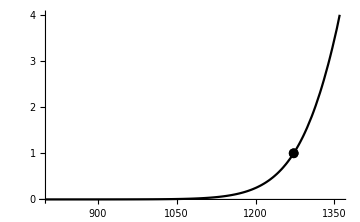

```mathematica
opticalDepthPlot = Plot[Subscript[τ, i][Subscript[η, z][z]],{z,1600,800},PlotStyle->{Black},PlotRange->{{1600,800},{0,4}}];
opticalDepthMarkerPlot=ListPlot[{{Subscript[z, η][SubStar[η]],1.0}},PlotStyle->{Black}, PlotMarkers->{Automatic,Medium}];
Show[{opticalDepthPlot,opticalDepthMarkerPlot},ImageSize->Medium]
```

```mathematica
Export["QES Optical Depth.xls",Table[{z,Subscript[τ, i][Subscript[η, z][z]]},{z,800,1600}]]
```

QES Optical Depth.xls

## Visibility Function

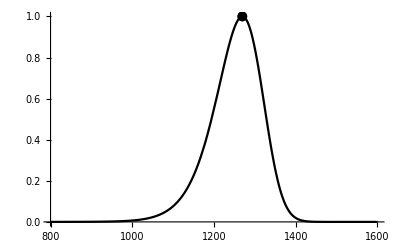

```mathematica
Subscript[g, v][η_]:=τ̇[η] Exp[-Subscript[τ, i][η]]
Subscript[η, MAX]=η/.FindRoot[Subscript[g, v]'[η]==0,{η,Subscript[η, z][1300]}];
visibilityFunctionPlot=Plot[Subscript[g, v][Subscript[η, z][z]]/Subscript[g, v][Subscript[η, MAX]],{z,1600,800},PlotStyle->{Black}];
visibilityMarkerPlot=ListPlot[{{Subscript[z, η][Subscript[η, MAX]],1}},PlotStyle->{Black}, PlotMarkers->{Automatic,Medium}];
Show[{visibilityFunctionPlot,visibilityMarkerPlot}]
```

```mathematica
Export["QES Visibility Function.xls",Table[{z,Subscript[g, v][Subscript[η, z][z]]/Subscript[g, v][Subscript[η, MAX]]},{z,800,1600}]]
```

QES Visibility Function.xls

## Sound Horizon

```mathematica
SubStar[s]=∫_0^(η_*) c/(√(3 (1+R[Subscript[z, η][η']])))ⅆ η';
```

$Aborted

```mathematica
SubStar[z]
Subscript[z, η][Subscript[η, MAX]]
SubStar[s]/km
```

1272.7

1269.32

7.73549×10^21